### Setting up board

#### Global variables

Indexing

```mathematica
MINETYPEI=1;
REVEALORNOT = 2;
NEIGHBORDATAI=3;
TRIPOINTI=4;
NMINESI=5;
```

Mine and other attributes

```mathematica
MINE = 1;
NOTMINE = 0;
NOTREVEALED = 0;
REVEALED = 1;
FLAGGED = 2;
```

Lists

```mathematica
(*This will give me the centroid of all the triangles in a board*)
findTriangle[]
```

#### Getters

```mathematica
getTileType[board_,sector_,row_,column_]:=board⟦sector,row,column,1⟧
```

```mathematica
getTilePoints[board_,sector_,row_,column_]:=board⟦sector,row,column,2⟧
```

```mathematica
getNeighborPos[board_,sector_,row_,column_]:=board⟦sector,row,column,3⟧
```

```mathematica
(*Returns tile data for structured board*)
getTile[board_,listPos_]:=board⟦listPos⟦1⟧,listPos⟦2⟧,listPos⟦3⟧⟧
```

#### Mine setup

```mathematica
neighborsWith0[board_, section_,row_,column_]:=Select[board⟦section,row,column,3⟧,board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,1⟧===0&&board⟦#⟦1⟧,#⟦2⟧,#⟦3⟧,2⟧===0 &]
```

```mathematica
(*This method returns a board without the primitives, just if its a mine or not*)
setupMines[numOfRows_,factor_]:= 
Module[
{tiles = 8*numOfRows^2 ,
lst = Table[{},{x,1,8}],
row,section,
numOfTiles,remainingMineCount,tile,skeletons,neighbors},

remainingMineCount = factor * tiles;
(*For loop for stacking *)
For[row = 1,row≤ numOfRows,row++,
(*Goes through each section*)
For[section = 1, section≤ 8, section++,
AppendTo[lst⟦section⟧,{}];
(*Loop to add tiles to each section & row*)
For[numOfTiles= 1, numOfTiles≤ 2*row - 1,numOfTiles++,
(*zeros are  not mines and 1s are mines*)
tile = RandomChoice[{remainingMineCount/tiles,(tiles - remainingMineCount)/tiles}->{MINE,NOTMINE}];
If[tile===MINE,
remainingMineCount--;
];
tiles--;
AppendTo[lst⟦section⟧⟦row⟧,tile]
]
]
];

Return [lst]
]
```

```mathematica
setupMines[3,0.25]
```

{{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{1,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{1,0}},{{1,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{1,0},{0,0}},{{1,0},{0,0},{0,0},{0,0},{1,0}}},{{{1,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{1,0},{1,0},{0,0},{0,0},{0,0}}},{{{0,0}},{{0,0},{0,0},{0,0}},{{0,0},{0,0},{1,0},{0,0},{0,0}}},{{{1,0}},{{1,0},{1,0},{1,0}},{{0,0},{0,0},{0,0},{1,0},{0,0}}},{{{0,0}},{{1,0},{1,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}}

#### Triangle point setup

Setting up coordinates of triangles.

```mathematica
(*Construct a single row of triangles for the tiling*)
constructTiledTriangleRow[numItems_,offset_]:=Module[
{(*This constructs the zigzag shape of the triangles*)
zigzag=Riffle[
Table[N@{pointX,Sin[(3π)/8]}+offset,{pointX,-(numItems+1)/2 Cos[(3π)/8],(numItems+1)/2 Cos[(3π)/8],2Cos[(3π)/8]}],
Table[N@{pointX,0}+offset,{pointX,-(numItems-1)/2 Cos[(3π)/8],(numItems-1)/2 Cos[(3π)/8],2Cos[(3π)/8]}]

]
},
(*Take advantage of the zigzag shape to construct triangles*)
Return[Table[{zigzag⟦i⟧,zigzag⟦i+1⟧,zigzag⟦i+2⟧},{i,numItems}]]
]
```

```mathematica
constructTiledTriangleRow[5,{0,0}]
```

{{{-1.14805,0.92388},{-0.765367,0.},{-0.382683,0.92388}},{{-0.765367,0.},{-0.382683,0.92388},{0.,0.}},{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}},{{0.,0.},{0.382683,0.92388},{0.765367,0.}},{{0.382683,0.92388},{0.765367,0.},{1.14805,0.92388}}}

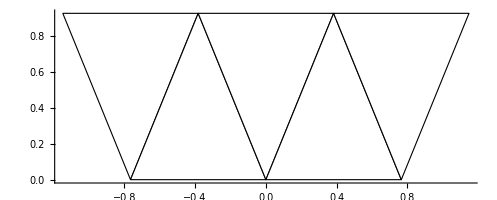

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[constructTiledTriangleRow[5,{0,0}]]},Axes->True]
```

```mathematica
(*Constructs a "big" triangle*)
constructTiledTriangle[numRows_]:=Table[constructTiledTriangleRow[numTriangles,{0,(numTriangles-1)/2*Sin[(3π)/8]}],{numTriangles,1,2numRows-1,2}]
```

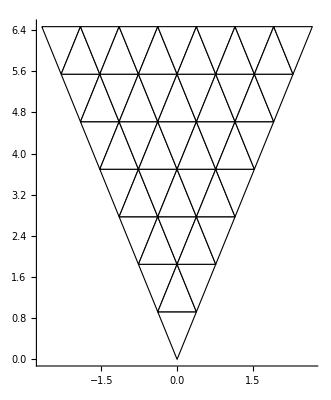

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@constructTiledTriangle[7]]},Axes->True]
```

```mathematica
(*Rotate points of a triangle created from constructTiledTriangle*)
rotateMassTriangle[triangles_,θ_]:=Table[Table[Table[{{Cos[θ],-Sin[θ]},{Sin[θ],Cos[θ]}}.point,{point,triangle}],{triangle,row}],{row,triangles}]
```

```mathematica
(*Construct triangle points for the board tiles.
The return structure is structured the same way as a regular board, except this only gives tile corner coordinates
*)
createBoardSkeleton[numRows_]:=Table[rotateMassTriangle[constructTiledTriangle[numRows],θ],{θ,2π,π/4,-π/4}]
```

```mathematica
createBoardSkeleton[3]
```

{{{{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}}},{{{-0.765367,1.84776},{-0.382683,0.92388},{0.,1.84776}},{{-0.382683,0.92388},{0.,1.84776},{0.382683,0.92388}},{{0.,1.84776},{0.382683,0.92388},{0.765367,1.84776}}},{{{-1.14805,2.77164},{-0.765367,1.84776},{-0.382683,2.77164}},{{-0.765367,1.84776},{-0.382683,2.77164},{0.,1.84776}},{{-0.382683,2.77164},{0.,1.84776},{0.382683,2.77164}},{{0.,1.84776},{0.382683,2.77164},{0.765367,1.84776}},{{0.382683,2.77164},{0.765367,1.84776},{1.14805,2.77164}}}},{{{{0.382683,0.92388},{0.,0.},{0.92388,0.382683}}},{{{0.765367,1.84776},{0.382683,0.92388},{1.30656,1.30656}},{{0.382683,0.92388},{1.30656,1.30656},{0.92388,0.382683}},{{1.30656,1.30656},{0.92388,0.382683},{1.84776,0.765367}}},{{{1.14805,2.77164},{0.765367,1.84776},{1.68925,2.23044}},{{0.765367,1.84776},{1.68925,2.23044},{1.30656,1.30656}},{{1.68925,2.23044},{1.30656,1.30656},{2.23044,1.68925}},{{1.30656,1.30656},{2.23044,1.68925},{1.84776,0.765367}},{{2.23044,1.68925},{1.84776,0.765367},{2.77164,1.14805}}}},{{{{0.92388,0.382683},{0.,0.},{0.92388,-0.382683}}},{{{1.84776,0.765367},{0.92388,0.382683},{1.84776,0.}},{{0.92388,0.382683},{1.84776,0.},{0.92388,-0.382683}},{{1.84776,0.},{0.92388,-0.382683},{1.84776,-0.765367}}},{{{2.77164,1.14805},{1.84776,0.765367},{2.77164,0.382683}},{{1.84776,0.765367},{2.77164,0.382683},{1.84776,0.}},{{2.77164,0.382683},{1.84776,0.},{2.77164,-0.382683}},{{1.84776,0.},{2.77164,-0.382683},{1.84776,-0.765367}},{{2.77164,-0.382683},{1.84776,-0.765367},{2.77164,-1.14805}}}},{{{{0.92388,-0.382683},{0.,0.},{0.382683,-0.92388}}},{{{1.84776,-0.765367},{0.92388,-0.382683},{1.30656,-1.30656}},{{0.92388,-0.382683},{1.30656,-1.30656},{0.382683,-0.92388}},{{1.30656,-1.30656},{0.382683,-0.92388},{0.765367,-1.84776}}},{{{2.77164,-1.14805},{1.84776,-0.765367},{2.23044,-1.68925}},{{1.84776,-0.765367},{2.23044,-1.68925},{1.30656,-1.30656}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},{{1.30656,-1.30656},{1.68925,-2.23044},{0.765367,-1.84776}},{{1.68925,-2.23044},{0.765367,-1.84776},{1.14805,-2.77164}}}},{{{{0.382683,-0.92388},{0.,0.},{-0.382683,-0.92388}}},{{{0.765367,-1.84776},{0.382683,-0.92388},{0.,-1.84776}},{{0.382683,-0.92388},{0.,-1.84776},{-0.382683,-0.92388}},{{0.,-1.84776},{-0.382683,-0.92388},{-0.765367,-1.84776}}},{{{1.14805,-2.77164},{0.765367,-1.84776},{0.382683,-2.77164}},{{0.765367,-1.84776},{0.382683,-2.77164},{0.,-1.84776}},{{0.382683,-2.77164},{0.,-1.84776},{-0.382683,-2.77164}},{{0.,-1.84776},{-0.382683,-2.77164},{-0.765367,-1.84776}},{{-0.382683,-2.77164},{-0.765367,-1.84776},{-1.14805,-2.77164}}}},{{{{-0.382683,-0.92388},{0.,0.},{-0.92388,-0.382683}}},{{{-0.765367,-1.84776},{-0.382683,-0.92388},{-1.30656,-1.30656}},{{-0.382683,-0.92388},{-1.30656,-1.30656},{-0.92388,-0.382683}},{{-1.30656,-1.30656},{-0.92388,-0.382683},{-1.84776,-0.765367}}},{{{-1.14805,-2.77164},{-0.765367,-1.84776},{-1.68925,-2.23044}},{{-0.765367,-1.84776},{-1.68925,-2.23044},{-1.30656,-1.30656}},{{-1.68925,-2.23044},{-1.30656,-1.30656},{-2.23044,-1.68925}},{{-1.30656,-1.30656},{-2.23044,-1.68925},{-1.84776,-0.765367}},{{-2.23044,-1.68925},{-1.84776,-0.765367},{-2.77164,-1.14805}}}},{{{{-0.92388,-0.382683},{0.,0.},{-0.92388,0.382683}}},{{{-1.84776,-0.765367},{-0.92388,-0.382683},{-1.84776,0.}},{{-0.92388,-0.382683},{-1.84776,0.},{-0.92388,0.382683}},{{-1.84776,0.},{-0.92388,0.382683},{-1.84776,0.765367}}},{{{-2.77164,-1.14805},{-1.84776,-0.765367},{-2.77164,-0.382683}},{{-1.84776,-0.765367},{-2.77164,-0.382683},{-1.84776,0.}},{{-2.77164,-0.382683},{-1.84776,0.},{-2.77164,0.382683}},{{-1.84776,0.},{-2.77164,0.382683},{-1.84776,0.765367}},{{-2.77164,0.382683},{-1.84776,0.765367},{-2.77164,1.14805}}}},{{{{-0.92388,0.382683},{0.,0.},{-0.382683,0.92388}}},{{{-1.84776,0.765367},{-0.92388,0.382683},{-1.30656,1.30656}},{{-0.92388,0.382683},{-1.30656,1.30656},{-0.382683,0.92388}},{{-1.30656,1.30656},{-0.382683,0.92388},{-0.765367,1.84776}}},{{{-2.77164,1.14805},{-1.84776,0.765367},{-2.23044,1.68925}},{{-1.84776,0.765367},{-2.23044,1.68925},{-1.30656,1.30656}},{{-2.23044,1.68925},{-1.30656,1.30656},{-1.68925,2.23044}},{{-1.30656,1.30656},{-1.68925,2.23044},{-0.765367,1.84776}},{{-1.68925,2.23044},{-0.765367,1.84776},{-1.14805,2.77164}}}}}

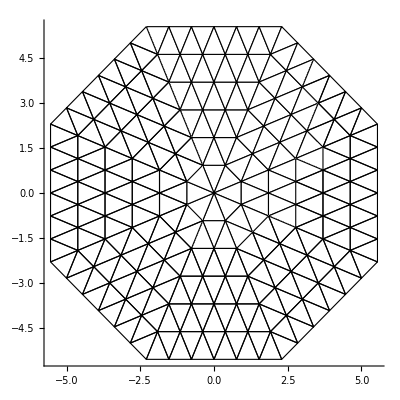

```mathematica
Graphics[{EdgeForm[{Thickness[Large],Black}],White,Triangle[Join@@Join@@createBoardSkeleton[6]]},Axes->True]
```

#### Neighbors setup (casework)

We can split this into 3 general cases:
 * Adjacency within big triangles
 * Adjacency between big triangles
 * Adjacency from torus connections
There is one more case, however - the central 8 triangles
Is there a better way to do this?

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
SetAttributes[getAdjacentBigTriangle,HoldFirst]
getAdjacentBigTriangle[neighborsPoints_,numRows_,sector_,row_,tile_]:=Module[{},
(*Left side*)
If[tile<=2,
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row,2*row-1];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row,2*row-2];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row-1,2*(row-1)-1];
If[tile==1,
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row+1,2*(row+1)-1];
addNeighbor[neighborsPoints,numRows,Mod[sector-2,8]+1,row+1,2*(row+1)-2];
]
];
(*Right side*)
If[tile≥2*row-2,
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row,1];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row,2];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row-1,1];
If[tile==1,
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row+1,1];
addNeighbor[neighborsPoints,numRows,Mod[sector-1,8]+2,row+1,2];
]
]
]
```

```mathematica
(*Find neighbors of tile*)
figureOutNeighbors[numRows_,sector_,row_,tile_]:=Module[
{neighborsPoints={}},
(*Handle special central case*)
If[row==1,
Do[
If[currSector≠sector,addNeighbor[neighborsPoints,numRows,sector,row,tile]]
,{currSector,1,8}
]
];
(*Handle adjacency inside triangle*)
(*Handle adjacency between big triangles*)
getAdjacentBigTriangle[neighborsPoints,numRows,sector,row,tile];
(*Handle adjacency from outer edge connection*)
Return[neighborsPoints]
]
```

```mathematica
setupNeighbors[numRows_]:=
Table[
Table[
Table[
figureOutNeighbors[numRows,sector,row,tile]
,{tile,2*row-1}
]
,{row,numRows}
]
,{sector,1,8}
]
```

```mathematica
setupNeighbors[5]
```

{{{{{1,1,1},{8,1,1},{8,2,3},{8,2,2},{2,1,1},{2,2,1},{2,2,2}}},{{{8,2,3},{8,2,2},{8,1,1},{8,3,5},{8,3,4}},{{8,2,3},{8,2,2},{8,1,1},{2,2,1},{2,2,2},{2,1,1}},{{2,2,1},{2,2,2},{2,1,1}}},{{{8,3,5},{8,3,4},{8,2,3},{8,4,7},{8,4,6}},{{8,3,5},{8,3,4},{8,2,3}},{},{{2,3,1},{2,3,2},{2,2,1}},{{2,3,1},{2,3,2},{2,2,1}}},{{{8,4,7},{8,4,6},{8,3,5},{8,5,9},{8,5,8}},{{8,4,7},{8,4,6},{8,3,5}},{},{},{},{{2,4,1},{2,4,2},{2,3,1}},{{2,4,1},{2,4,2},{2,3,1}}},{{{8,5,9},{8,5,8},{8,4,7}},{{8,5,9},{8,5,8},{8,4,7}},{},{},{},{},{},{{2,5,1},{2,5,2},{2,4,1}},{{2,5,1},{2,5,2},{2,4,1}}}},{{{{2,1,1},{1,1,1},{1,2,3},{1,2,2},{3,1,1},{3,2,1},{3,2,2}}},{{{1,2,3},{1,2,2},{1,1,1},{1,3,5},{1,3,4}},{{1,2,3},{1,2,2},{1,1,1},{3,2,1},{3,2,2},{3,1,1}},{{3,2,1},{3,2,2},{3,1,1}}},{{{1,3,5},{1,3,4},{1,2,3},{1,4,7},{1,4,6}},{{1,3,5},{1,3,4},{1,2,3}},{},{{3,3,1},{3,3,2},{3,2,1}},{{3,3,1},{3,3,2},{3,2,1}}},{{{1,4,7},{1,4,6},{1,3,5},{1,5,9},{1,5,8}},{{1,4,7},{1,4,6},{1,3,5}},{},{},{},{{3,4,1},{3,4,2},{3,3,1}},{{3,4,1},{3,4,2},{3,3,1}}},{{{1,5,9},{1,5,8},{1,4,7}},{{1,5,9},{1,5,8},{1,4,7}},{},{},{},{},{},{{3,5,1},{3,5,2},{3,4,1}},{{3,5,1},{3,5,2},{3,4,1}}}},{{{{3,1,1},{2,1,1},{2,2,3},{2,2,2},{4,1,1},{4,2,1},{4,2,2}}},{{{2,2,3},{2,2,2},{2,1,1},{2,3,5},{2,3,4}},{{2,2,3},{2,2,2},{2,1,1},{4,2,1},{4,2,2},{4,1,1}},{{4,2,1},{4,2,2},{4,1,1}}},{{{2,3,5},{2,3,4},{2,2,3},{2,4,7},{2,4,6}},{{2,3,5},{2,3,4},{2,2,3}},{},{{4,3,1},{4,3,2},{4,2,1}},{{4,3,1},{4,3,2},{4,2,1}}},{{{2,4,7},{2,4,6},{2,3,5},{2,5,9},{2,5,8}},{{2,4,7},{2,4,6},{2,3,5}},{},{},{},{{4,4,1},{4,4,2},{4,3,1}},{{4,4,1},{4,4,2},{4,3,1}}},{{{2,5,9},{2,5,8},{2,4,7}},{{2,5,9},{2,5,8},{2,4,7}},{},{},{},{},{},{{4,5,1},{4,5,2},{4,4,1}},{{4,5,1},{4,5,2},{4,4,1}}}},{{{{4,1,1},{3,1,1},{3,2,3},{3,2,2},{5,1,1},{5,2,1},{5,2,2}}},{{{3,2,3},{3,2,2},{3,1,1},{3,3,5},{3,3,4}},{{3,2,3},{3,2,2},{3,1,1},{5,2,1},{5,2,2},{5,1,1}},{{5,2,1},{5,2,2},{5,1,1}}},{{{3,3,5},{3,3,4},{3,2,3},{3,4,7},{3,4,6}},{{3,3,5},{3,3,4},{3,2,3}},{},{{5,3,1},{5,3,2},{5,2,1}},{{5,3,1},{5,3,2},{5,2,1}}},{{{3,4,7},{3,4,6},{3,3,5},{3,5,9},{3,5,8}},{{3,4,7},{3,4,6},{3,3,5}},{},{},{},{{5,4,1},{5,4,2},{5,3,1}},{{5,4,1},{5,4,2},{5,3,1}}},{{{3,5,9},{3,5,8},{3,4,7}},{{3,5,9},{3,5,8},{3,4,7}},{},{},{},{},{},{{5,5,1},{5,5,2},{5,4,1}},{{5,5,1},{5,5,2},{5,4,1}}}},{{{{5,1,1},{4,1,1},{4,2,3},{4,2,2},{6,1,1},{6,2,1},{6,2,2}}},{{{4,2,3},{4,2,2},{4,1,1},{4,3,5},{4,3,4}},{{4,2,3},{4,2,2},{4,1,1},{6,2,1},{6,2,2},{6,1,1}},{{6,2,1},{6,2,2},{6,1,1}}},{{{4,3,5},{4,3,4},{4,2,3},{4,4,7},{4,4,6}},{{4,3,5},{4,3,4},{4,2,3}},{},{{6,3,1},{6,3,2},{6,2,1}},{{6,3,1},{6,3,2},{6,2,1}}},{{{4,4,7},{4,4,6},{4,3,5},{4,5,9},{4,5,8}},{{4,4,7},{4,4,6},{4,3,5}},{},{},{},{{6,4,1},{6,4,2},{6,3,1}},{{6,4,1},{6,4,2},{6,3,1}}},{{{4,5,9},{4,5,8},{4,4,7}},{{4,5,9},{4,5,8},{4,4,7}},{},{},{},{},{},{{6,5,1},{6,5,2},{6,4,1}},{{6,5,1},{6,5,2},{6,4,1}}}},{{{{6,1,1},{5,1,1},{5,2,3},{5,2,2},{7,1,1},{7,2,1},{7,2,2}}},{{{5,2,3},{5,2,2},{5,1,1},{5,3,5},{5,3,4}},{{5,2,3},{5,2,2},{5,1,1},{7,2,1},{7,2,2},{7,1,1}},{{7,2,1},{7,2,2},{7,1,1}}},{{{5,3,5},{5,3,4},{5,2,3},{5,4,7},{5,4,6}},{{5,3,5},{5,3,4},{5,2,3}},{},{{7,3,1},{7,3,2},{7,2,1}},{{7,3,1},{7,3,2},{7,2,1}}},{{{5,4,7},{5,4,6},{5,3,5},{5,5,9},{5,5,8}},{{5,4,7},{5,4,6},{5,3,5}},{},{},{},{{7,4,1},{7,4,2},{7,3,1}},{{7,4,1},{7,4,2},{7,3,1}}},{{{5,5,9},{5,5,8},{5,4,7}},{{5,5,9},{5,5,8},{5,4,7}},{},{},{},{},{},{{7,5,1},{7,5,2},{7,4,1}},{{7,5,1},{7,5,2},{7,4,1}}}},{{{{7,1,1},{6,1,1},{6,2,3},{6,2,2},{8,1,1},{8,2,1},{8,2,2}}},{{{6,2,3},{6,2,2},{6,1,1},{6,3,5},{6,3,4}},{{6,2,3},{6,2,2},{6,1,1},{8,2,1},{8,2,2},{8,1,1}},{{8,2,1},{8,2,2},{8,1,1}}},{{{6,3,5},{6,3,4},{6,2,3},{6,4,7},{6,4,6}},{{6,3,5},{6,3,4},{6,2,3}},{},{{8,3,1},{8,3,2},{8,2,1}},{{8,3,1},{8,3,2},{8,2,1}}},{{{6,4,7},{6,4,6},{6,3,5},{6,5,9},{6,5,8}},{{6,4,7},{6,4,6},{6,3,5}},{},{},{},{{8,4,1},{8,4,2},{8,3,1}},{{8,4,1},{8,4,2},{8,3,1}}},{{{6,5,9},{6,5,8},{6,4,7}},{{6,5,9},{6,5,8},{6,4,7}},{},{},{},{},{},{{8,5,1},{8,5,2},{8,4,1}},{{8,5,1},{8,5,2},{8,4,1}}}},{{{{8,1,1},{7,1,1},{7,2,3},{7,2,2}}},{{{7,2,3},{7,2,2},{7,1,1},{7,3,5},{7,3,4}},{{7,2,3},{7,2,2},{7,1,1}},{}},{{{7,3,5},{7,3,4},{7,2,3},{7,4,7},{7,4,6}},{{7,3,5},{7,3,4},{7,2,3}},{},{},{}},{{{7,4,7},{7,4,6},{7,3,5},{7,5,9},{7,5,8}},{{7,4,7},{7,4,6},{7,3,5}},{},{},{},{},{}},{{{7,5,9},{7,5,8},{7,4,7}},{{7,5,9},{7,5,8},{7,4,7}},{},{},{},{},{},{},{}}}}

#### Neighbors setup (point comparison)

We use an association to figure out which triangles share points. The coordinates will be rounded by a 1/100 to accommodate a reasonable floating point error.
We then handle adjacencies by outer edge connection as a separate case

```mathematica
(*Error checking to ensure we do not add any invalid neighbors. Less cases to handle manually*)
SetAttributes[addNeighbor,HoldFirst]
addNeighbor[neighborLst_,numRows_,sector_,row_,tile_]:=
If[1≤sector≤8&&1≤row≤numRows&&1≤tile≤2*row-1&&!MemberQ[neighborLst,{sector,row,tile}],AppendTo[neighborLst,{sector,row,tile}]
]
```

```mathematica
roundCoordHundredths[coord_]:=Map[Round[#*100]/100.&,coord]
```

```mathematica
(*Returns an association. Each key is a point rounded to the hundredths, and the values are lists of triangles which have that point*)
findSharedPoints[trianglesCoords_]:=
Module[{pointsAssociations=Association[]},

Do[
(*Point is not yet in association*)
If[MissingQ@pointsAssociations[roundCoordHundredths[point]],
AssociateTo[pointsAssociations,roundCoordHundredths[point]->{}];
];
(*Add point to association*)
AssociateTo[pointsAssociations,roundCoordHundredths[point]->Append[pointsAssociations[roundCoordHundredths[point]],{sectorI,rowI,tileI}]];
,{sectorI,Length@trianglesCoords}
,{rowI,Length@trianglesCoords⟦sectorI⟧}
,{tileI,Length@trianglesCoords⟦sectorI,rowI⟧}
,{point,trianglesCoords⟦sectorI,rowI,tileI⟧}
];
Return[pointsAssociations]
]
```

```mathematica
Length@createBoardSkeleton[3]⟦1⟧
```

3

```mathematica
findSharedPoints[createBoardSkeleton[2]]
```

<|{-0.38,0.92}→{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3}},{0.,0.}→{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1}},{0.38,0.92}→{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},{-0.77,1.85}→{{1,2,1},{8,2,3}},{0.,1.85}→{{1,2,1},{1,2,2},{1,2,3}},{0.77,1.85}→{{1,2,3},{2,2,1}},{0.92,0.38}→{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},{1.31,1.31}→{{2,2,1},{2,2,2},{2,2,3}},{1.85,0.77}→{{2,2,3},{3,2,1}},{0.92,-0.38}→{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},{1.85,0.}→{{3,2,1},{3,2,2},{3,2,3}},{1.85,-0.77}→{{3,2,3},{4,2,1}},{0.38,-0.92}→{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},{1.31,-1.31}→{{4,2,1},{4,2,2},{4,2,3}},{0.77,-1.85}→{{4,2,3},{5,2,1}},{-0.38,-0.92}→{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},{0.,-1.85}→{{5,2,1},{5,2,2},{5,2,3}},{-0.77,-1.85}→{{5,2,3},{6,2,1}},{-0.92,-0.38}→{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},{-1.31,-1.31}→{{6,2,1},{6,2,2},{6,2,3}},{-1.85,-0.77}→{{6,2,3},{7,2,1}},{-0.92,0.38}→{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},{-1.85,0.}→{{7,2,1},{7,2,2},{7,2,3}},{-1.85,0.77}→{{7,2,3},{8,2,1}},{-1.31,1.31}→{{8,2,1},{8,2,2},{8,2,3}}|>

```mathematica
countMines[mineLst_,neighborLst_,sector_,row_,tile_]:=Module[
{},
Return[Length@Select[neighborLst⟦sector,row,tile,1⟧,mineLst⟦#⟦1⟧,#⟦2⟧,#⟦3⟧⟧==1&]]
]
```

```mathematica
(*Returns the neighbors of each tile in the tiling given the coordinates of the tiles.
Returns in the same form as the regular board, but only giving the neighbor data.
*)
setupNeighbors[mineLst_,trianglesCoords_]:=
Module[
{pointsSharing=findSharedPoints[trianglesCoords],
neighborLst=Table[Table[Table[{{}},{tile,row}],{row,sector}],{sector,trianglesCoords}],
POI,
countMinesLst
},
POI=Keys[pointsSharing];
(*Add adjacent triangles*)
Do[
If[triangle1==triangle2||
MemberQ[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2]||
mineLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧⟧,Continue[]];
AppendTo[neighborLst⟦triangle1⟦1⟧,triangle1⟦2⟧,triangle1⟦3⟧,1⟧,triangle2];
,{point,POI}
,{triangle1,pointsSharing[point]}
,{triangle2,pointsSharing[point]}
];
Do[
AppendTo[neighborLst⟦sector,row,tile⟧,countMines[mineLst,neighborLst,sector,row,tile]]
,{sector,Length@neighborLst}
,{row,Length@neighborLst⟦sector⟧}
,{tile,Length@neighborLst⟦sector,row⟧}
];
Return[neighborLst];
]
```

```mathematica
bb=setupNeighbors[setupMines[3,0.25],createBoardSkeleton[2]]
```

{{{{{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{1,2,3},{2,2,1},{2,2,2}},0}},{{{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,2,3}},1},{{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,2,3},{2,1,1},{2,2,1},{2,2,2}},1},{{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1}},1}}},{{{{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2}},3}},{{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{2,2,3}},1},{{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2}},2},{{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1}},1}}},{{{{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2}},0}},{{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{3,2,3}},2},{{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2}},3},{{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1}},0}}},{{{{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2}},5}},{{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{4,2,3}},0},{{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2}},3},{{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1}},1}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2}},5}},{{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{5,2,3}},0},{{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2}},3},{{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2}},0}},{{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{6,2,3}},0},{{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2}},0},{{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1}},3}}},{{{{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}},4}},{{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{7,2,3}},2},{{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2}},2},{{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1}},0}}},{{{{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},3}},{{{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{8,2,3}},0},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},1},{{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,1}},1}}}}

#### Putting it all together

Combine the data for each tile into a single list.

```mathematica
triangleCentroid[triangleCoords_]:=RegionCentroid[Triangle[triangleCoords]]
```

```mathematica
displayConnections[board_]:={Purple,Table[Line[{triangleCentroid[tile⟦TRIPOINTI⟧],triangleCentroid[getTile[board,otherTile]⟦TRIPOINTI⟧]}],{sector,board},{row,sector},{tile,row},{otherTile,tile⟦NEIGHBORDATAI⟧}]}
```

```mathematica
displayBoard[board_]:=
{
{EdgeForm[{Thickness[Large],Black}],Table[{If[tile⟦MINETYPEI⟧==1,Red,Blue],Triangle[tile⟦TRIPOINTI⟧]},{sector,board},{row,sector},{tile,row}]},
Table[Text[tile⟦NMINESI⟧,triangleCentroid[tile⟦TRIPOINTI⟧]],{sector,board},{row,sector},{tile,row}]
}
```

```mathematica
displayBoardWithConnections[board_]:=
{
displayBoard[board],
displayConnections[board]
}
```

```mathematica
boardSetUp[numOfRows_,mineFactor_]:=Module[
{minesData=setupMines[numOfRows,mineFactor],
triangleCoords=createBoardSkeleton[numOfRows],
neighborData
},
neighborData=setupNeighbors[minesData,triangleCoords];
Return[
Table[
Table[
Table[
{minesData⟦sectorI,rowI,tileI⟧,
NOTREVEALED,
neighborData⟦sectorI,rowI,tileI,1⟧,
triangleCoords⟦sectorI,rowI,tileI⟧,
If[minesData⟦sectorI⟧⟦rowI⟧⟦tileI⟧ == 0,neighborData⟦sectorI,rowI,tileI,2⟧,""]
}
,{tileI,1,Length@minesData⟦sectorI,rowI⟧}
]
,{rowI,1,Length@minesData⟦sectorI⟧}
]
,{sectorI,1,8}
]
]
]
```

```mathematica
(*Make this for every tile so that it can be revealed*)
RevealedDisplayBoard[board_]:=
{
{EdgeForm[{Thickness[Large],Black}],Table[{If[tile⟦REVEALORNOT⟧==1,If[tile⟦MINETYPEI⟧ == 1,Red,Blue],Gray],Triangle[tile⟦TRIPOINTI⟧]},{sector,board},{row,sector},{tile,row}]},
Table[Text[tile⟦NMINESI⟧,triangleCentroid[tile⟦TRIPOINTI⟧]],{sector,board},{row,sector},{tile,row}]
}
```

```mathematica
board=boardSetUp[10,0.25]
```

{{{{1,0,{{1,2,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{1,2,3},{2,2,1},{2,2,2}},{{-0.382683,0.92388},{0.,0.},{0.382683,0.92388}},}},{{0,0,{{1,1,1},{1,2,2},{8,1,1},{8,2,2},{8,2,3},{1,3,1},{1,3,2},{8,3,4},{8,3,5},{1,2,3},{1,3,3},{1,3,4}},{{-0.765367,1.84776},{-0.382683,0.92388},{0.,1.84776}},5},{0,0,{{1,1,1},{1,2,1},{8,1,1},{8,2,2},{8,2,3},{1,2,3},{2,1,1},{2,2,1},{2,2,2},{1,3,2},{1,3,3},{1,3,4}},{{-0.382683,0.92388},{0.,1.84776},{0.382683,0.92388}},4},{0,0,{{1,1,1},{1,2,2},{2,1,1},{2,2,1},{2,2,2},{1,2,1},{1,3,2},{1,3,3},{1,3,4},{1,3,5},{2,3,1},{2,3,2}},{{0.,1.84776},{0.382683,0.92388},{0.765367,1.84776}},3}},{{0,0,{{1,2,1},{1,3,2},{8,2,3},{8,3,4},{8,3,5},{1,4,1},{1,4,2},{8,4,6},{8,4,7},{1,3,3},{1,4,3},{1,4,4}},{{-1.14805,2.77164},{-0.765367,1.84776},{-0.382683,2.77164}},5},{1,0,{{1,2,1},{1,3,1},{8,2,3},{8,3,4},{8,3,5},{1,2,2},{1,2,3},{1,3,3},{1,3,4},{1,4,2},{1,4,3},{1,4,4}},{{-0.765367,1.84776},{-0.382683,2.77164},{0.,1.84776}},},{1,0,{{1,2,1},{1,2,2},{1,2,3},{1,3,2},{1,3,4},{1,3,1},{1,4,2},{1,4,3},{1,4,4},{1,3,5},{1,4,5},{1,4,6}},{{-0.382683,2.77164},{0.,1.84776},{0.382683,2.77164}},},{0,0,{{1,2,1},{1,2,2},{1,2,3},{1,3,2},{1,3,3},{1,3,5},{2,2,1},{2,3,1},{2,3,2},{1,4,4},{1,4,5},{1,4,6}},{{0.,1.84776},{0.382683,2.77164},{0.765367,1.84776}},2},{0,0,{{1,2,3},{1,3,4},{2,2,1},{2,3,1},{2,3,2},{1,3,3},{1,4,4},{1,4,5},{1,4,6},{1,4,7},{2,4,1},{2,4,2}},{{0.382683,2.77164},{0.765367,1.84776},{1.14805,2.77164}},1}},{{0,0,{{1,3,1},{1,4,2},{8,3,5},{8,4,6},{8,4,7},{1,5,1},{1,5,2},{8,5,8},{8,5,9},{1,4,3},{1,5,3},{1,5,4}},{{-1.53073,3.69552},{-1.14805,2.77164},{-0.765367,3.69552}},3},{1,0,{{1,3,1},{1,4,1},{8,3,5},{8,4,6},{8,4,7},{1,3,2},{1,3,3},{1,4,3},{1,4,4},{1,5,2},{1,5,3},{1,5,4}},{{-1.14805,2.77164},{-0.765367,3.69552},{-0.382683,2.77164}},},{0,0,{{1,3,1},{1,3,2},{1,3,3},{1,4,2},{1,4,4},{1,4,1},{1,5,2},{1,5,3},{1,5,4},{1,4,5},{1,5,5},{1,5,6}},{{-0.765367,3.69552},{-0.382683,2.77164},{0.,3.69552}},4},{0,0,{{1,3,1},{1,3,2},{1,3,3},{1,4,2},{1,4,3},{1,3,4},{1,3,5},{1,4,5},{1,4,6},{1,5,4},{1,5,5},{1,5,6}},{{-0.382683,2.77164},{0.,3.69552},{0.382683,2.77164}},3},{0,0,{{1,3,3},{1,3,4},{1,3,5},{1,4,4},{1,4,6},{1,4,3},{1,5,4},{1,5,5},{1,5,6},{1,4,7},{1,5,7},{1,5,8}},{{0.,3.69552},{0.382683,2.77164},{0.765367,3.69552}},2},{0,0,{{1,3,3},{1,3,4},{1,3,5},{1,4,4},{1,4,5},{1,4,7},{2,3,1},{2,4,1},{2,4,2},{1,5,6},{1,5,7},{1,5,8}},{{0.382683,2.77164},{0.765367,3.69552},{1.14805,2.77164}},2},{0,0,{{1,3,5},{1,4,6},{2,3,1},{2,4,1},{2,4,2},{1,4,5},{1,5,6},{1,5,7},{1,5,8},{1,5,9},{2,5,1},{2,5,2}},{{0.765367,3.69552},{1.14805,2.77164},{1.53073,3.69552}},2}},{{0,0,{{1,4,1},{1,5,2},{8,4,7},{8,5,8},{8,5,9},{1,6,1},{1,6,2},{8,6,10},{8,6,11},{1,5,3},{1,6,3},{1,6,4}},{{-1.91342,4.6194},{-1.53073,3.69552},{-1.14805,4.6194}},2},{0,0,{{1,4,1},{1,5,1},{8,4,7},{8,5,8},{8,5,9},{1,4,2},{1,4,3},{1,5,3},{1,5,4},{1,6,2},{1,6,3},{1,6,4}},{{-1.53073,3.69552},{-1.14805,4.6194},{-0.765367,3.69552}},2},{1,0,{{1,4,1},{1,4,2},{1,4,3},{1,5,2},{1,5,4},{1,5,1},{1,6,2},{1,6,3},{1,6,4},{1,5,5},{1,6,5},{1,6,6}},{{-1.14805,4.6194},{-0.765367,3.69552},{-0.382683,4.6194}},},{0,0,{{1,4,1},{1,4,2},{1,4,3},{1,5,2},{1,5,3},{1,4,4},{1,4,5},{1,5,5},{1,5,6},{1,6,4},{1,6,5},{1,6,6}},{{-0.765367,3.69552},{-0.382683,4.6194},{0.,3.69552}},2},{0,0,{{1,4,3},{1,4,4},{1,4,5},{1,5,4},{1,5,6},{1,5,3},{1,6,4},{1,6,5},{1,6,6},{1,5,7},{1,6,7},{1,6,8}},{{-0.382683,4.6194},{0.,3.69552},{0.382683,4.6194}},1},{0,0,{{1,4,3},{1,4,4},{1,4,5},{1,5,4},{1,5,5},{1,4,6},{1,4,7},{1,5,7},{1,5,8},{1,6,6},{1,6,7},{1,6,8}},{{0.,3.69552},{0.382683,4.6194},{0.765367,3.69552}},1},{0,0,{{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,5,8},{1,5,5},{1,6,6},{1,6,7},{1,6,8},{1,5,9},{1,6,9},{1,6,10}},{{0.382683,4.6194},{0.765367,3.69552},{1.14805,4.6194}},1},{1,0,{{1,4,5},{1,4,6},{1,4,7},{1,5,6},{1,5,7},{1,5,9},{2,4,1},{2,5,1},{2,5,2},{1,6,8},{1,6,9},{1,6,10}},{{0.765367,3.69552},{1.14805,4.6194},{1.53073,3.69552}},},{0,0,{{1,4,7},{1,5,8},{2,4,1},{2,5,1},{2,5,2},{1,5,7},{1,6,8},{1,6,9},{1,6,10},{1,6,11},{2,6,1},{2,6,2}},{{1.14805,4.6194},{1.53073,3.69552},{1.91342,4.6194}},3}},{{1,0,{{1,5,1},{1,6,2},{8,5,9},{8,6,10},{8,6,11},{1,7,1},{1,7,2},{8,7,12},{8,7,13},{1,6,3},{1,7,3},{1,7,4}},{{-2.2961,5.54328},{-1.91342,4.6194},{-1.53073,5.54328}},},{0,0,{{1,5,1},{1,6,1},{8,5,9},{8,6,10},{8,6,11},{1,5,2},{1,5,3},{1,6,3},{1,6,4},{1,7,2},{1,7,3},{1,7,4}},{{-1.91342,4.6194},{-1.53073,5.54328},{-1.14805,4.6194}},3},{0,0,{{1,5,1},{1,5,2},{1,5,3},{1,6,2},{1,6,4},{1,6,1},{1,7,2},{1,7,3},{1,7,4},{1,6,5},{1,7,5},{1,7,6}},{{-1.53073,5.54328},{-1.14805,4.6194},{-0.765367,5.54328}},3},{0,0,{{1,5,1},{1,5,2},{1,5,3},{1,6,2},{1,6,3},{1,5,4},{1,5,5},{1,6,5},{1,6,6},{1,7,4},{1,7,5},{1,7,6}},{{-1.14805,4.6194},{-0.765367,5.54328},{-0.382683,4.6194}},1},{0,0,{{1,5,3},{1,5,4},{1,5,5},{1,6,4},{1,6,6},{1,6,3},{1,7,4},{1,7,5},{1,7,6},{1,6,7},{1,7,7},{1,7,8}},{{-0.765367,5.54328},{-0.382683,4.6194},{0.,5.54328}},2},{0,0,{{1,5,3},{1,5,4},{1,5,5},{1,6,4},{1,6,5},{1,5,6},{1,5,7},{1,6,7},{1,6,8},{1,7,6},{1,7,7},{1,7,8}},{{-0.382683,4.6194},{0.,5.54328},{0.382683,4.6194}},2},{0,0,{{1,5,5},{1,5,6},{1,5,7},{1,6,6},{1,6,8},{1,6,5},{1,7,6},{1,7,7},{1,7,8},{1,6,9},{1,7,9},{1,7,10}},{{0.,5.54328},{0.382683,4.6194},{0.765367,5.54328}},2},{0,0,{{1,5,5},{1,5,6},{1,5,7},{1,6,6},{1,6,7},{1,5,8},{1,5,9},{1,6,9},{1,6,10},{1,7,8},{1,7,9},{1,7,10}},{{0.382683,4.6194},{0.765367,5.54328},{1.14805,4.6194}},3},{0,0,{{1,5,7},{1,5,8},{1,5,9},{1,6,8},{1,6,10},{1,6,7},{1,7,8},{1,7,9},{1,7,10},{1,6,11},{1,7,11},{1,7,12}},{{0.765367,5.54328},{1.14805,4.6194},{1.53073,5.54328}},4},{0,0,{{1,5,7},{1,5,8},{1,5,9},{1,6,8},{1,6,9},{1,6,11},{2,5,1},{2,6,1},{2,6,2},{1,7,10},{1,7,11},{1,7,12}},{{1.14805,4.6194},{1.53073,5.54328},{1.91342,4.6194}},2},{1,0,{{1,5,9},{1,6,10},{2,5,1},{2,6,1},{2,6,2},{1,6,9},{1,7,10},{1,7,11},{1,7,12},{1,7,13},{2,7,1},{2,7,2}},{{1.53073,5.54328},{1.91342,4.6194},{2.2961,5.54328}},}},{{0,0,{{1,6,1},{1,7,2},{8,6,11},{8,7,12},{8,7,13},{1,8,1},{1,8,2},{8,8,14},{8,8,15},{1,7,3},{1,8,3},{1,8,4}},{{-2.67878,6.46716},{-2.2961,5.54328},{-1.91342,6.46716}},3},{0,0,{{1,6,1},{1,7,1},{8,6,11},{8,7,12},{8,7,13},{1,6,2},{1,6,3},{1,7,3},{1,7,4},{1,8,2},{1,8,3},{1,8,4}},{{-2.2961,5.54328},{-1.91342,6.46716},{-1.53073,5.54328}},3},{1,0,{{1,6,1},{1,6,2},{1,6,3},{1,7,2},{1,7,4},{1,7,1},{1,8,2},{1,8,3},{1,8,4},{1,7,5},{1,8,5},{1,8,6}},{{-1.91342,6.46716},{-1.53073,5.54328},{-1.14805,6.46716}},},{0,0,{{1,6,1},{1,6,2},{1,6,3},{1,7,2},{1,7,3},{1,6,4},{1,6,5},{1,7,5},{1,7,6},{1,8,4},{1,8,5},{1,8,6}},{{-1.53073,5.54328},{-1.14805,6.46716},{-0.765367,5.54328}},3},{0,0,{{1,6,3},{1,6,4},{1,6,5},{1,7,4},{1,7,6},{1,7,3},{1,8,4},{1,8,5},{1,8,6},{1,7,7},{1,8,7},{1,8,8}},{{-1.14805,6.46716},{-0.765367,5.54328},{-0.382683,6.46716}},2},{0,0,{{1,6,3},{1,6,4},{1,6,5},{1,7,4},{1,7,5},{1,6,6},{1,6,7},{1,7,7},{1,7,8},{1,8,6},{1,8,7},{1,8,8}},{{-0.765367,5.54328},{-0.382683,6.46716},{0.,5.54328}},2},{0,0,{{1,6,5},{1,6,6},{1,6,7},{1,7,6},{1,7,8},{1,7,5},{1,8,6},{1,8,7},{1,8,8},{1,7,9},{1,8,9},{1,8,10}},{{-0.382683,6.46716},{0.,5.54328},{0.382683,6.46716}},4},{1,0,{{1,6,5},{1,6,6},{1,6,7},{1,7,6},{1,7,7},{1,6,8},{1,6,9},{1,7,9},{1,7,10},{1,8,8},{1,8,9},{1,8,10}},{{0.,5.54328},{0.382683,6.46716},{0.765367,5.54328}},},{1,0,{{1,6,7},{1,6,8},{1,6,9},{1,7,8},{1,7,10},{1,7,7},{1,8,8},{1,8,9},{1,8,10},{1,7,11},{1,8,11},{1,8,12}},{{0.382683,6.46716},{0.765367,5.54328},{1.14805,6.46716}},},{0,0,{{1,6,7},{1,6,8},{1,6,9},{1,7,8},{1,7,9},{1,6,10},{1,6,11},{1,7,11},{1,7,12},{1,8,10},{1,8,11},{1,8,12}},{{0.765367,5.54328},{1.14805,6.46716},{1.53073,5.54328}},5},{0,0,{{1,6,9},{1,6,10},{1,6,11},{1,7,10},{1,7,12},{1,7,9},{1,8,10},{1,8,11},{1,8,12},{1,7,13},{1,8,13},{1,8,14}},{{1.14805,6.46716},{1.53073,5.54328},{1.91342,6.46716}},5},{0,0,{{1,6,9},{1,6,10},{1,6,11},{1,7,10},{1,7,11},{1,7,13},{2,6,1},{2,7,1},{2,7,2},{1,8,12},{1,8,13},{1,8,14}},{{1.53073,5.54328},{1.91342,6.46716},{2.2961,5.54328}},4},{0,0,{{1,6,11},{1,7,12},{2,6,1},{2,7,1},{2,7,2},{1,7,11},{1,8,12},{1,8,13},{1,8,14},{1,8,15},{2,8,1},{2,8,2}},{{1.91342,6.46716},{2.2961,5.54328},{2.67878,6.46716}},5}},{{0,0,{{1,7,1},{1,8,2},{8,7,13},{8,8,14},{8,8,15},{1,9,1},{1,9,2},{8,9,16},{8,9,17},{1,8,3},{1,9,3},{1,9,4}},{{-3.06147,7.39104},{-2.67878,6.46716},{-2.2961,7.39104}},3},{0,0,{{1,7,1},{1,8,1},{8,7,13},{8,8,14},{8,8,15},{1,7,2},{1,7,3},{1,8,3},{1,8,4},{1,9,2},{1,9,3},{1,9,4}},{{-2.67878,6.46716},{-2.2961,7.39104},{-1.91342,6.46716}},3},{1,0,{{1,7,1},{1,7,2},{1,7,3},{1,8,2},{1,8,4},{1,8,1},{1,9,2},{1,9,3},{1,9,4},{1,8,5},{1,9,5},{1,9,6}},{{-2.2961,7.39104},{-1.91342,6.46716},{-1.53073,7.39104}},},{0,0,{{1,7,1},{1,7,2},{1,7,3},{1,8,2},{1,8,3},{1,7,4},{1,7,5},{1,8,5},{1,8,6},{1,9,4},{1,9,5},{1,9,6}},{{-1.91342,6.46716},{-1.53073,7.39104},{-1.14805,6.46716}},4},{0,0,{{1,7,3},{1,7,4},{1,7,5},{1,8,4},{1,8,6},{1,8,3},{1,9,4},{1,9,5},{1,9,6},{1,8,7},{1,9,7},{1,9,8}},{{-1.53073,7.39104},{-1.14805,6.46716},{-0.765367,7.39104}},4},{1,0,{{1,7,3},{1,7,4},{1,7,5},{1,8,4},{1,8,5},{1,7,6},{1,7,7},{1,8,7},{1,8,8},{1,9,6},{1,9,7},{1,9,8}},{{-1.14805,6.46716},{-0.765367,7.39104},{-0.382683,6.46716}},},{0,0,{{1,7,5},{1,7,6},{1,7,7},{1,8,6},{1,8,8},{1,8,5},{1,9,6},{1,9,7},{1,9,8},{1,8,9},{1,9,9},{1,9,10}},{{-0.765367,7.39104},{-0.382683,6.46716},{0.,7.39104}},1},{0,0,{{1,7,5},{1,7,6},{1,7,7},{1,8,6},{1,8,7},{1,7,8},{1,7,9},{1,8,9},{1,8,10},{1,9,8},{1,9,9},{1,9,10}},{{-0.382683,6.46716},{0.,7.39104},{0.382683,6.46716}},4},{0,0,{{1,7,7},{1,7,8},{1,7,9},{1,8,8},{1,8,10},{1,8,7},{1,9,8},{1,9,9},{1,9,10},{1,8,11},{1,9,11},{1,9,12}},{{0.,7.39104},{0.382683,6.46716},{0.765367,7.39104}},3},{1,0,{{1,7,7},{1,7,8},{1,7,9},{1,8,8},{1,8,9},{1,7,10},{1,7,11},{1,8,11},{1,8,12},{1,9,10},{1,9,11},{1,9,12}},{{0.382683,6.46716},{0.765367,7.39104},{1.14805,6.46716}},},{0,0,{{1,7,9},{1,7,10},{1,7,11},{1,8,10},{1,8,12},{1,8,9},{1,9,10},{1,9,11},{1,9,12},{1,8,13},{1,9,13},{1,9,14}},{{0.765367,7.39104},{1.14805,6.46716},{1.53073,7.39104}},3},{1,0,{{1,7,9},{1,7,10},{1,7,11},{1,8,10},{1,8,11},{1,7,12},{1,7,13},{1,8,13},{1,8,14},{1,9,12},{1,9,13},{1,9,14}},{{1.14805,6.46716},{1.53073,7.39104},{1.91342,6.46716}},},{0,0,{{1,7,11},{1,7,12},{1,7,13},{1,8,12},{1,8,14},{1,8,11},{1,9,12},{1,9,13},{1,9,14},{1,8,15},{1,9,15},{1,9,16}},{{1.53073,7.39104},{1.91342,6.46716},{2.2961,7.39104}},2},{1,0,{{1,7,11},{1,7,12},{1,7,13},{1,8,12},{1,8,13},{1,8,15},{2,7,1},{2,8,1},{2,8,2},{1,9,14},{1,9,15},{1,9,16}},{{1.91342,6.46716},{2.2961,7.39104},{2.67878,6.46716}},},{0,0,{{1,7,13},{1,8,14},{2,7,1},{2,8,1},{2,8,2},{1,8,13},{1,9,14},{1,9,15},{1,9,16},{1,9,17},{2,9,1},{2,9,2}},{{2.2961,7.39104},{2.67878,6.46716},{3.06147,7.39104}},3}},{{1,0,{{1,8,1},{1,9,2},{8,8,15},{8,9,16},{8,9,17},{1,10,1},{1,10,2},{8,10,18},{8,10,19},{1,9,3},{1,10,3},{1,10,4}},{{-3.44415,8.31492},{-3.06147,7.39104},{-2.67878,8.31492}},},{0,0,{{1,8,1},{1,9,1},{8,8,15},{8,9,16},{8,9,17},{1,8,2},{1,8,3},{1,9,3},{1,9,4},{1,10,2},{1,10,3},{1,10,4}},{{-3.06147,7.39104},{-2.67878,8.31492},{-2.2961,7.39104}},4},{0,0,{{1,8,1},{1,8,2},{1,8,3},{1,9,2},{1,9,4},{1,9,1},{1,10,2},{1,10,3},{1,10,4},{1,9,5},{1,10,5},{1,10,6}},{{-2.67878,8.31492},{-2.2961,7.39104},{-1.91342,8.31492}},4},{1,0,{{1,8,1},{1,8,2},{1,8,3},{1,9,2},{1,9,3},{1,8,4},{1,8,5},{1,9,5},{1,9,6},{1,10,4},{1,10,5},{1,10,6}},{{-2.2961,7.39104},{-1.91342,8.31492},{-1.53073,7.39104}},},{0,0,{{1,8,3},{1,8,4},{1,8,5},{1,9,4},{1,9,6},{1,9,3},{1,10,4},{1,10,5},{1,10,6},{1,9,7},{1,10,7},{1,10,8}},{{-1.91342,8.31492},{-1.53073,7.39104},{-1.14805,8.31492}},2},{0,0,{{1,8,3},{1,8,4},{1,8,5},{1,9,4},{1,9,5},{1,8,6},{1,8,7},{1,9,7},{1,9,8},{1,10,6},{1,10,7},{1,10,8}},{{-1.53073,7.39104},{-1.14805,8.31492},{-0.765367,7.39104}},3},{0,0,{{1,8,5},{1,8,6},{1,8,7},{1,9,6},{1,9,8},{1,9,5},{1,10,6},{1,10,7},{1,10,8},{1,9,9},{1,10,9},{1,10,10}},{{-1.14805,8.31492},{-0.765367,7.39104},{-0.382683,8.31492}},2},{0,0,{{1,8,5},{1,8,6},{1,8,7},{1,9,6},{1,9,7},{1,8,8},{1,8,9},{1,9,9},{1,9,10},{1,10,8},{1,10,9},{1,10,10}},{{-0.765367,7.39104},{-0.382683,8.31492},{0.,7.39104}},2},{0,0,{{1,8,7},{1,8,8},{1,8,9},{1,9,8},{1,9,10},{1,9,7},{1,10,8},{1,10,9},{1,10,10},{1,9,11},{1,10,11},{1,10,12}},{{-0.382683,8.31492},{0.,7.39104},{0.382683,8.31492}},1},{0,0,{{1,8,7},{1,8,8},{1,8,9},{1,9,8},{1,9,9},{1,8,10},{1,8,11},{1,9,11},{1,9,12},{1,10,10},{1,10,11},{1,10,12}},{{0.,7.39104},{0.382683,8.31492},{0.765367,7.39104}},1},{0,0,{{1,8,9},{1,8,10},{1,8,11},{1,9,10},{1,9,12},{1,9,9},{1,10,10},{1,10,11},{1,10,12},{1,9,13},{1,10,13},{1,10,14}},{{0.382683,8.31492},{0.765367,7.39104},{1.14805,8.31492}},2},{0,0,{{1,8,9},{1,8,10},{1,8,11},{1,9,10},{1,9,11},{1,8,12},{1,8,13},{1,9,13},{1,9,14},{1,10,12},{1,10,13},{1,10,14}},{{0.765367,7.39104},{1.14805,8.31492},{1.53073,7.39104}},3},{0,0,{{1,8,11},{1,8,12},{1,8,13},{1,9,12},{1,9,14},{1,9,11},{1,10,12},{1,10,13},{1,10,14},{1,9,15},{1,10,15},{1,10,16}},{{1.14805,8.31492},{1.53073,7.39104},{1.91342,8.31492}},2},{0,0,{{1,8,11},{1,8,12},{1,8,13},{1,9,12},{1,9,13},{1,8,14},{1,8,15},{1,9,15},{1,9,16},{1,10,14},{1,10,15},{1,10,16}},{{1.53073,7.39104},{1.91342,8.31492},{2.2961,7.39104}},2},{0,0,{{1,8,13},{1,8,14},{1,8,15},{1,9,14},{1,9,16},{1,9,13},{1,10,14},{1,10,15},{1,10,16},{1,9,17},{1,10,17},{1,10,18}},{{1.91342,8.31492},{2.2961,7.39104},{2.67878,8.31492}},1},{0,0,{{1,8,13},{1,8,14},{1,8,15},{1,9,14},{1,9,15},{1,9,17},{2,8,1},{2,9,1},{2,9,2},{1,10,16},{1,10,17},{1,10,18}},{{2.2961,7.39104},{2.67878,8.31492},{3.06147,7.39104}},1},{0,0,{{1,8,15},{1,9,16},{2,8,1},{2,9,1},{2,9,2},{1,9,15},{1,10,16},{1,10,17},{1,10,18},{1,10,19},{2,10,1},{2,10,2}},{{2.67878,8.31492},{3.06147,7.39104},{3.44415,8.31492}},1}},{{1,0,{{1,9,1},{1,10,2},{8,9,17},{8,10,18},{8,10,19},{1,10,3}},{{-3.82683,9.2388},{-3.44415,8.31492},{-3.06147,9.2388}},},{1,0,{{1,9,1},{1,10,1},{8,9,17},{8,10,18},{8,10,19},{1,9,2},{1,9,3},{1,10,3},{1,10,4}},{{-3.44415,8.31492},{-3.06147,9.2388},{-2.67878,8.31492}},},{0,0,{{1,9,1},{1,9,2},{1,9,3},{1,10,2},{1,10,4},{1,10,1},{1,10,5}},{{-3.06147,9.2388},{-2.67878,8.31492},{-2.2961,9.2388}},3},{0,0,{{1,9,1},{1,9,2},{1,9,3},{1,10,2},{1,10,3},{1,9,4},{1,9,5},{1,10,5},{1,10,6}},{{-2.67878,8.31492},{-2.2961,9.2388},{-1.91342,8.31492}},3},{0,0,{{1,9,3},{1,9,4},{1,9,5},{1,10,4},{1,10,6},{1,10,3},{1,10,7}},{{-2.2961,9.2388},{-1.91342,8.31492},{-1.53073,9.2388}},1},{0,0,{{1,9,3},{1,9,4},{1,9,5},{1,10,4},{1,10,5},{1,9,6},{1,9,7},{1,10,7},{1,10,8}},{{-1.91342,8.31492},{-1.53073,9.2388},{-1.14805,8.31492}},1},{0,0,{{1,9,5},{1,9,6},{1,9,7},{1,10,6},{1,10,8},{1,10,5},{1,10,9}},{{-1.53073,9.2388},{-1.14805,8.31492},{-0.765367,9.2388}},1},{0,0,{{1,9,5},{1,9,6},{1,9,7},{1,10,6},{1,10,7},{1,9,8},{1,9,9},{1,10,9},{1,10,10}},{{-1.14805,8.31492},{-0.765367,9.2388},{-0.382683,8.31492}},1},{1,0,{{1,9,7},{1,9,8},{1,9,9},{1,10,8},{1,10,10},{1,10,7},{1,10,11}},{{-0.765367,9.2388},{-0.382683,8.31492},{0.,9.2388}},},{0,0,{{1,9,7},{1,9,8},{1,9,9},{1,10,8},{1,10,9},{1,9,10},{1,9,11},{1,10,11},{1,10,12}},{{-0.382683,8.31492},{0.,9.2388},{0.382683,8.31492}},1},{0,0,{{1,9,9},{1,9,10},{1,9,11},{1,10,10},{1,10,12},{1,10,9},{1,10,13}},{{0.,9.2388},{0.382683,8.31492},{0.765367,9.2388}},2},{0,0,{{1,9,9},{1,9,10},{1,9,11},{1,10,10},{1,10,11},{1,9,12},{1,9,13},{1,10,13},{1,10,14}},{{0.382683,8.31492},{0.765367,9.2388},{1.14805,8.31492}},1},{1,0,{{1,9,11},{1,9,12},{1,9,13},{1,10,12},{1,10,14},{1,10,11},{1,10,15}},{{0.765367,9.2388},{1.14805,8.31492},{1.53073,9.2388}},},{0,0,{{1,9,11},{1,9,12},{1,9,13},{1,10,12},{1,10,13},{1,9,14},{1,9,15},{1,10,15},{1,10,16}},{{1.14805,8.31492},{1.53073,9.2388},{1.91342,8.31492}},1},{0,0,{{1,9,13},{1,9,14},{1,9,15},{1,10,14},{1,10,16},{1,10,13},{1,10,17}},{{1.53073,9.2388},{1.91342,8.31492},{2.2961,9.2388}},1},{0,0,{{1,9,13},{1,9,14},{1,9,15},{1,10,14},{1,10,15},{1,9,16},{1,9,17},{1,10,17},{1,10,18}},{{1.91342,8.31492},{2.2961,9.2388},{2.67878,8.31492}},0},{0,0,{{1,9,15},{1,9,16},{1,9,17},{1,10,16},{1,10,18},{1,10,15},{1,10,19}},{{2.2961,9.2388},{2.67878,8.31492},{3.06147,9.2388}},0},{0,0,{{1,9,15},{1,9,16},{1,9,17},{1,10,16},{1,10,17},{1,10,19},{2,9,1},{2,10,1},{2,10,2}},{{2.67878,8.31492},{3.06147,9.2388},{3.44415,8.31492}},1},{0,0,{{1,9,17},{1,10,18},{2,9,1},{2,10,1},{2,10,2},{1,10,17}},{{3.06147,9.2388},{3.44415,8.31492},{3.82683,9.2388}},1}}},{{{0,0,{{1,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{1,2,2},{1,2,3},{2,2,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2}},{{0.382683,0.92388},{0.,0.},{0.92388,0.382683}},4}},{{0,0,{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,2},{1,3,4},{1,3,5},{2,3,1},{2,3,2},{2,2,3},{2,3,3},{2,3,4}},{{0.765367,1.84776},{0.382683,0.92388},{1.30656,1.30656}},1},{0,0,{{1,1,1},{1,2,2},{1,2,3},{2,1,1},{2,2,1},{2,2,3},{3,1,1},{3,2,1},{3,2,2},{2,3,2},{2,3,3},{2,3,4}},{{0.382683,0.92388},{1.30656,1.30656},{0.92388,0.382683}},2},{0,0,{{2,1,1},{2,2,2},{3,1,1},{3,2,1},{3,2,2},{2,2,1},{2,3,2},{2,3,3},{2,3,4},{2,3,5},{3,3,1},{3,3,2}},{{1.30656,1.30656},{0.92388,0.382683},{1.84776,0.765367}},1}},{{0,0,{{1,2,3},{1,3,4},{1,3,5},{2,2,1},{2,3,2},{1,4,6},{1,4,7},{2,4,1},{2,4,2},{2,3,3},{2,4,3},{2,4,4}},{{1.14805,2.77164},{0.765367,1.84776},{1.68925,2.23044}},1},{0,0,{{1,2,3},{1,3,4},{1,3,5},{2,2,1},{2,3,1},{2,2,2},{2,2,3},{2,3,3},{2,3,4},{2,4,2},{2,4,3},{2,4,4}},{{0.765367,1.84776},{1.68925,2.23044},{1.30656,1.30656}},1},{0,0,{{2,2,1},{2,2,2},{2,2,3},{2,3,2},{2,3,4},{2,3,1},{2,4,2},{2,4,3},{2,4,4},{2,3,5},{2,4,5},{2,4,6}},{{1.68925,2.23044},{1.30656,1.30656},{2.23044,1.68925}},2},{0,0,{{2,2,1},{2,2,2},{2,2,3},{2,3,2},{2,3,3},{2,3,5},{3,2,1},{3,3,1},{3,3,2},{2,4,4},{2,4,5},{2,4,6}},{{1.30656,1.30656},{2.23044,1.68925},{1.84776,0.765367}},2},{0,0,{{2,2,3},{2,3,4},{3,2,1},{3,3,1},{3,3,2},{2,3,3},{2,4,4},{2,4,5},{2,4,6},{2,4,7},{3,4,1},{3,4,2}},{{2.23044,1.68925},{1.84776,0.765367},{2.77164,1.14805}},4}},{{0,0,{{1,3,5},{1,4,6},{1,4,7},{2,3,1},{2,4,2},{1,5,8},{1,5,9},{2,5,1},{2,5,2},{2,4,3},{2,5,3},{2,5,4}},{{1.53073,3.69552},{1.14805,2.77164},{2.07193,3.15432}},3},{0,0,{{1,3,5},{1,4,6},{1,4,7},{2,3,1},{2,4,1},{2,3,2},{2,3,3},{2,4,3},{2,4,4},{2,5,2},{2,5,3},{2,5,4}},{{1.14805,2.77164},{2.07193,3.15432},{1.68925,2.23044}},2},{1,0,{{2,3,1},{2,3,2},{2,3,3},{2,4,2},{2,4,4},{2,4,1},{2,5,2},{2,5,3},{2,5,4},{2,4,5},{2,5,5},{2,5,6}},{{2.07193,3.15432},{1.68925,2.23044},{2.61313,2.61313}},},{0,0,{{2,3,1},{2,3,2},{2,3,3},{2,4,2},{2,4,3},{2,3,4},{2,3,5},{2,4,5},{2,4,6},{2,5,4},{2,5,5},{2,5,6}},{{1.68925,2.23044},{2.61313,2.61313},{2.23044,1.68925}},3},{1,0,{{2,3,3},{2,3,4},{2,3,5},{2,4,4},{2,4,6},{2,4,3},{2,5,4},{2,5,5},{2,5,6},{2,4,7},{2,5,7},{2,5,8}},{{2.61313,2.61313},{2.23044,1.68925},{3.15432,2.07193}},},{0,0,{{2,3,3},{2,3,4},{2,3,5},{2,4,4},{2,4,5},{2,4,7},{3,3,1},{3,4,1},{3,4,2},{2,5,6},{2,5,7},{2,5,8}},{{2.23044,1.68925},{3.15432,2.07193},{2.77164,1.14805}},4},{0,0,{{2,3,5},{2,4,6},{3,3,1},{3,4,1},{3,4,2},{2,4,5},{2,5,6},{2,5,7},{2,5,8},{2,5,9},{3,5,1},{3,5,2}},{{3.15432,2.07193},{2.77164,1.14805},{3.69552,1.53073}},6}},{{0,0,{{1,4,7},{1,5,8},{1,5,9},{2,4,1},{2,5,2},{1,6,10},{1,6,11},{2,6,1},{2,6,2},{2,5,3},{2,6,3},{2,6,4}},{{1.91342,4.6194},{1.53073,3.69552},{2.45461,4.0782}},5},{1,0,{{1,4,7},{1,5,8},{1,5,9},{2,4,1},{2,5,1},{2,4,2},{2,4,3},{2,5,3},{2,5,4},{2,6,2},{2,6,3},{2,6,4}},{{1.53073,3.69552},{2.45461,4.0782},{2.07193,3.15432}},},{0,0,{{2,4,1},{2,4,2},{2,4,3},{2,5,2},{2,5,4},{2,5,1},{2,6,2},{2,6,3},{2,6,4},{2,5,5},{2,6,5},{2,6,6}},{{2.45461,4.0782},{2.07193,3.15432},{2.99581,3.53701}},4},{0,0,{{2,4,1},{2,4,2},{2,4,3},{2,5,2},{2,5,3},{2,4,4},{2,4,5},{2,5,5},{2,5,6},{2,6,4},{2,6,5},{2,6,6}},{{2.07193,3.15432},{2.99581,3.53701},{2.61313,2.61313}},5},{0,0,{{2,4,3},{2,4,4},{2,4,5},{2,5,4},{2,5,6},{2,5,3},{2,6,4},{2,6,5},{2,6,6},{2,5,7},{2,6,7},{2,6,8}},{{2.99581,3.53701},{2.61313,2.61313},{3.53701,2.99581}},4},{1,0,{{2,4,3},{2,4,4},{2,4,5},{2,5,4},{2,5,5},{2,4,6},{2,4,7},{2,5,7},{2,5,8},{2,6,6},{2,6,7},{2,6,8}},{{2.61313,2.61313},{3.53701,2.99581},{3.15432,2.07193}},},{0,0,{{2,4,5},{2,4,6},{2,4,7},{2,5,6},{2,5,8},{2,5,5},{2,6,6},{2,6,7},{2,6,8},{2,5,9},{2,6,9},{2,6,10}},{{3.53701,2.99581},{3.15432,2.07193},{4.0782,2.45461}},5},{0,0,{{2,4,5},{2,4,6},{2,4,7},{2,5,6},{2,5,7},{2,5,9},{3,4,1},{3,5,1},{3,5,2},{2,6,8},{2,6,9},{2,6,10}},{{3.15432,2.07193},{4.0782,2.45461},{3.69552,1.53073}},7},{1,0,{{2,4,7},{2,5,8},{3,4,1},{3,5,1},{3,5,2},{2,5,7},{2,6,8},{2,6,9},{2,6,10},{2,6,11},{3,6,1},{3,6,2}},{{4.0782,2.45461},{3.69552,1.53073},{4.6194,1.91342}},}},{{0,0,{{1,5,9},{1,6,10},{1,6,11},{2,5,1},{2,6,2},{1,7,12},{1,7,13},{2,7,1},{2,7,2},{2,6,3},{2,7,3},{2,7,4}},{{2.2961,5.54328},{1.91342,4.6194},{2.8373,5.00208}},3},{0,0,{{1,5,9},{1,6,10},{1,6,11},{2,5,1},{2,6,1},{2,5,2},{2,5,3},{2,6,3},{2,6,4},{2,7,2},{2,7,3},{2,7,4}},{{1.91342,4.6194},{2.8373,5.00208},{2.45461,4.0782}},4},{1,0,{{2,5,1},{2,5,2},{2,5,3},{2,6,2},{2,6,4},{2,6,1},{2,7,2},{2,7,3},{2,7,4},{2,6,5},{2,7,5},{2,7,6}},{{2.8373,5.00208},{2.45461,4.0782},{3.37849,4.46088}},},{1,0,{{2,5,1},{2,5,2},{2,5,3},{2,6,2},{2,6,3},{2,5,4},{2,5,5},{2,6,5},{2,6,6},{2,7,4},{2,7,5},{2,7,6}},{{2.45461,4.0782},{3.37849,4.46088},{2.99581,3.53701}},},{0,0,{{2,5,3},{2,5,4},{2,5,5},{2,6,4},{2,6,6},{2,6,3},{2,7,4},{2,7,5},{2,7,6},{2,6,7},{2,7,7},{2,7,8}},{{3.37849,4.46088},{2.99581,3.53701},{3.91969,3.91969}},3},{0,0,{{2,5,3},{2,5,4},{2,5,5},{2,6,4},{2,6,5},{2,5,6},{2,5,7},{2,6,7},{2,6,8},{2,7,6},{2,7,7},{2,7,8}},{{2.99581,3.53701},{3.91969,3.91969},{3.53701,2.99581}},3},{0,0,{{2,5,5},{2,5,6},{2,5,7},{2,6,6},{2,6,8},{2,6,5},{2,7,6},{2,7,7},{2,7,8},{2,6,9},{2,7,9},{2,7,10}},{{3.91969,3.91969},{3.53701,2.99581},{4.46088,3.37849}},4},{0,0,{{2,5,5},{2,5,6},{2,5,7},{2,6,6},{2,6,7},{2,5,8},{2,5,9},{2,6,9},{2,6,10},{2,7,8},{2,7,9},{2,7,10}},{{3.53701,2.99581},{4.46088,3.37849},{4.0782,2.45461}},6},{1,0,{{2,5,7},{2,5,8},{2,5,9},{2,6,8},{2,6,10},{2,6,7},{2,7,8},{2,7,9},{2,7,10},{2,6,11},{2,7,11},{2,7,12}},{{4.46088,3.37849},{4.0782,2.45461},{5.00208,2.8373}},},{1,0,{{2,5,7},{2,5,8},{2,5,9},{2,6,8},{2,6,9},{2,6,11},{3,5,1},{3,6,1},{3,6,2},{2,7,10},{2,7,11},{2,7,12}},{{4.0782,2.45461},{5.00208,2.8373},{4.6194,1.91342}},},{0,0,{{2,5,9},{2,6,10},{3,5,1},{3,6,1},{3,6,2},{2,6,9},{2,7,10},{2,7,11},{2,7,12},{2,7,13},{3,7,1},{3,7,2}},{{5.00208,2.8373},{4.6194,1.91342},{5.54328,2.2961}},6}},{{1,0,{{1,6,11},{1,7,12},{1,7,13},{2,6,1},{2,7,2},{1,8,14},{1,8,15},{2,8,1},{2,8,2},{2,7,3},{2,8,3},{2,8,4}},{{2.67878,6.46716},{2.2961,5.54328},{3.21998,5.92596}},},{0,0,{{1,6,11},{1,7,12},{1,7,13},{2,6,1},{2,7,1},{2,6,2},{2,6,3},{2,7,3},{2,7,4},{2,8,2},{2,8,3},{2,8,4}},{{2.2961,5.54328},{3.21998,5.92596},{2.8373,5.00208}},4},{0,0,{{2,6,1},{2,6,2},{2,6,3},{2,7,2},{2,7,4},{2,7,1},{2,8,2},{2,8,3},{2,8,4},{2,7,5},{2,8,5},{2,8,6}},{{3.21998,5.92596},{2.8373,5.00208},{3.76118,5.38476}},4},{0,0,{{2,6,1},{2,6,2},{2,6,3},{2,7,2},{2,7,3},{2,6,4},{2,6,5},{2,7,5},{2,7,6},{2,8,4},{2,8,5},{2,8,6}},{{2.8373,5.00208},{3.76118,5.38476},{3.37849,4.46088}},3},{0,0,{{2,6,3},{2,6,4},{2,6,5},{2,7,4},{2,7,6},{2,7,3},{2,8,4},{2,8,5},{2,8,6},{2,7,7},{2,8,7},{2,8,8}},{{3.76118,5.38476},{3.37849,4.46088},{4.30237,4.84357}},3},{0,0,{{2,6,3},{2,6,4},{2,6,5},{2,7,4},{2,7,5},{2,6,6},{2,6,7},{2,7,7},{2,7,8},{2,8,6},{2,8,7},{2,8,8}},{{3.37849,4.46088},{4.30237,4.84357},{3.91969,3.91969}},4},{0,0,{{2,6,5},{2,6,6},{2,6,7},{2,7,6},{2,7,8},{2,7,5},{2,8,6},{2,8,7},{2,8,8},{2,7,9},{2,8,9},{2,8,10}},{{4.30237,4.84357},{3.91969,3.91969},{4.84357,4.30237}},2},{1,0,{{2,6,5},{2,6,6},{2,6,7},{2,7,6},{2,7,7},{2,6,8},{2,6,9},{2,7,9},{2,7,10},{2,8,8},{2,8,9},{2,8,10}},{{3.91969,3.91969},{4.84357,4.30237},{4.46088,3.37849}},},{0,0,{{2,6,7},{2,6,8},{2,6,9},{2,7,8},{2,7,10},{2,7,7},{2,8,8},{2,8,9},{2,8,10},{2,7,11},{2,8,11},{2,8,12}},{{4.84357,4.30237},{4.46088,3.37849},{5.38476,3.76118}},3},{1,0,{{2,6,7},{2,6,8},{2,6,9},{2,7,8},{2,7,9},{2,6,10},{2,6,11},{2,7,11},{2,7,12},{2,8,10},{2,8,11},{2,8,12}},{{4.46088,3.37849},{5.38476,3.76118},{5.00208,2.8373}},},{0,0,{{2,6,9},{2,6,10},{2,6,11},{2,7,10},{2,7,12},{2,7,9},{2,8,10},{2,8,11},{2,8,12},{2,7,13},{2,8,13},{2,8,14}},{{5.38476,3.76118},{5.00208,2.8373},{5.92596,3.21998}},5},{0,0,{{2,6,9},{2,6,10},{2,6,11},{2,7,10},{2,7,11},{2,7,13},{3,6,1},{3,7,1},{3,7,2},{2,8,12},{2,8,13},{2,8,14}},{{5.00208,2.8373},{5.92596,3.21998},{5.54328,2.2961}},5},{1,0,{{2,6,11},{2,7,12},{3,6,1},{3,7,1},{3,7,2},{2,7,11},{2,8,12},{2,8,13},{2,8,14},{2,8,15},{3,8,1},{3,8,2}},{{5.92596,3.21998},{5.54328,2.2961},{6.46716,2.67878}},}},{{0,0,{{1,7,13},{1,8,14},{1,8,15},{2,7,1},{2,8,2},{1,9,16},{1,9,17},{2,9,1},{2,9,2},{2,8,3},{2,9,3},{2,9,4}},{{3.06147,7.39104},{2.67878,6.46716},{3.60266,6.84984}},3},{1,0,{{1,7,13},{1,8,14},{1,8,15},{2,7,1},{2,8,1},{2,7,2},{2,7,3},{2,8,3},{2,8,4},{2,9,2},{2,9,3},{2,9,4}},{{2.67878,6.46716},{3.60266,6.84984},{3.21998,5.92596}},},{0,0,{{2,7,1},{2,7,2},{2,7,3},{2,8,2},{2,8,4},{2,8,1},{2,9,2},{2,9,3},{2,9,4},{2,8,5},{2,9,5},{2,9,6}},{{3.60266,6.84984},{3.21998,5.92596},{4.14386,6.30864}},2},{0,0,{{2,7,1},{2,7,2},{2,7,3},{2,8,2},{2,8,3},{2,7,4},{2,7,5},{2,8,5},{2,8,6},{2,9,4},{2,9,5},{2,9,6}},{{3.21998,5.92596},{4.14386,6.30864},{3.76118,5.38476}},3},{0,0,{{2,7,3},{2,7,4},{2,7,5},{2,8,4},{2,8,6},{2,8,3},{2,9,4},{2,9,5},{2,9,6},{2,8,7},{2,9,7},{2,9,8}},{{4.14386,6.30864},{3.76118,5.38476},{4.68506,5.76745}},1},{1,0,{{2,7,3},{2,7,4},{2,7,5},{2,8,4},{2,8,5},{2,7,6},{2,7,7},{2,8,7},{2,8,8},{2,9,6},{2,9,7},{2,9,8}},{{3.76118,5.38476},{4.68506,5.76745},{4.30237,4.84357}},},{0,0,{{2,7,5},{2,7,6},{2,7,7},{2,8,6},{2,8,8},{2,8,5},{2,9,6},{2,9,7},{2,9,8},{2,8,9},{2,9,9},{2,9,10}},{{4.68506,5.76745},{4.30237,4.84357},{5.22625,5.22625}},2},{0,0,{{2,7,5},{2,7,6},{2,7,7},{2,8,6},{2,8,7},{2,7,8},{2,7,9},{2,8,9},{2,8,10},{2,9,8},{2,9,9},{2,9,10}},{{4.30237,4.84357},{5.22625,5.22625},{4.84357,4.30237}},3},{0,0,{{2,7,7},{2,7,8},{2,7,9},{2,8,8},{2,8,10},{2,8,7},{2,9,8},{2,9,9},{2,9,10},{2,8,11},{2,9,11},{2,9,12}},{{5.22625,5.22625},{4.84357,4.30237},{5.76745,4.68506}},3},{0,0,{{2,7,7},{2,7,8},{2,7,9},{2,8,8},{2,8,9},{2,7,10},{2,7,11},{2,8,11},{2,8,12},{2,9,10},{2,9,11},{2,9,12}},{{4.84357,4.30237},{5.76745,4.68506},{5.38476,3.76118}},3},{0,0,{{2,7,9},{2,7,10},{2,7,11},{2,8,10},{2,8,12},{2,8,9},{2,9,10},{2,9,11},{2,9,12},{2,8,13},{2,9,13},{2,9,14}},{{5.76745,4.68506},{5.38476,3.76118},{6.30864,4.14386}},2},{0,0,{{2,7,9},{2,7,10},{2,7,11},{2,8,10},{2,8,11},{2,7,12},{2,7,13},{2,8,13},{2,8,14},{2,9,12},{2,9,13},{2,9,14}},{{5.38476,3.76118},{6.30864,4.14386},{5.92596,3.21998}},4},{0,0,{{2,7,11},{2,7,12},{2,7,13},{2,8,12},{2,8,14},{2,8,11},{2,9,12},{2,9,13},{2,9,14},{2,8,15},{2,9,15},{2,9,16}},{{6.30864,4.14386},{5.92596,3.21998},{6.84984,3.60266}},3},{1,0,{{2,7,11},{2,7,12},{2,7,13},{2,8,12},{2,8,13},{2,8,15},{3,7,1},{3,8,1},{3,8,2},{2,9,14},{2,9,15},{2,9,16}},{{5.92596,3.21998},{6.84984,3.60266},{6.46716,2.67878}},},{0,0,{{2,7,13},{2,8,14},{3,7,1},{3,8,1},{3,8,2},{2,8,13},{2,9,14},{2,9,15},{2,9,16},{2,9,17},{3,9,1},{3,9,2}},{{6.84984,3.60266},{6.46716,2.67878},{7.39104,3.06147}},3}},{{0,0,{{1,8,15},{1,9,16},{1,9,17},{2,8,1},{2,9,2},{1,10,18},{1,10,19},{2,10,1},{2,10,2},{2,9,3},{2,10,3},{2,10,4}},{{3.44415,8.31492},{3.06147,7.39104},{3.98535,7.77372}},1},{0,0,{{1,8,15},{1,9,16},{1,9,17},{2,8,1},{2,9,1},{2,8,2},{2,8,3},{2,9,3},{2,9,4},{2,10,2},{2,10,3},{2,10,4}},{{3.06147,7.39104},{3.98535,7.77372},{3.60266,6.84984}},2},{0,0,{{2,8,1},{2,8,2},{2,8,3},{2,9,2},{2,9,4},{2,9,1},{2,10,2},{2,10,3},{2,10,4},{2,9,5},{2,10,5},{2,10,6}},{{3.98535,7.77372},{3.60266,6.84984},{4.52654,7.23252}},3},{0,0,{{2,8,1},{2,8,2},{2,8,3},{2,9,2},{2,9,3},{2,8,4},{2,8,5},{2,9,5},{2,9,6},{2,10,4},{2,10,5},{2,10,6}},{{3.60266,6.84984},{4.52654,7.23252},{4.14386,6.30864}},2},{0,0,{{2,8,3},{2,8,4},{2,8,5},{2,9,4},{2,9,6},{2,9,3},{2,10,4},{2,10,5},{2,10,6},{2,9,7},{2,10,7},{2,10,8}},{{4.52654,7.23252},{4.14386,6.30864},{5.06774,6.69133}},2},{0,0,{{2,8,3},{2,8,4},{2,8,5},{2,9,4},{2,9,5},{2,8,6},{2,8,7},{2,9,7},{2,9,8},{2,10,6},{2,10,7},{2,10,8}},{{4.14386,6.30864},{5.06774,6.69133},{4.68506,5.76745}},3},{0,0,{{2,8,5},{2,8,6},{2,8,7},{2,9,6},{2,9,8},{2,9,5},{2,10,6},{2,10,7},{2,10,8},{2,9,9},{2,10,9},{2,10,10}},{{5.06774,6.69133},{4.68506,5.76745},{5.60894,6.15013}},4},{0,0,{{2,8,5},{2,8,6},{2,8,7},{2,9,6},{2,9,7},{2,8,8},{2,8,9},{2,9,9},{2,9,10},{2,10,8},{2,10,9},{2,10,10}},{{4.68506,5.76745},{5.60894,6.15013},{5.22625,5.22625}},3},{1,0,{{2,8,7},{2,8,8},{2,8,9},{2,9,8},{2,9,10},{2,9,7},{2,10,8},{2,10,9},{2,10,10},{2,9,11},{2,10,11},{2,10,12}},{{5.60894,6.15013},{5.22625,5.22625},{6.15013,5.60894}},},{0,0,{{2,8,7},{2,8,8},{2,8,9},{2,9,8},{2,9,9},{2,8,10},{2,8,11},{2,9,11},{2,9,12},{2,10,10},{2,10,11},{2,10,12}},{{5.22625,5.22625},{6.15013,5.60894},{5.76745,4.68506}},3},{0,0,{{2,8,9},{2,8,10},{2,8,11},{2,9,10},{2,9,12},{2,9,9},{2,10,10},{2,10,11},{2,10,12},{2,9,13},{2,10,13},{2,10,14}},{{6.15013,5.60894},{5.76745,4.68506},{6.69133,5.06774}},4},{1,0,{{2,8,9},{2,8,10},{2,8,11},{2,9,10},{2,9,11},{2,8,12},{2,8,13},{2,9,13},{2,9,14},{2,10,12},{2,10,13},{2,10,14}},{{5.76745,4.68506},{6.69133,5.06774},{6.30864,4.14386}},},{0,0,{{2,8,11},{2,8,12},{2,8,13},{2,9,12},{2,9,14},{2,9,11},{2,10,12},{2,10,13},{2,10,14},{2,9,15},{2,10,15},{2,10,16}},{{6.69133,5.06774},{6.30864,4.14386},{7.23252,4.52654}},3},{0,0,{{2,8,11},{2,8,12},{2,8,13},{2,9,12},{2,9,13},{2,8,14},{2,8,15},{2,9,15},{2,9,16},{2,10,14},{2,10,15},{2,10,16}},{{6.30864,4.14386},{7.23252,4.52654},{6.84984,3.60266}},2},{0,0,{{2,8,13},{2,8,14},{2,8,15},{2,9,14},{2,9,16},{2,9,13},{2,10,14},{2,10,15},{2,10,16},{2,9,17},{2,10,17},{2,10,18}},{{7.23252,4.52654},{6.84984,3.60266},{7.77372,3.98535}},1},{0,0,{{2,8,13},{2,8,14},{2,8,15},{2,9,14},{2,9,15},{2,9,17},{3,8,1},{3,9,1},{3,9,2},{2,10,16},{2,10,17},{2,10,18}},{{6.84984,3.60266},{7.77372,3.98535},{7.39104,3.06147}},2},{0,0,{{2,8,15},{2,9,16},{3,8,1},{3,9,1},{3,9,2},{2,9,15},{2,10,16},{2,10,17},{2,10,18},{2,10,19},{3,10,1},{3,10,2}},{{7.77372,3.98535},{7.39104,3.06147},{8.31492,3.44415}},3}},{{0,0,{{1,9,17},{1,10,18},{1,10,19},{2,9,1},{2,10,2},{2,10,3}},{{3.82683,9.2388},{3.44415,8.31492},{4.36803,8.6976}},1},{1,0,{{1,9,17},{1,10,18},{1,10,19},{2,9,1},{2,10,1},{2,9,2},{2,9,3},{2,10,3},{2,10,4}},{{3.44415,8.31492},{4.36803,8.6976},{3.98535,7.77372}},},{0,0,{{2,9,1},{2,9,2},{2,9,3},{2,10,2},{2,10,4},{2,10,1},{2,10,5}},{{4.36803,8.6976},{3.98535,7.77372},{4.90923,8.1564}},1},{0,0,{{2,9,1},{2,9,2},{2,9,3},{2,10,2},{2,10,3},{2,9,4},{2,9,5},{2,10,5},{2,10,6}},{{3.98535,7.77372},{4.90923,8.1564},{4.52654,7.23252}},2},{0,0,{{2,9,3},{2,9,4},{2,9,5},{2,10,4},{2,10,6},{2,10,3},{2,10,7}},{{4.90923,8.1564},{4.52654,7.23252},{5.45042,7.61521}},1},{1,0,{{2,9,3},{2,9,4},{2,9,5},{2,10,4},{2,10,5},{2,9,6},{2,9,7},{2,10,7},{2,10,8}},{{4.52654,7.23252},{5.45042,7.61521},{5.06774,6.69133}},},{0,0,{{2,9,5},{2,9,6},{2,9,7},{2,10,6},{2,10,8},{2,10,5},{2,10,9}},{{5.45042,7.61521},{5.06774,6.69133},{5.99162,7.07401}},2},{1,0,{{2,9,5},{2,9,6},{2,9,7},{2,10,6},{2,10,7},{2,9,8},{2,9,9},{2,10,9},{2,10,10}},{{5.06774,6.69133},{5.99162,7.07401},{5.60894,6.15013}},},{0,0,{{2,9,7},{2,9,8},{2,9,9},{2,10,8},{2,10,10},{2,10,7},{2,10,11}},{{5.99162,7.07401},{5.60894,6.15013},{6.53281,6.53281}},2},{0,0,{{2,9,7},{2,9,8},{2,9,9},{2,10,8},{2,10,9},{2,9,10},{2,9,11},{2,10,11},{2,10,12}},{{5.60894,6.15013},{6.53281,6.53281},{6.15013,5.60894}},3},{0,0,{{2,9,9},{2,9,10},{2,9,11},{2,10,10},{2,10,12},{2,10,9},{2,10,13}},{{6.53281,6.53281},{6.15013,5.60894},{7.07401,5.99162}},3},{1,0,{{2,9,9},{2,9,10},{2,9,11},{2,10,10},{2,10,11},{2,9,12},{2,9,13},{2,10,13},{2,10,14}},{{6.15013,5.60894},{7.07401,5.99162},{6.69133,5.06774}},},{1,0,{{2,9,11},{2,9,12},{2,9,13},{2,10,12},{2,10,14},{2,10,11},{2,10,15}},{{7.07401,5.99162},{6.69133,5.06774},{7.61521,5.45042}},},{0,0,{{2,9,11},{2,9,12},{2,9,13},{2,10,12},{2,10,13},{2,9,14},{2,9,15},{2,10,15},{2,10,16}},{{6.69133,5.06774},{7.61521,5.45042},{7.23252,4.52654}},3},{0,0,{{2,9,13},{2,9,14},{2,9,15},{2,10,14},{2,10,16},{2,10,13},{2,10,17}},{{7.61521,5.45042},{7.23252,4.52654},{8.1564,4.90923}},1},{0,0,{{2,9,13},{2,9,14},{2,9,15},{2,10,14},{2,10,15},{2,9,16},{2,9,17},{2,10,17},{2,10,18}},{{7.23252,4.52654},{8.1564,4.90923},{7.77372,3.98535}},0},{0,0,{{2,9,15},{2,9,16},{2,9,17},{2,10,16},{2,10,18},{2,10,15},{2,10,19}},{{8.1564,4.90923},{7.77372,3.98535},{8.6976,4.36803}},1},{0,0,{{2,9,15},{2,9,16},{2,9,17},{2,10,16},{2,10,17},{2,10,19},{3,9,1},{3,10,1},{3,10,2}},{{7.77372,3.98535},{8.6976,4.36803},{8.31492,3.44415}},2},{1,0,{{2,9,17},{2,10,18},{3,9,1},{3,10,1},{3,10,2},{2,10,17}},{{8.6976,4.36803},{8.31492,3.44415},{9.2388,3.82683}},}}},{{{0,0,{{1,1,1},{2,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{2,2,2},{2,2,3},{3,2,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2}},{{0.92388,0.382683},{0.,0.},{0.92388,-0.382683}},5}},{{1,0,{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,2},{2,3,4},{2,3,5},{3,3,1},{3,3,2},{3,2,3},{3,3,3},{3,3,4}},{{1.84776,0.765367},{0.92388,0.382683},{1.84776,0.}},},{0,0,{{2,1,1},{2,2,2},{2,2,3},{3,1,1},{3,2,1},{3,2,3},{4,1,1},{4,2,1},{4,2,2},{3,3,2},{3,3,3},{3,3,4}},{{0.92388,0.382683},{1.84776,0.},{0.92388,-0.382683}},2},{1,0,{{3,1,1},{3,2,2},{4,1,1},{4,2,1},{4,2,2},{3,2,1},{3,3,2},{3,3,3},{3,3,4},{3,3,5},{4,3,1},{4,3,2}},{{1.84776,0.},{0.92388,-0.382683},{1.84776,-0.765367}},}},{{0,0,{{2,2,3},{2,3,4},{2,3,5},{3,2,1},{3,3,2},{2,4,6},{2,4,7},{3,4,1},{3,4,2},{3,3,3},{3,4,3},{3,4,4}},{{2.77164,1.14805},{1.84776,0.765367},{2.77164,0.382683}},3},{0,0,{{2,2,3},{2,3,4},{2,3,5},{3,2,1},{3,3,1},{3,2,2},{3,2,3},{3,3,3},{3,3,4},{3,4,2},{3,4,3},{3,4,4}},{{1.84776,0.765367},{2.77164,0.382683},{1.84776,0.}},3},{0,0,{{3,2,1},{3,2,2},{3,2,3},{3,3,2},{3,3,4},{3,3,1},{3,4,2},{3,4,3},{3,4,4},{3,3,5},{3,4,5},{3,4,6}},{{2.77164,0.382683},{1.84776,0.},{2.77164,-0.382683}},3},{0,0,{{3,2,1},{3,2,2},{3,2,3},{3,3,2},{3,3,3},{3,3,5},{4,2,1},{4,3,1},{4,3,2},{3,4,4},{3,4,5},{3,4,6}},{{1.84776,0.},{2.77164,-0.382683},{1.84776,-0.765367}},2},{0,0,{{3,2,3},{3,3,4},{4,2,1},{4,3,1},{4,3,2},{3,3,3},{3,4,4},{3,4,5},{3,4,6},{3,4,7},{4,4,1},{4,4,2}},{{2.77164,-0.382683},{1.84776,-0.765367},{2.77164,-1.14805}},1}},{{1,0,{{2,3,5},{2,4,6},{2,4,7},{3,3,1},{3,4,2},{2,5,8},{2,5,9},{3,5,1},{3,5,2},{3,4,3},{3,5,3},{3,5,4}},{{3.69552,1.53073},{2.77164,1.14805},{3.69552,0.765367}},},{1,0,{{2,3,5},{2,4,6},{2,4,7},{3,3,1},{3,4,1},{3,3,2},{3,3,3},{3,4,3},{3,4,4},{3,5,2},{3,5,3},{3,5,4}},{{2.77164,1.14805},{3.69552,0.765367},{2.77164,0.382683}},},{0,0,{{3,3,1},{3,3,2},{3,3,3},{3,4,2},{3,4,4},{3,4,1},{3,5,2},{3,5,3},{3,5,4},{3,4,5},{3,5,5},{3,5,6}},{{3.69552,0.765367},{2.77164,0.382683},{3.69552,0.}},3},{0,0,{{3,3,1},{3,3,2},{3,3,3},{3,4,2},{3,4,3},{3,3,4},{3,3,5},{3,4,5},{3,4,6},{3,5,4},{3,5,5},{3,5,6}},{{2.77164,0.382683},{3.69552,0.},{2.77164,-0.382683}},2},{0,0,{{3,3,3},{3,3,4},{3,3,5},{3,4,4},{3,4,6},{3,4,3},{3,5,4},{3,5,5},{3,5,6},{3,4,7},{3,5,7},{3,5,8}},{{3.69552,0.},{2.77164,-0.382683},{3.69552,-0.765367}},1},{0,0,{{3,3,3},{3,3,4},{3,3,5},{3,4,4},{3,4,5},{3,4,7},{4,3,1},{4,4,1},{4,4,2},{3,5,6},{3,5,7},{3,5,8}},{{2.77164,-0.382683},{3.69552,-0.765367},{2.77164,-1.14805}},1},{0,0,{{3,3,5},{3,4,6},{4,3,1},{4,4,1},{4,4,2},{3,4,5},{3,5,6},{3,5,7},{3,5,8},{3,5,9},{4,5,1},{4,5,2}},{{3.69552,-0.765367},{2.77164,-1.14805},{3.69552,-1.53073}},1}},{{1,0,{{2,4,7},{2,5,8},{2,5,9},{3,4,1},{3,5,2},{2,6,10},{2,6,11},{3,6,1},{3,6,2},{3,5,3},{3,6,3},{3,6,4}},{{4.6194,1.91342},{3.69552,1.53073},{4.6194,1.14805}},},{0,0,{{2,4,7},{2,5,8},{2,5,9},{3,4,1},{3,5,1},{3,4,2},{3,4,3},{3,5,3},{3,5,4},{3,6,2},{3,6,3},{3,6,4}},{{3.69552,1.53073},{4.6194,1.14805},{3.69552,0.765367}},4},{0,0,{{3,4,1},{3,4,2},{3,4,3},{3,5,2},{3,5,4},{3,5,1},{3,6,2},{3,6,3},{3,6,4},{3,5,5},{3,6,5},{3,6,6}},{{4.6194,1.14805},{3.69552,0.765367},{4.6194,0.382683}},3},{0,0,{{3,4,1},{3,4,2},{3,4,3},{3,5,2},{3,5,3},{3,4,4},{3,4,5},{3,5,5},{3,5,6},{3,6,4},{3,6,5},{3,6,6}},{{3.69552,0.765367},{4.6194,0.382683},{3.69552,0.}},3},{0,0,{{3,4,3},{3,4,4},{3,4,5},{3,5,4},{3,5,6},{3,5,3},{3,6,4},{3,6,5},{3,6,6},{3,5,7},{3,6,7},{3,6,8}},{{4.6194,0.382683},{3.69552,0.},{4.6194,-0.382683}},1},{1,0,{{3,4,3},{3,4,4},{3,4,5},{3,5,4},{3,5,5},{3,4,6},{3,4,7},{3,5,7},{3,5,8},{3,6,6},{3,6,7},{3,6,8}},{{3.69552,0.},{4.6194,-0.382683},{3.69552,-0.765367}},},{0,0,{{3,4,5},{3,4,6},{3,4,7},{3,5,6},{3,5,8},{3,5,5},{3,6,6},{3,6,7},{3,6,8},{3,5,9},{3,6,9},{3,6,10}},{{4.6194,-0.382683},{3.69552,-0.765367},{4.6194,-1.14805}},1},{0,0,{{3,4,5},{3,4,6},{3,4,7},{3,5,6},{3,5,7},{3,5,9},{4,4,1},{4,5,1},{4,5,2},{3,6,8},{3,6,9},{3,6,10}},{{3.69552,-0.765367},{4.6194,-1.14805},{3.69552,-1.53073}},1},{0,0,{{3,4,7},{3,5,8},{4,4,1},{4,5,1},{4,5,2},{3,5,7},{3,6,8},{3,6,9},{3,6,10},{3,6,11},{4,6,1},{4,6,2}},{{4.6194,-1.14805},{3.69552,-1.53073},{4.6194,-1.91342}},1}},{{0,0,{{2,5,9},{2,6,10},{2,6,11},{3,5,1},{3,6,2},{2,7,12},{2,7,13},{3,7,1},{3,7,2},{3,6,3},{3,7,3},{3,7,4}},{{5.54328,2.2961},{4.6194,1.91342},{5.54328,1.53073}},5},{0,0,{{2,5,9},{2,6,10},{2,6,11},{3,5,1},{3,6,1},{3,5,2},{3,5,3},{3,6,3},{3,6,4},{3,7,2},{3,7,3},{3,7,4}},{{4.6194,1.91342},{5.54328,1.53073},{4.6194,1.14805}},4},{0,0,{{3,5,1},{3,5,2},{3,5,3},{3,6,2},{3,6,4},{3,6,1},{3,7,2},{3,7,3},{3,7,4},{3,6,5},{3,7,5},{3,7,6}},{{5.54328,1.53073},{4.6194,1.14805},{5.54328,0.765367}},2},{0,0,{{3,5,1},{3,5,2},{3,5,3},{3,6,2},{3,6,3},{3,5,4},{3,5,5},{3,6,5},{3,6,6},{3,7,4},{3,7,5},{3,7,6}},{{4.6194,1.14805},{5.54328,0.765367},{4.6194,0.382683}},2},{0,0,{{3,5,3},{3,5,4},{3,5,5},{3,6,4},{3,6,6},{3,6,3},{3,7,4},{3,7,5},{3,7,6},{3,6,7},{3,7,7},{3,7,8}},{{5.54328,0.765367},{4.6194,0.382683},{5.54328,0.}},2},{0,0,{{3,5,3},{3,5,4},{3,5,5},{3,6,4},{3,6,5},{3,5,6},{3,5,7},{3,6,7},{3,6,8},{3,7,6},{3,7,7},{3,7,8}},{{4.6194,0.382683},{5.54328,0.},{4.6194,-0.382683}},2},{0,0,{{3,5,5},{3,5,6},{3,5,7},{3,6,6},{3,6,8},{3,6,5},{3,7,6},{3,7,7},{3,7,8},{3,6,9},{3,7,9},{3,7,10}},{{5.54328,0.},{4.6194,-0.382683},{5.54328,-0.765367}},2},{0,0,{{3,5,5},{3,5,6},{3,5,7},{3,6,6},{3,6,7},{3,5,8},{3,5,9},{3,6,9},{3,6,10},{3,7,8},{3,7,9},{3,7,10}},{{4.6194,-0.382683},{5.54328,-0.765367},{4.6194,-1.14805}},1},{0,0,{{3,5,7},{3,5,8},{3,5,9},{3,6,8},{3,6,10},{3,6,7},{3,7,8},{3,7,9},{3,7,10},{3,6,11},{3,7,11},{3,7,12}},{{5.54328,-0.765367},{4.6194,-1.14805},{5.54328,-1.53073}},1},{0,0,{{3,5,7},{3,5,8},{3,5,9},{3,6,8},{3,6,9},{3,6,11},{4,5,1},{4,6,1},{4,6,2},{3,7,10},{3,7,11},{3,7,12}},{{4.6194,-1.14805},{5.54328,-1.53073},{4.6194,-1.91342}},1},{1,0,{{3,5,9},{3,6,10},{4,5,1},{4,6,1},{4,6,2},{3,6,9},{3,7,10},{3,7,11},{3,7,12},{3,7,13},{4,7,1},{4,7,2}},{{5.54328,-1.53073},{4.6194,-1.91342},{5.54328,-2.2961}},}},{{0,0,{{2,6,11},{2,7,12},{2,7,13},{3,6,1},{3,7,2},{2,8,14},{2,8,15},{3,8,1},{3,8,2},{3,7,3},{3,8,3},{3,8,4}},{{6.46716,2.67878},{5.54328,2.2961},{6.46716,1.91342}},3},{0,0,{{2,6,11},{2,7,12},{2,7,13},{3,6,1},{3,7,1},{3,6,2},{3,6,3},{3,7,3},{3,7,4},{3,8,2},{3,8,3},{3,8,4}},{{5.54328,2.2961},{6.46716,1.91342},{5.54328,1.53073}},3},{0,0,{{3,6,1},{3,6,2},{3,6,3},{3,7,2},{3,7,4},{3,7,1},{3,8,2},{3,8,3},{3,8,4},{3,7,5},{3,8,5},{3,8,6}},{{6.46716,1.91342},{5.54328,1.53073},{6.46716,1.14805}},3},{1,0,{{3,6,1},{3,6,2},{3,6,3},{3,7,2},{3,7,3},{3,6,4},{3,6,5},{3,7,5},{3,7,6},{3,8,4},{3,8,5},{3,8,6}},{{5.54328,1.53073},{6.46716,1.14805},{5.54328,0.765367}},},{0,0,{{3,6,3},{3,6,4},{3,6,5},{3,7,4},{3,7,6},{3,7,3},{3,8,4},{3,8,5},{3,8,6},{3,7,7},{3,8,7},{3,8,8}},{{6.46716,1.14805},{5.54328,0.765367},{6.46716,0.382683}},4},{0,0,{{3,6,3},{3,6,4},{3,6,5},{3,7,4},{3,7,5},{3,6,6},{3,6,7},{3,7,7},{3,7,8},{3,8,6},{3,8,7},{3,8,8}},{{5.54328,0.765367},{6.46716,0.382683},{5.54328,0.}},3},{1,0,{{3,6,5},{3,6,6},{3,6,7},{3,7,6},{3,7,8},{3,7,5},{3,8,6},{3,8,7},{3,8,8},{3,7,9},{3,8,9},{3,8,10}},{{6.46716,0.382683},{5.54328,0.},{6.46716,-0.382683}},},{0,0,{{3,6,5},{3,6,6},{3,6,7},{3,7,6},{3,7,7},{3,6,8},{3,6,9},{3,7,9},{3,7,10},{3,8,8},{3,8,9},{3,8,10}},{{5.54328,0.},{6.46716,-0.382683},{5.54328,-0.765367}},2},{0,0,{{3,6,7},{3,6,8},{3,6,9},{3,7,8},{3,7,10},{3,7,7},{3,8,8},{3,8,9},{3,8,10},{3,7,11},{3,8,11},{3,8,12}},{{6.46716,-0.382683},{5.54328,-0.765367},{6.46716,-1.14805}},3},{0,0,{{3,6,7},{3,6,8},{3,6,9},{3,7,8},{3,7,9},{3,6,10},{3,6,11},{3,7,11},{3,7,12},{3,8,10},{3,8,11},{3,8,12}},{{5.54328,-0.765367},{6.46716,-1.14805},{5.54328,-1.53073}},3},{0,0,{{3,6,9},{3,6,10},{3,6,11},{3,7,10},{3,7,12},{3,7,9},{3,8,10},{3,8,11},{3,8,12},{3,7,13},{3,8,13},{3,8,14}},{{6.46716,-1.14805},{5.54328,-1.53073},{6.46716,-1.91342}},4},{0,0,{{3,6,9},{3,6,10},{3,6,11},{3,7,10},{3,7,11},{3,7,13},{4,6,1},{4,7,1},{4,7,2},{3,8,12},{3,8,13},{3,8,14}},{{5.54328,-1.53073},{6.46716,-1.91342},{5.54328,-2.2961}},4},{0,0,{{3,6,11},{3,7,12},{4,6,1},{4,7,1},{4,7,2},{3,7,11},{3,8,12},{3,8,13},{3,8,14},{3,8,15},{4,8,1},{4,8,2}},{{6.46716,-1.91342},{5.54328,-2.2961},{6.46716,-2.67878}},4}},{{0,0,{{2,7,13},{2,8,14},{2,8,15},{3,7,1},{3,8,2},{2,9,16},{2,9,17},{3,9,1},{3,9,2},{3,8,3},{3,9,3},{3,9,4}},{{7.39104,3.06147},{6.46716,2.67878},{7.39104,2.2961}},3},{0,0,{{2,7,13},{2,8,14},{2,8,15},{3,7,1},{3,8,1},{3,7,2},{3,7,3},{3,8,3},{3,8,4},{3,9,2},{3,9,3},{3,9,4}},{{6.46716,2.67878},{7.39104,2.2961},{6.46716,1.91342}},4},{0,0,{{3,7,1},{3,7,2},{3,7,3},{3,8,2},{3,8,4},{3,8,1},{3,9,2},{3,9,3},{3,9,4},{3,8,5},{3,9,5},{3,9,6}},{{7.39104,2.2961},{6.46716,1.91342},{7.39104,1.53073}},3},{1,0,{{3,7,1},{3,7,2},{3,7,3},{3,8,2},{3,8,3},{3,7,4},{3,7,5},{3,8,5},{3,8,6},{3,9,4},{3,9,5},{3,9,6}},{{6.46716,1.91342},{7.39104,1.53073},{6.46716,1.14805}},},{0,0,{{3,7,3},{3,7,4},{3,7,5},{3,8,4},{3,8,6},{3,8,3},{3,9,4},{3,9,5},{3,9,6},{3,8,7},{3,9,7},{3,9,8}},{{7.39104,1.53073},{6.46716,1.14805},{7.39104,0.765367}},4},{1,0,{{3,7,3},{3,7,4},{3,7,5},{3,8,4},{3,8,5},{3,7,6},{3,7,7},{3,8,7},{3,8,8},{3,9,6},{3,9,7},{3,9,8}},{{6.46716,1.14805},{7.39104,0.765367},{6.46716,0.382683}},},{0,0,{{3,7,5},{3,7,6},{3,7,7},{3,8,6},{3,8,8},{3,8,5},{3,9,6},{3,9,7},{3,9,8},{3,8,9},{3,9,9},{3,9,10}},{{7.39104,0.765367},{6.46716,0.382683},{7.39104,0.}},3},{0,0,{{3,7,5},{3,7,6},{3,7,7},{3,8,6},{3,8,7},{3,7,8},{3,7,9},{3,8,9},{3,8,10},{3,9,8},{3,9,9},{3,9,10}},{{6.46716,0.382683},{7.39104,0.},{6.46716,-0.382683}},4},{0,0,{{3,7,7},{3,7,8},{3,7,9},{3,8,8},{3,8,10},{3,8,7},{3,9,8},{3,9,9},{3,9,10},{3,8,11},{3,9,11},{3,9,12}},{{7.39104,0.},{6.46716,-0.382683},{7.39104,-0.765367}},3},{1,0,{{3,7,7},{3,7,8},{3,7,9},{3,8,8},{3,8,9},{3,7,10},{3,7,11},{3,8,11},{3,8,12},{3,9,10},{3,9,11},{3,9,12}},{{6.46716,-0.382683},{7.39104,-0.765367},{6.46716,-1.14805}},},{0,0,{{3,7,9},{3,7,10},{3,7,11},{3,8,10},{3,8,12},{3,8,9},{3,9,10},{3,9,11},{3,9,12},{3,8,13},{3,9,13},{3,9,14}},{{7.39104,-0.765367},{6.46716,-1.14805},{7.39104,-1.53073}},4},{1,0,{{3,7,9},{3,7,10},{3,7,11},{3,8,10},{3,8,11},{3,7,12},{3,7,13},{3,8,13},{3,8,14},{3,9,12},{3,9,13},{3,9,14}},{{6.46716,-1.14805},{7.39104,-1.53073},{6.46716,-1.91342}},},{1,0,{{3,7,11},{3,7,12},{3,7,13},{3,8,12},{3,8,14},{3,8,11},{3,9,12},{3,9,13},{3,9,14},{3,8,15},{3,9,15},{3,9,16}},{{7.39104,-1.53073},{6.46716,-1.91342},{7.39104,-2.2961}},},{0,0,{{3,7,11},{3,7,12},{3,7,13},{3,8,12},{3,8,13},{3,8,15},{4,7,1},{4,8,1},{4,8,2},{3,9,14},{3,9,15},{3,9,16}},{{6.46716,-1.91342},{7.39104,-2.2961},{6.46716,-2.67878}},3},{0,0,{{3,7,13},{3,8,14},{4,7,1},{4,8,1},{4,8,2},{3,8,13},{3,9,14},{3,9,15},{3,9,16},{3,9,17},{4,9,1},{4,9,2}},{{7.39104,-2.2961},{6.46716,-2.67878},{7.39104,-3.06147}},3}},{{0,0,{{2,8,15},{2,9,16},{2,9,17},{3,8,1},{3,9,2},{2,10,18},{2,10,19},{3,10,1},{3,10,2},{3,9,3},{3,10,3},{3,10,4}},{{8.31492,3.44415},{7.39104,3.06147},{8.31492,2.67878}},3},{1,0,{{2,8,15},{2,9,16},{2,9,17},{3,8,1},{3,9,1},{3,8,2},{3,8,3},{3,9,3},{3,9,4},{3,10,2},{3,10,3},{3,10,4}},{{7.39104,3.06147},{8.31492,2.67878},{7.39104,2.2961}},},{0,0,{{3,8,1},{3,8,2},{3,8,3},{3,9,2},{3,9,4},{3,9,1},{3,10,2},{3,10,3},{3,10,4},{3,9,5},{3,10,5},{3,10,6}},{{8.31492,2.67878},{7.39104,2.2961},{8.31492,1.91342}},2},{0,0,{{3,8,1},{3,8,2},{3,8,3},{3,9,2},{3,9,3},{3,8,4},{3,8,5},{3,9,5},{3,9,6},{3,10,4},{3,10,5},{3,10,6}},{{7.39104,2.2961},{8.31492,1.91342},{7.39104,1.53073}},3},{1,0,{{3,8,3},{3,8,4},{3,8,5},{3,9,4},{3,9,6},{3,9,3},{3,10,4},{3,10,5},{3,10,6},{3,9,7},{3,10,7},{3,10,8}},{{8.31492,1.91342},{7.39104,1.53073},{8.31492,1.14805}},},{0,0,{{3,8,3},{3,8,4},{3,8,5},{3,9,4},{3,9,5},{3,8,6},{3,8,7},{3,9,7},{3,9,8},{3,10,6},{3,10,7},{3,10,8}},{{7.39104,1.53073},{8.31492,1.14805},{7.39104,0.765367}},4},{0,0,{{3,8,5},{3,8,6},{3,8,7},{3,9,6},{3,9,8},{3,9,5},{3,10,6},{3,10,7},{3,10,8},{3,9,9},{3,10,9},{3,10,10}},{{8.31492,1.14805},{7.39104,0.765367},{8.31492,0.382683}},3},{0,0,{{3,8,5},{3,8,6},{3,8,7},{3,9,6},{3,9,7},{3,8,8},{3,8,9},{3,9,9},{3,9,10},{3,10,8},{3,10,9},{3,10,10}},{{7.39104,0.765367},{8.31492,0.382683},{7.39104,0.}},2},{0,0,{{3,8,7},{3,8,8},{3,8,9},{3,9,8},{3,9,10},{3,9,7},{3,10,8},{3,10,9},{3,10,10},{3,9,11},{3,10,11},{3,10,12}},{{8.31492,0.382683},{7.39104,0.},{8.31492,-0.382683}},1},{1,0,{{3,8,7},{3,8,8},{3,8,9},{3,9,8},{3,9,9},{3,8,10},{3,8,11},{3,9,11},{3,9,12},{3,10,10},{3,10,11},{3,10,12}},{{7.39104,0.},{8.31492,-0.382683},{7.39104,-0.765367}},},{0,0,{{3,8,9},{3,8,10},{3,8,11},{3,9,10},{3,9,12},{3,9,9},{3,10,10},{3,10,11},{3,10,12},{3,9,13},{3,10,13},{3,10,14}},{{8.31492,-0.382683},{7.39104,-0.765367},{8.31492,-1.14805}},3},{0,0,{{3,8,9},{3,8,10},{3,8,11},{3,9,10},{3,9,11},{3,8,12},{3,8,13},{3,9,13},{3,9,14},{3,10,12},{3,10,13},{3,10,14}},{{7.39104,-0.765367},{8.31492,-1.14805},{7.39104,-1.53073}},5},{0,0,{{3,8,11},{3,8,12},{3,8,13},{3,9,12},{3,9,14},{3,9,11},{3,10,12},{3,10,13},{3,10,14},{3,9,15},{3,10,15},{3,10,16}},{{8.31492,-1.14805},{7.39104,-1.53073},{8.31492,-1.91342}},3},{0,0,{{3,8,11},{3,8,12},{3,8,13},{3,9,12},{3,9,13},{3,8,14},{3,8,15},{3,9,15},{3,9,16},{3,10,14},{3,10,15},{3,10,16}},{{7.39104,-1.53073},{8.31492,-1.91342},{7.39104,-2.2961}},2},{0,0,{{3,8,13},{3,8,14},{3,8,15},{3,9,14},{3,9,16},{3,9,13},{3,10,14},{3,10,15},{3,10,16},{3,9,17},{3,10,17},{3,10,18}},{{8.31492,-1.91342},{7.39104,-2.2961},{8.31492,-2.67878}},2},{0,0,{{3,8,13},{3,8,14},{3,8,15},{3,9,14},{3,9,15},{3,9,17},{4,8,1},{4,9,1},{4,9,2},{3,10,16},{3,10,17},{3,10,18}},{{7.39104,-2.2961},{8.31492,-2.67878},{7.39104,-3.06147}},3},{0,0,{{3,8,15},{3,9,16},{4,8,1},{4,9,1},{4,9,2},{3,9,15},{3,10,16},{3,10,17},{3,10,18},{3,10,19},{4,10,1},{4,10,2}},{{8.31492,-2.67878},{7.39104,-3.06147},{8.31492,-3.44415}},3}},{{1,0,{{2,9,17},{2,10,18},{2,10,19},{3,9,1},{3,10,2},{3,10,3}},{{9.2388,3.82683},{8.31492,3.44415},{9.2388,3.06147}},},{0,0,{{2,9,17},{2,10,18},{2,10,19},{3,9,1},{3,10,1},{3,9,2},{3,9,3},{3,10,3},{3,10,4}},{{8.31492,3.44415},{9.2388,3.06147},{8.31492,2.67878}},3},{0,0,{{3,9,1},{3,9,2},{3,9,3},{3,10,2},{3,10,4},{3,10,1},{3,10,5}},{{9.2388,3.06147},{8.31492,2.67878},{9.2388,2.2961}},2},{0,0,{{3,9,1},{3,9,2},{3,9,3},{3,10,2},{3,10,3},{3,9,4},{3,9,5},{3,10,5},{3,10,6}},{{8.31492,2.67878},{9.2388,2.2961},{8.31492,1.91342}},2},{0,0,{{3,9,3},{3,9,4},{3,9,5},{3,10,4},{3,10,6},{3,10,3},{3,10,7}},{{9.2388,2.2961},{8.31492,1.91342},{9.2388,1.53073}},2},{0,0,{{3,9,3},{3,9,4},{3,9,5},{3,10,4},{3,10,5},{3,9,6},{3,9,7},{3,10,7},{3,10,8}},{{8.31492,1.91342},{9.2388,1.53073},{8.31492,1.14805}},2},{1,0,{{3,9,5},{3,9,6},{3,9,7},{3,10,6},{3,10,8},{3,10,5},{3,10,9}},{{9.2388,1.53073},{8.31492,1.14805},{9.2388,0.765367}},},{0,0,{{3,9,5},{3,9,6},{3,9,7},{3,10,6},{3,10,7},{3,9,8},{3,9,9},{3,10,9},{3,10,10}},{{8.31492,1.14805},{9.2388,0.765367},{8.31492,0.382683}},2},{0,0,{{3,9,7},{3,9,8},{3,9,9},{3,10,8},{3,10,10},{3,10,7},{3,10,11}},{{9.2388,0.765367},{8.31492,0.382683},{9.2388,0.}},1},{0,0,{{3,9,7},{3,9,8},{3,9,9},{3,10,8},{3,10,9},{3,9,10},{3,9,11},{3,10,11},{3,10,12}},{{8.31492,0.382683},{9.2388,0.},{8.31492,-0.382683}},1},{0,0,{{3,9,9},{3,9,10},{3,9,11},{3,10,10},{3,10,12},{3,10,9},{3,10,13}},{{9.2388,0.},{8.31492,-0.382683},{9.2388,-0.765367}},2},{0,0,{{3,9,9},{3,9,10},{3,9,11},{3,10,10},{3,10,11},{3,9,12},{3,9,13},{3,10,13},{3,10,14}},{{8.31492,-0.382683},{9.2388,-0.765367},{8.31492,-1.14805}},2},{1,0,{{3,9,11},{3,9,12},{3,9,13},{3,10,12},{3,10,14},{3,10,11},{3,10,15}},{{9.2388,-0.765367},{8.31492,-1.14805},{9.2388,-1.53073}},},{0,0,{{3,9,11},{3,9,12},{3,9,13},{3,10,12},{3,10,13},{3,9,14},{3,9,15},{3,10,15},{3,10,16}},{{8.31492,-1.14805},{9.2388,-1.53073},{8.31492,-1.91342}},1},{0,0,{{3,9,13},{3,9,14},{3,9,15},{3,10,14},{3,10,16},{3,10,13},{3,10,17}},{{9.2388,-1.53073},{8.31492,-1.91342},{9.2388,-2.2961}},1},{0,0,{{3,9,13},{3,9,14},{3,9,15},{3,10,14},{3,10,15},{3,9,16},{3,9,17},{3,10,17},{3,10,18}},{{8.31492,-1.91342},{9.2388,-2.2961},{8.31492,-2.67878}},1},{0,0,{{3,9,15},{3,9,16},{3,9,17},{3,10,16},{3,10,18},{3,10,15},{3,10,19}},{{9.2388,-2.2961},{8.31492,-2.67878},{9.2388,-3.06147}},1},{1,0,{{3,9,15},{3,9,16},{3,9,17},{3,10,16},{3,10,17},{3,10,19},{4,9,1},{4,10,1},{4,10,2}},{{8.31492,-2.67878},{9.2388,-3.06147},{8.31492,-3.44415}},},{0,0,{{3,9,17},{3,10,18},{4,9,1},{4,10,1},{4,10,2},{3,10,17}},{{9.2388,-3.06147},{8.31492,-3.44415},{9.2388,-3.82683}},3}}},{{{0,0,{{1,1,1},{2,1,1},{3,1,1},{5,1,1},{6,1,1},{7,1,1},{8,1,1},{3,2,2},{3,2,3},{4,2,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2}},{{0.92388,-0.382683},{0.,0.},{0.382683,-0.92388}},5}},{{0,0,{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,2},{3,3,4},{3,3,5},{4,3,1},{4,3,2},{4,2,3},{4,3,3},{4,3,4}},{{1.84776,-0.765367},{0.92388,-0.382683},{1.30656,-1.30656}},2},{0,0,{{3,1,1},{3,2,2},{3,2,3},{4,1,1},{4,2,1},{4,2,3},{5,1,1},{5,2,1},{5,2,2},{4,3,2},{4,3,3},{4,3,4}},{{0.92388,-0.382683},{1.30656,-1.30656},{0.382683,-0.92388}},4},{0,0,{{4,1,1},{4,2,2},{5,1,1},{5,2,1},{5,2,2},{4,2,1},{4,3,2},{4,3,3},{4,3,4},{4,3,5},{5,3,1},{5,3,2}},{{1.30656,-1.30656},{0.382683,-0.92388},{0.765367,-1.84776}},3}},{{0,0,{{3,2,3},{3,3,4},{3,3,5},{4,2,1},{4,3,2},{3,4,6},{3,4,7},{4,4,1},{4,4,2},{4,3,3},{4,4,3},{4,4,4}},{{2.77164,-1.14805},{1.84776,-0.765367},{2.23044,-1.68925}},1},{0,0,{{3,2,3},{3,3,4},{3,3,5},{4,2,1},{4,3,1},{4,2,2},{4,2,3},{4,3,3},{4,3,4},{4,4,2},{4,4,3},{4,4,4}},{{1.84776,-0.765367},{2.23044,-1.68925},{1.30656,-1.30656}},2},{0,0,{{4,2,1},{4,2,2},{4,2,3},{4,3,2},{4,3,4},{4,3,1},{4,4,2},{4,4,3},{4,4,4},{4,3,5},{4,4,5},{4,4,6}},{{2.23044,-1.68925},{1.30656,-1.30656},{1.68925,-2.23044}},1},{1,0,{{4,2,1},{4,2,2},{4,2,3},{4,3,2},{4,3,3},{4,3,5},{5,2,1},{5,3,1},{5,3,2},{4,4,4},{4,4,5},{4,4,6}},{{1.30656,-1.30656},{1.68925,-2.23044},{0.765367,-1.84776}},},{0,0,{{4,2,3},{4,3,4},{5,2,1},{5,3,1},{5,3,2},{4,3,3},{4,4,4},{4,4,5},{4,4,6},{4,4,7},{5,4,1},{5,4,2}},{{1.68925,-2.23044},{0.765367,-1.84776},{1.14805,-2.77164}},3}},{{0,0,{{3,3,5},{3,4,6},{3,4,7},{4,3,1},{4,4,2},{3,5,8},{3,5,9},{4,5,1},{4,5,2},{4,4,3},{4,5,3},{4,5,4}},{{3.69552,-1.53073},{2.77164,-1.14805},{3.15432,-2.07193}},0},{0,0,{{3,3,5},{3,4,6},{3,4,7},{4,3,1},{4,4,1},{4,3,2},{4,3,3},{4,4,3},{4,4,4},{4,5,2},{4,5,3},{4,5,4}},{{2.77164,-1.14805},{3.15432,-2.07193},{2.23044,-1.68925}},0},{0,0,{{4,3,1},{4,3,2},{4,3,3},{4,4,2},{4,4,4},{4,4,1},{4,5,2},{4,5,3},{4,5,4},{4,4,5},{4,5,5},{4,5,6}},{{3.15432,-2.07193},{2.23044,-1.68925},{2.61313,-2.61313}},1},{0,0,{{4,3,1},{4,3,2},{4,3,3},{4,4,2},{4,4,3},{4,3,4},{4,3,5},{4,4,5},{4,4,6},{4,5,4},{4,5,5},{4,5,6}},{{2.23044,-1.68925},{2.61313,-2.61313},{1.68925,-2.23044}},2},{0,0,{{4,3,3},{4,3,4},{4,3,5},{4,4,4},{4,4,6},{4,4,3},{4,5,4},{4,5,5},{4,5,6},{4,4,7},{4,5,7},{4,5,8}},{{2.61313,-2.61313},{1.68925,-2.23044},{2.07193,-3.15432}},3},{0,0,{{4,3,3},{4,3,4},{4,3,5},{4,4,4},{4,4,5},{4,4,7},{5,3,1},{5,4,1},{5,4,2},{4,5,6},{4,5,7},{4,5,8}},{{1.68925,-2.23044},{2.07193,-3.15432},{1.14805,-2.77164}},4},{0,0,{{4,3,5},{4,4,6},{5,3,1},{5,4,1},{5,4,2},{4,4,5},{4,5,6},{4,5,7},{4,5,8},{4,5,9},{5,5,1},{5,5,2}},{{2.07193,-3.15432},{1.14805,-2.77164},{1.53073,-3.69552}},4}},{{0,0,{{3,4,7},{3,5,8},{3,5,9},{4,4,1},{4,5,2},{3,6,10},{3,6,11},{4,6,1},{4,6,2},{4,5,3},{4,6,3},{4,6,4}},{{4.6194,-1.91342},{3.69552,-1.53073},{4.0782,-2.45461}},1},{0,0,{{3,4,7},{3,5,8},{3,5,9},{4,4,1},{4,5,1},{4,4,2},{4,4,3},{4,5,3},{4,5,4},{4,6,2},{4,6,3},{4,6,4}},{{3.69552,-1.53073},{4.0782,-2.45461},{3.15432,-2.07193}},0},{0,0,{{4,4,1},{4,4,2},{4,4,3},{4,5,2},{4,5,4},{4,5,1},{4,6,2},{4,6,3},{4,6,4},{4,5,5},{4,6,5},{4,6,6}},{{4.0782,-2.45461},{3.15432,-2.07193},{3.53701,-2.99581}},2},{0,0,{{4,4,1},{4,4,2},{4,4,3},{4,5,2},{4,5,3},{4,4,4},{4,4,5},{4,5,5},{4,5,6},{4,6,4},{4,6,5},{4,6,6}},{{3.15432,-2.07193},{3.53701,-2.99581},{2.61313,-2.61313}},2},{1,0,{{4,4,3},{4,4,4},{4,4,5},{4,5,4},{4,5,6},{4,5,3},{4,6,4},{4,6,5},{4,6,6},{4,5,7},{4,6,7},{4,6,8}},{{3.53701,-2.99581},{2.61313,-2.61313},{2.99581,-3.53701}},},{0,0,{{4,4,3},{4,4,4},{4,4,5},{4,5,4},{4,5,5},{4,4,6},{4,4,7},{4,5,7},{4,5,8},{4,6,6},{4,6,7},{4,6,8}},{{2.61313,-2.61313},{2.99581,-3.53701},{2.07193,-3.15432}},2},{1,0,{{4,4,5},{4,4,6},{4,4,7},{4,5,6},{4,5,8},{4,5,5},{4,6,6},{4,6,7},{4,6,8},{4,5,9},{4,6,9},{4,6,10}},{{2.99581,-3.53701},{2.07193,-3.15432},{2.45461,-4.0782}},},{0,0,{{4,4,5},{4,4,6},{4,4,7},{4,5,6},{4,5,7},{4,5,9},{5,4,1},{5,5,1},{5,5,2},{4,6,8},{4,6,9},{4,6,10}},{{2.07193,-3.15432},{2.45461,-4.0782},{1.53073,-3.69552}},4},{0,0,{{4,4,7},{4,5,8},{5,4,1},{5,5,1},{5,5,2},{4,5,7},{4,6,8},{4,6,9},{4,6,10},{4,6,11},{5,6,1},{5,6,2}},{{2.45461,-4.0782},{1.53073,-3.69552},{1.91342,-4.6194}},6}},{{0,0,{{3,5,9},{3,6,10},{3,6,11},{4,5,1},{4,6,2},{3,7,12},{3,7,13},{4,7,1},{4,7,2},{4,6,3},{4,7,3},{4,7,4}},{{5.54328,-2.2961},{4.6194,-1.91342},{5.00208,-2.8373}},3},{0,0,{{3,5,9},{3,6,10},{3,6,11},{4,5,1},{4,6,1},{4,5,2},{4,5,3},{4,6,3},{4,6,4},{4,7,2},{4,7,3},{4,7,4}},{{4.6194,-1.91342},{5.00208,-2.8373},{4.0782,-2.45461}},2},{0,0,{{4,5,1},{4,5,2},{4,5,3},{4,6,2},{4,6,4},{4,6,1},{4,7,2},{4,7,3},{4,7,4},{4,6,5},{4,7,5},{4,7,6}},{{5.00208,-2.8373},{4.0782,-2.45461},{4.46088,-3.37849}},2},{0,0,{{4,5,1},{4,5,2},{4,5,3},{4,6,2},{4,6,3},{4,5,4},{4,5,5},{4,6,5},{4,6,6},{4,7,4},{4,7,5},{4,7,6}},{{4.0782,-2.45461},{4.46088,-3.37849},{3.53701,-2.99581}},2},{1,0,{{4,5,3},{4,5,4},{4,5,5},{4,6,4},{4,6,6},{4,6,3},{4,7,4},{4,7,5},{4,7,6},{4,6,7},{4,7,7},{4,7,8}},{{4.46088,-3.37849},{3.53701,-2.99581},{3.91969,-3.91969}},},{0,0,{{4,5,3},{4,5,4},{4,5,5},{4,6,4},{4,6,5},{4,5,6},{4,5,7},{4,6,7},{4,6,8},{4,7,6},{4,7,7},{4,7,8}},{{3.53701,-2.99581},{3.91969,-3.91969},{2.99581,-3.53701}},4},{0,0,{{4,5,5},{4,5,6},{4,5,7},{4,6,6},{4,6,8},{4,6,5},{4,7,6},{4,7,7},{4,7,8},{4,6,9},{4,7,9},{4,7,10}},{{3.91969,-3.91969},{2.99581,-3.53701},{3.37849,-4.46088}},4},{0,0,{{4,5,5},{4,5,6},{4,5,7},{4,6,6},{4,6,7},{4,5,8},{4,5,9},{4,6,9},{4,6,10},{4,7,8},{4,7,9},{4,7,10}},{{2.99581,-3.53701},{3.37849,-4.46088},{2.45461,-4.0782}},4},{0,0,{{4,5,7},{4,5,8},{4,5,9},{4,6,8},{4,6,10},{4,6,7},{4,7,8},{4,7,9},{4,7,10},{4,6,11},{4,7,11},{4,7,12}},{{3.37849,-4.46088},{2.45461,-4.0782},{2.8373,-5.00208}},5},{1,0,{{4,5,7},{4,5,8},{4,5,9},{4,6,8},{4,6,9},{4,6,11},{5,5,1},{5,6,1},{5,6,2},{4,7,10},{4,7,11},{4,7,12}},{{2.45461,-4.0782},{2.8373,-5.00208},{1.91342,-4.6194}},},{1,0,{{4,5,9},{4,6,10},{5,5,1},{5,6,1},{5,6,2},{4,6,9},{4,7,10},{4,7,11},{4,7,12},{4,7,13},{5,7,1},{5,7,2}},{{2.8373,-5.00208},{1.91342,-4.6194},{2.2961,-5.54328}},}},{{1,0,{{3,6,11},{3,7,12},{3,7,13},{4,6,1},{4,7,2},{3,8,14},{3,8,15},{4,8,1},{4,8,2},{4,7,3},{4,8,3},{4,8,4}},{{6.46716,-2.67878},{5.54328,-2.2961},{5.92596,-3.21998}},},{0,0,{{3,6,11},{3,7,12},{3,7,13},{4,6,1},{4,7,1},{4,6,2},{4,6,3},{4,7,3},{4,7,4},{4,8,2},{4,8,3},{4,8,4}},{{5.54328,-2.2961},{5.92596,-3.21998},{5.00208,-2.8373}},3},{1,0,{{4,6,1},{4,6,2},{4,6,3},{4,7,2},{4,7,4},{4,7,1},{4,8,2},{4,8,3},{4,8,4},{4,7,5},{4,8,5},{4,8,6}},{{5.92596,-3.21998},{5.00208,-2.8373},{5.38476,-3.76118}},},{0,0,{{4,6,1},{4,6,2},{4,6,3},{4,7,2},{4,7,3},{4,6,4},{4,6,5},{4,7,5},{4,7,6},{4,8,4},{4,8,5},{4,8,6}},{{5.00208,-2.8373},{5.38476,-3.76118},{4.46088,-3.37849}},3},{0,0,{{4,6,3},{4,6,4},{4,6,5},{4,7,4},{4,7,6},{4,7,3},{4,8,4},{4,8,5},{4,8,6},{4,7,7},{4,8,7},{4,8,8}},{{5.38476,-3.76118},{4.46088,-3.37849},{4.84357,-4.30237}},3},{0,0,{{4,6,3},{4,6,4},{4,6,5},{4,7,4},{4,7,5},{4,6,6},{4,6,7},{4,7,7},{4,7,8},{4,8,6},{4,8,7},{4,8,8}},{{4.46088,-3.37849},{4.84357,-4.30237},{3.91969,-3.91969}},2},{0,0,{{4,6,5},{4,6,6},{4,6,7},{4,7,6},{4,7,8},{4,7,5},{4,8,6},{4,8,7},{4,8,8},{4,7,9},{4,8,9},{4,8,10}},{{4.84357,-4.30237},{3.91969,-3.91969},{4.30237,-4.84357}},2},{1,0,{{4,6,5},{4,6,6},{4,6,7},{4,7,6},{4,7,7},{4,6,8},{4,6,9},{4,7,9},{4,7,10},{4,8,8},{4,8,9},{4,8,10}},{{3.91969,-3.91969},{4.30237,-4.84357},{3.37849,-4.46088}},},{0,0,{{4,6,7},{4,6,8},{4,6,9},{4,7,8},{4,7,10},{4,7,7},{4,8,8},{4,8,9},{4,8,10},{4,7,11},{4,8,11},{4,8,12}},{{4.30237,-4.84357},{3.37849,-4.46088},{3.76118,-5.38476}},3},{0,0,{{4,6,7},{4,6,8},{4,6,9},{4,7,8},{4,7,9},{4,6,10},{4,6,11},{4,7,11},{4,7,12},{4,8,10},{4,8,11},{4,8,12}},{{3.37849,-4.46088},{3.76118,-5.38476},{2.8373,-5.00208}},5},{1,0,{{4,6,9},{4,6,10},{4,6,11},{4,7,10},{4,7,12},{4,7,9},{4,8,10},{4,8,11},{4,8,12},{4,7,13},{4,8,13},{4,8,14}},{{3.76118,-5.38476},{2.8373,-5.00208},{3.21998,-5.92596}},},{0,0,{{4,6,9},{4,6,10},{4,6,11},{4,7,10},{4,7,11},{4,7,13},{5,6,1},{5,7,1},{5,7,2},{4,8,12},{4,8,13},{4,8,14}},{{2.8373,-5.00208},{3.21998,-5.92596},{2.2961,-5.54328}},5},{0,0,{{4,6,11},{4,7,12},{5,6,1},{5,7,1},{5,7,2},{4,7,11},{4,8,12},{4,8,13},{4,8,14},{4,8,15},{5,8,1},{5,8,2}},{{3.21998,-5.92596},{2.2961,-5.54328},{2.67878,-6.46716}},4}},{{0,0,{{3,7,13},{3,8,14},{3,8,15},{4,7,1},{4,8,2},{3,9,16},{3,9,17},{4,9,1},{4,9,2},{4,8,3},{4,9,3},{4,9,4}},{{7.39104,-3.06147},{6.46716,-2.67878},{6.84984,-3.60266}},2},{0,0,{{3,7,13},{3,8,14},{3,8,15},{4,7,1},{4,8,1},{4,7,2},{4,7,3},{4,8,3},{4,8,4},{4,9,2},{4,9,3},{4,9,4}},{{6.46716,-2.67878},{6.84984,-3.60266},{5.92596,-3.21998}},2},{0,0,{{4,7,1},{4,7,2},{4,7,3},{4,8,2},{4,8,4},{4,8,1},{4,9,2},{4,9,3},{4,9,4},{4,8,5},{4,9,5},{4,9,6}},{{6.84984,-3.60266},{5.92596,-3.21998},{6.30864,-4.14386}},3},{0,0,{{4,7,1},{4,7,2},{4,7,3},{4,8,2},{4,8,3},{4,7,4},{4,7,5},{4,8,5},{4,8,6},{4,9,4},{4,9,5},{4,9,6}},{{5.92596,-3.21998},{6.30864,-4.14386},{5.38476,-3.76118}},3},{1,0,{{4,7,3},{4,7,4},{4,7,5},{4,8,4},{4,8,6},{4,8,3},{4,9,4},{4,9,5},{4,9,6},{4,8,7},{4,9,7},{4,9,8}},{{6.30864,-4.14386},{5.38476,-3.76118},{5.76745,-4.68506}},},{0,0,{{4,7,3},{4,7,4},{4,7,5},{4,8,4},{4,8,5},{4,7,6},{4,7,7},{4,8,7},{4,8,8},{4,9,6},{4,9,7},{4,9,8}},{{5.38476,-3.76118},{5.76745,-4.68506},{4.84357,-4.30237}},3},{0,0,{{4,7,5},{4,7,6},{4,7,7},{4,8,6},{4,8,8},{4,8,5},{4,9,6},{4,9,7},{4,9,8},{4,8,9},{4,9,9},{4,9,10}},{{5.76745,-4.68506},{4.84357,-4.30237},{5.22625,-5.22625}},3},{0,0,{{4,7,5},{4,7,6},{4,7,7},{4,8,6},{4,8,7},{4,7,8},{4,7,9},{4,8,9},{4,8,10},{4,9,8},{4,9,9},{4,9,10}},{{4.84357,-4.30237},{5.22625,-5.22625},{4.30237,-4.84357}},2},{0,0,{{4,7,7},{4,7,8},{4,7,9},{4,8,8},{4,8,10},{4,8,7},{4,9,8},{4,9,9},{4,9,10},{4,8,11},{4,9,11},{4,9,12}},{{5.22625,-5.22625},{4.30237,-4.84357},{4.68506,-5.76745}},2},{0,0,{{4,7,7},{4,7,8},{4,7,9},{4,8,8},{4,8,9},{4,7,10},{4,7,11},{4,8,11},{4,8,12},{4,9,10},{4,9,11},{4,9,12}},{{4.30237,-4.84357},{4.68506,-5.76745},{3.76118,-5.38476}},4},{0,0,{{4,7,9},{4,7,10},{4,7,11},{4,8,10},{4,8,12},{4,8,9},{4,9,10},{4,9,11},{4,9,12},{4,8,13},{4,9,13},{4,9,14}},{{4.68506,-5.76745},{3.76118,-5.38476},{4.14386,-6.30864}},5},{1,0,{{4,7,9},{4,7,10},{4,7,11},{4,8,10},{4,8,11},{4,7,12},{4,7,13},{4,8,13},{4,8,14},{4,9,12},{4,9,13},{4,9,14}},{{3.76118,-5.38476},{4.14386,-6.30864},{3.21998,-5.92596}},},{0,0,{{4,7,11},{4,7,12},{4,7,13},{4,8,12},{4,8,14},{4,8,11},{4,9,12},{4,9,13},{4,9,14},{4,8,15},{4,9,15},{4,9,16}},{{4.14386,-6.30864},{3.21998,-5.92596},{3.60266,-6.84984}},4},{0,0,{{4,7,11},{4,7,12},{4,7,13},{4,8,12},{4,8,13},{4,8,15},{5,7,1},{5,8,1},{5,8,2},{4,9,14},{4,9,15},{4,9,16}},{{3.21998,-5.92596},{3.60266,-6.84984},{2.67878,-6.46716}},4},{0,0,{{4,7,13},{4,8,14},{5,7,1},{5,8,1},{5,8,2},{4,8,13},{4,9,14},{4,9,15},{4,9,16},{4,9,17},{5,9,1},{5,9,2}},{{3.60266,-6.84984},{2.67878,-6.46716},{3.06147,-7.39104}},2}},{{1,0,{{3,8,15},{3,9,16},{3,9,17},{4,8,1},{4,9,2},{3,10,18},{3,10,19},{4,10,1},{4,10,2},{4,9,3},{4,10,3},{4,10,4}},{{8.31492,-3.44415},{7.39104,-3.06147},{7.77372,-3.98535}},},{0,0,{{3,8,15},{3,9,16},{3,9,17},{4,8,1},{4,9,1},{4,8,2},{4,8,3},{4,9,3},{4,9,4},{4,10,2},{4,10,3},{4,10,4}},{{7.39104,-3.06147},{7.77372,-3.98535},{6.84984,-3.60266}},1},{0,0,{{4,8,1},{4,8,2},{4,8,3},{4,9,2},{4,9,4},{4,9,1},{4,10,2},{4,10,3},{4,10,4},{4,9,5},{4,10,5},{4,10,6}},{{7.77372,-3.98535},{6.84984,-3.60266},{7.23252,-4.52654}},3},{0,0,{{4,8,1},{4,8,2},{4,8,3},{4,9,2},{4,9,3},{4,8,4},{4,8,5},{4,9,5},{4,9,6},{4,10,4},{4,10,5},{4,10,6}},{{6.84984,-3.60266},{7.23252,-4.52654},{6.30864,-4.14386}},3},{0,0,{{4,8,3},{4,8,4},{4,8,5},{4,9,4},{4,9,6},{4,9,3},{4,10,4},{4,10,5},{4,10,6},{4,9,7},{4,10,7},{4,10,8}},{{7.23252,-4.52654},{6.30864,-4.14386},{6.69133,-5.06774}},6},{0,0,{{4,8,3},{4,8,4},{4,8,5},{4,9,4},{4,9,5},{4,8,6},{4,8,7},{4,9,7},{4,9,8},{4,10,6},{4,10,7},{4,10,8}},{{6.30864,-4.14386},{6.69133,-5.06774},{5.76745,-4.68506}},5},{1,0,{{4,8,5},{4,8,6},{4,8,7},{4,9,6},{4,9,8},{4,9,5},{4,10,6},{4,10,7},{4,10,8},{4,9,9},{4,10,9},{4,10,10}},{{6.69133,-5.06774},{5.76745,-4.68506},{6.15013,-5.60894}},},{0,0,{{4,8,5},{4,8,6},{4,8,7},{4,9,6},{4,9,7},{4,8,8},{4,8,9},{4,9,9},{4,9,10},{4,10,8},{4,10,9},{4,10,10}},{{5.76745,-4.68506},{6.15013,-5.60894},{5.22625,-5.22625}},5},{0,0,{{4,8,7},{4,8,8},{4,8,9},{4,9,8},{4,9,10},{4,9,7},{4,10,8},{4,10,9},{4,10,10},{4,9,11},{4,10,11},{4,10,12}},{{6.15013,-5.60894},{5.22625,-5.22625},{5.60894,-6.15013}},4},{1,0,{{4,8,7},{4,8,8},{4,8,9},{4,9,8},{4,9,9},{4,8,10},{4,8,11},{4,9,11},{4,9,12},{4,10,10},{4,10,11},{4,10,12}},{{5.22625,-5.22625},{5.60894,-6.15013},{4.68506,-5.76745}},},{0,0,{{4,8,9},{4,8,10},{4,8,11},{4,9,10},{4,9,12},{4,9,9},{4,10,10},{4,10,11},{4,10,12},{4,9,13},{4,10,13},{4,10,14}},{{5.60894,-6.15013},{4.68506,-5.76745},{5.06774,-6.69133}},2},{0,0,{{4,8,9},{4,8,10},{4,8,11},{4,9,10},{4,9,11},{4,8,12},{4,8,13},{4,9,13},{4,9,14},{4,10,12},{4,10,13},{4,10,14}},{{4.68506,-5.76745},{5.06774,-6.69133},{4.14386,-6.30864}},4},{1,0,{{4,8,11},{4,8,12},{4,8,13},{4,9,12},{4,9,14},{4,9,11},{4,10,12},{4,10,13},{4,10,14},{4,9,15},{4,10,15},{4,10,16}},{{5.06774,-6.69133},{4.14386,-6.30864},{4.52654,-7.23252}},},{1,0,{{4,8,11},{4,8,12},{4,8,13},{4,9,12},{4,9,13},{4,8,14},{4,8,15},{4,9,15},{4,9,16},{4,10,14},{4,10,15},{4,10,16}},{{4.14386,-6.30864},{4.52654,-7.23252},{3.60266,-6.84984}},},{0,0,{{4,8,13},{4,8,14},{4,8,15},{4,9,14},{4,9,16},{4,9,13},{4,10,14},{4,10,15},{4,10,16},{4,9,17},{4,10,17},{4,10,18}},{{4.52654,-7.23252},{3.60266,-6.84984},{3.98535,-7.77372}},3},{0,0,{{4,8,13},{4,8,14},{4,8,15},{4,9,14},{4,9,15},{4,9,17},{5,8,1},{5,9,1},{5,9,2},{4,10,16},{4,10,17},{4,10,18}},{{3.60266,-6.84984},{3.98535,-7.77372},{3.06147,-7.39104}},2},{0,0,{{4,8,15},{4,9,16},{5,8,1},{5,9,1},{5,9,2},{4,9,15},{4,10,16},{4,10,17},{4,10,18},{4,10,19},{5,10,1},{5,10,2}},{{3.98535,-7.77372},{3.06147,-7.39104},{3.44415,-8.31492}},4}},{{1,0,{{3,9,17},{3,10,18},{3,10,19},{4,9,1},{4,10,2},{4,10,3}},{{9.2388,-3.82683},{8.31492,-3.44415},{8.6976,-4.36803}},},{0,0,{{3,9,17},{3,10,18},{3,10,19},{4,9,1},{4,10,1},{4,9,2},{4,9,3},{4,10,3},{4,10,4}},{{8.31492,-3.44415},{8.6976,-4.36803},{7.77372,-3.98535}},3},{0,0,{{4,9,1},{4,9,2},{4,9,3},{4,10,2},{4,10,4},{4,10,1},{4,10,5}},{{8.6976,-4.36803},{7.77372,-3.98535},{8.1564,-4.90923}},3},{0,0,{{4,9,1},{4,9,2},{4,9,3},{4,10,2},{4,10,3},{4,9,4},{4,9,5},{4,10,5},{4,10,6}},{{7.77372,-3.98535},{8.1564,-4.90923},{7.23252,-4.52654}},3},{1,0,{{4,9,3},{4,9,4},{4,9,5},{4,10,4},{4,10,6},{4,10,3},{4,10,7}},{{8.1564,-4.90923},{7.23252,-4.52654},{7.61521,-5.45042}},},{1,0,{{4,9,3},{4,9,4},{4,9,5},{4,10,4},{4,10,5},{4,9,6},{4,9,7},{4,10,7},{4,10,8}},{{7.23252,-4.52654},{7.61521,-5.45042},{6.69133,-5.06774}},},{1,0,{{4,9,5},{4,9,6},{4,9,7},{4,10,6},{4,10,8},{4,10,5},{4,10,9}},{{7.61521,-5.45042},{6.69133,-5.06774},{7.07401,-5.99162}},},{1,0,{{4,9,5},{4,9,6},{4,9,7},{4,10,6},{4,10,7},{4,9,8},{4,9,9},{4,10,9},{4,10,10}},{{6.69133,-5.06774},{7.07401,-5.99162},{6.15013,-5.60894}},},{1,0,{{4,9,7},{4,9,8},{4,9,9},{4,10,8},{4,10,10},{4,10,7},{4,10,11}},{{7.07401,-5.99162},{6.15013,-5.60894},{6.53281,-6.53281}},},{0,0,{{4,9,7},{4,9,8},{4,9,9},{4,10,8},{4,10,9},{4,9,10},{4,9,11},{4,10,11},{4,10,12}},{{6.15013,-5.60894},{6.53281,-6.53281},{5.60894,-6.15013}},4},{0,0,{{4,9,9},{4,9,10},{4,9,11},{4,10,10},{4,10,12},{4,10,9},{4,10,13}},{{6.53281,-6.53281},{5.60894,-6.15013},{5.99162,-7.07401}},2},{0,0,{{4,9,9},{4,9,10},{4,9,11},{4,10,10},{4,10,11},{4,9,12},{4,9,13},{4,10,13},{4,10,14}},{{5.60894,-6.15013},{5.99162,-7.07401},{5.06774,-6.69133}},2},{0,0,{{4,9,11},{4,9,12},{4,9,13},{4,10,12},{4,10,14},{4,10,11},{4,10,15}},{{5.99162,-7.07401},{5.06774,-6.69133},{5.45042,-7.61521}},1},{0,0,{{4,9,11},{4,9,12},{4,9,13},{4,10,12},{4,10,13},{4,9,14},{4,9,15},{4,10,15},{4,10,16}},{{5.06774,-6.69133},{5.45042,-7.61521},{4.52654,-7.23252}},2},{0,0,{{4,9,13},{4,9,14},{4,9,15},{4,10,14},{4,10,16},{4,10,13},{4,10,17}},{{5.45042,-7.61521},{4.52654,-7.23252},{4.90923,-8.1564}},3},{0,0,{{4,9,13},{4,9,14},{4,9,15},{4,10,14},{4,10,15},{4,9,16},{4,9,17},{4,10,17},{4,10,18}},{{4.52654,-7.23252},{4.90923,-8.1564},{3.98535,-7.77372}},3},{1,0,{{4,9,15},{4,9,16},{4,9,17},{4,10,16},{4,10,18},{4,10,15},{4,10,19}},{{4.90923,-8.1564},{3.98535,-7.77372},{4.36803,-8.6976}},},{0,0,{{4,9,15},{4,9,16},{4,9,17},{4,10,16},{4,10,17},{4,10,19},{5,9,1},{5,10,1},{5,10,2}},{{3.98535,-7.77372},{4.36803,-8.6976},{3.44415,-8.31492}},4},{1,0,{{4,9,17},{4,10,18},{5,9,1},{5,10,1},{5,10,2},{4,10,17}},{{4.36803,-8.6976},{3.44415,-8.31492},{3.82683,-9.2388}},}}},{{{1,0,{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{6,1,1},{7,1,1},{8,1,1},{4,2,2},{4,2,3},{5,2,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2}},{{0.382683,-0.92388},{0.,0.},{-0.382683,-0.92388}},}},{{0,0,{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,2},{4,3,4},{4,3,5},{5,3,1},{5,3,2},{5,2,3},{5,3,3},{5,3,4}},{{0.765367,-1.84776},{0.382683,-0.92388},{0.,-1.84776}},4},{1,0,{{4,1,1},{4,2,2},{4,2,3},{5,1,1},{5,2,1},{5,2,3},{6,1,1},{6,2,1},{6,2,2},{5,3,2},{5,3,3},{5,3,4}},{{0.382683,-0.92388},{0.,-1.84776},{-0.382683,-0.92388}},},{0,0,{{5,1,1},{5,2,2},{6,1,1},{6,2,1},{6,2,2},{5,2,1},{5,3,2},{5,3,3},{5,3,4},{5,3,5},{6,3,1},{6,3,2}},{{0.,-1.84776},{-0.382683,-0.92388},{-0.765367,-1.84776}},5}},{{0,0,{{4,2,3},{4,3,4},{4,3,5},{5,2,1},{5,3,2},{4,4,6},{4,4,7},{5,4,1},{5,4,2},{5,3,3},{5,4,3},{5,4,4}},{{1.14805,-2.77164},{0.765367,-1.84776},{0.382683,-2.77164}},4},{0,0,{{4,2,3},{4,3,4},{4,3,5},{5,2,1},{5,3,1},{5,2,2},{5,2,3},{5,3,3},{5,3,4},{5,4,2},{5,4,3},{5,4,4}},{{0.765367,-1.84776},{0.382683,-2.77164},{0.,-1.84776}},5},{0,0,{{5,2,1},{5,2,2},{5,2,3},{5,3,2},{5,3,4},{5,3,1},{5,4,2},{5,4,3},{5,4,4},{5,3,5},{5,4,5},{5,4,6}},{{0.382683,-2.77164},{0.,-1.84776},{-0.382683,-2.77164}},4},{1,0,{{5,2,1},{5,2,2},{5,2,3},{5,3,2},{5,3,3},{5,3,5},{6,2,1},{6,3,1},{6,3,2},{5,4,4},{5,4,5},{5,4,6}},{{0.,-1.84776},{-0.382683,-2.77164},{-0.765367,-1.84776}},},{0,0,{{5,2,3},{5,3,4},{6,2,1},{6,3,1},{6,3,2},{5,3,3},{5,4,4},{5,4,5},{5,4,6},{5,4,7},{6,4,1},{6,4,2}},{{-0.382683,-2.77164},{-0.765367,-1.84776},{-1.14805,-2.77164}},5}},{{1,0,{{4,3,5},{4,4,6},{4,4,7},{5,3,1},{5,4,2},{4,5,8},{4,5,9},{5,5,1},{5,5,2},{5,4,3},{5,5,3},{5,5,4}},{{1.53073,-3.69552},{1.14805,-2.77164},{0.765367,-3.69552}},},{1,0,{{4,3,5},{4,4,6},{4,4,7},{5,3,1},{5,4,1},{5,3,2},{5,3,3},{5,4,3},{5,4,4},{5,5,2},{5,5,3},{5,5,4}},{{1.14805,-2.77164},{0.765367,-3.69552},{0.382683,-2.77164}},},{1,0,{{5,3,1},{5,3,2},{5,3,3},{5,4,2},{5,4,4},{5,4,1},{5,5,2},{5,5,3},{5,5,4},{5,4,5},{5,5,5},{5,5,6}},{{0.765367,-3.69552},{0.382683,-2.77164},{0.,-3.69552}},},{0,0,{{5,3,1},{5,3,2},{5,3,3},{5,4,2},{5,4,3},{5,3,4},{5,3,5},{5,4,5},{5,4,6},{5,5,4},{5,5,5},{5,5,6}},{{0.382683,-2.77164},{0.,-3.69552},{-0.382683,-2.77164}},3},{0,0,{{5,3,3},{5,3,4},{5,3,5},{5,4,4},{5,4,6},{5,4,3},{5,5,4},{5,5,5},{5,5,6},{5,4,7},{5,5,7},{5,5,8}},{{0.,-3.69552},{-0.382683,-2.77164},{-0.765367,-3.69552}},3},{0,0,{{5,3,3},{5,3,4},{5,3,5},{5,4,4},{5,4,5},{5,4,7},{6,3,1},{6,4,1},{6,4,2},{5,5,6},{5,5,7},{5,5,8}},{{-0.382683,-2.77164},{-0.765367,-3.69552},{-1.14805,-2.77164}},4},{1,0,{{5,3,5},{5,4,6},{6,3,1},{6,4,1},{6,4,2},{5,4,5},{5,5,6},{5,5,7},{5,5,8},{5,5,9},{6,5,1},{6,5,2}},{{-0.765367,-3.69552},{-1.14805,-2.77164},{-1.53073,-3.69552}},}},{{1,0,{{4,4,7},{4,5,8},{4,5,9},{5,4,1},{5,5,2},{4,6,10},{4,6,11},{5,6,1},{5,6,2},{5,5,3},{5,6,3},{5,6,4}},{{1.91342,-4.6194},{1.53073,-3.69552},{1.14805,-4.6194}},},{0,0,{{4,4,7},{4,5,8},{4,5,9},{5,4,1},{5,5,1},{5,4,2},{5,4,3},{5,5,3},{5,5,4},{5,6,2},{5,6,3},{5,6,4}},{{1.53073,-3.69552},{1.14805,-4.6194},{0.765367,-3.69552}},5},{0,0,{{5,4,1},{5,4,2},{5,4,3},{5,5,2},{5,5,4},{5,5,1},{5,6,2},{5,6,3},{5,6,4},{5,5,5},{5,6,5},{5,6,6}},{{1.14805,-4.6194},{0.765367,-3.69552},{0.382683,-4.6194}},5},{0,0,{{5,4,1},{5,4,2},{5,4,3},{5,5,2},{5,5,3},{5,4,4},{5,4,5},{5,5,5},{5,5,6},{5,6,4},{5,6,5},{5,6,6}},{{0.765367,-3.69552},{0.382683,-4.6194},{0.,-3.69552}},3},{0,0,{{5,4,3},{5,4,4},{5,4,5},{5,5,4},{5,5,6},{5,5,3},{5,6,4},{5,6,5},{5,6,6},{5,5,7},{5,6,7},{5,6,8}},{{0.382683,-4.6194},{0.,-3.69552},{-0.382683,-4.6194}},1},{0,0,{{5,4,3},{5,4,4},{5,4,5},{5,5,4},{5,5,5},{5,4,6},{5,4,7},{5,5,7},{5,5,8},{5,6,6},{5,6,7},{5,6,8}},{{0.,-3.69552},{-0.382683,-4.6194},{-0.765367,-3.69552}},2},{0,0,{{5,4,5},{5,4,6},{5,4,7},{5,5,6},{5,5,8},{5,5,5},{5,6,6},{5,6,7},{5,6,8},{5,5,9},{5,6,9},{5,6,10}},{{-0.382683,-4.6194},{-0.765367,-3.69552},{-1.14805,-4.6194}},2},{0,0,{{5,4,5},{5,4,6},{5,4,7},{5,5,6},{5,5,7},{5,5,9},{6,4,1},{6,5,1},{6,5,2},{5,6,8},{5,6,9},{5,6,10}},{{-0.765367,-3.69552},{-1.14805,-4.6194},{-1.53073,-3.69552}},4},{0,0,{{5,4,7},{5,5,8},{6,4,1},{6,5,1},{6,5,2},{5,5,7},{5,6,8},{5,6,9},{5,6,10},{5,6,11},{6,6,1},{6,6,2}},{{-1.14805,-4.6194},{-1.53073,-3.69552},{-1.91342,-4.6194}},4}},{{0,0,{{4,5,9},{4,6,10},{4,6,11},{5,5,1},{5,6,2},{4,7,12},{4,7,13},{5,7,1},{5,7,2},{5,6,3},{5,7,3},{5,7,4}},{{2.2961,-5.54328},{1.91342,-4.6194},{1.53073,-5.54328}},5},{1,0,{{4,5,9},{4,6,10},{4,6,11},{5,5,1},{5,6,1},{5,5,2},{5,5,3},{5,6,3},{5,6,4},{5,7,2},{5,7,3},{5,7,4}},{{1.91342,-4.6194},{1.53073,-5.54328},{1.14805,-4.6194}},},{0,0,{{5,5,1},{5,5,2},{5,5,3},{5,6,2},{5,6,4},{5,6,1},{5,7,2},{5,7,3},{5,7,4},{5,6,5},{5,7,5},{5,7,6}},{{1.53073,-5.54328},{1.14805,-4.6194},{0.765367,-5.54328}},2},{0,0,{{5,5,1},{5,5,2},{5,5,3},{5,6,2},{5,6,3},{5,5,4},{5,5,5},{5,6,5},{5,6,6},{5,7,4},{5,7,5},{5,7,6}},{{1.14805,-4.6194},{0.765367,-5.54328},{0.382683,-4.6194}},2},{0,0,{{5,5,3},{5,5,4},{5,5,5},{5,6,4},{5,6,6},{5,6,3},{5,7,4},{5,7,5},{5,7,6},{5,6,7},{5,7,7},{5,7,8}},{{0.765367,-5.54328},{0.382683,-4.6194},{0.,-5.54328}},0},{0,0,{{5,5,3},{5,5,4},{5,5,5},{5,6,4},{5,6,5},{5,5,6},{5,5,7},{5,6,7},{5,6,8},{5,7,6},{5,7,7},{5,7,8}},{{0.382683,-4.6194},{0.,-5.54328},{-0.382683,-4.6194}},0},{0,0,{{5,5,5},{5,5,6},{5,5,7},{5,6,6},{5,6,8},{5,6,5},{5,7,6},{5,7,7},{5,7,8},{5,6,9},{5,7,9},{5,7,10}},{{0.,-5.54328},{-0.382683,-4.6194},{-0.765367,-5.54328}},1},{0,0,{{5,5,5},{5,5,6},{5,5,7},{5,6,6},{5,6,7},{5,5,8},{5,5,9},{5,6,9},{5,6,10},{5,7,8},{5,7,9},{5,7,10}},{{-0.382683,-4.6194},{-0.765367,-5.54328},{-1.14805,-4.6194}},1},{1,0,{{5,5,7},{5,5,8},{5,5,9},{5,6,8},{5,6,10},{5,6,7},{5,7,8},{5,7,9},{5,7,10},{5,6,11},{5,7,11},{5,7,12}},{{-0.765367,-5.54328},{-1.14805,-4.6194},{-1.53073,-5.54328}},},{0,0,{{5,5,7},{5,5,8},{5,5,9},{5,6,8},{5,6,9},{5,6,11},{6,5,1},{6,6,1},{6,6,2},{5,7,10},{5,7,11},{5,7,12}},{{-1.14805,-4.6194},{-1.53073,-5.54328},{-1.91342,-4.6194}},3},{0,0,{{5,5,9},{5,6,10},{6,5,1},{6,6,1},{6,6,2},{5,6,9},{5,7,10},{5,7,11},{5,7,12},{5,7,13},{6,7,1},{6,7,2}},{{-1.53073,-5.54328},{-1.91342,-4.6194},{-2.2961,-5.54328}},4}},{{1,0,{{4,6,11},{4,7,12},{4,7,13},{5,6,1},{5,7,2},{4,8,14},{4,8,15},{5,8,1},{5,8,2},{5,7,3},{5,8,3},{5,8,4}},{{2.67878,-6.46716},{2.2961,-5.54328},{1.91342,-6.46716}},},{0,0,{{4,6,11},{4,7,12},{4,7,13},{5,6,1},{5,7,1},{5,6,2},{5,6,3},{5,7,3},{5,7,4},{5,8,2},{5,8,3},{5,8,4}},{{2.2961,-5.54328},{1.91342,-6.46716},{1.53073,-5.54328}},4},{0,0,{{5,6,1},{5,6,2},{5,6,3},{5,7,2},{5,7,4},{5,7,1},{5,8,2},{5,8,3},{5,8,4},{5,7,5},{5,8,5},{5,8,6}},{{1.91342,-6.46716},{1.53073,-5.54328},{1.14805,-6.46716}},4},{0,0,{{5,6,1},{5,6,2},{5,6,3},{5,7,2},{5,7,3},{5,6,4},{5,6,5},{5,7,5},{5,7,6},{5,8,4},{5,8,5},{5,8,6}},{{1.53073,-5.54328},{1.14805,-6.46716},{0.765367,-5.54328}},3},{0,0,{{5,6,3},{5,6,4},{5,6,5},{5,7,4},{5,7,6},{5,7,3},{5,8,4},{5,8,5},{5,8,6},{5,7,7},{5,8,7},{5,8,8}},{{1.14805,-6.46716},{0.765367,-5.54328},{0.382683,-6.46716}},2},{0,0,{{5,6,3},{5,6,4},{5,6,5},{5,7,4},{5,7,5},{5,6,6},{5,6,7},{5,7,7},{5,7,8},{5,8,6},{5,8,7},{5,8,8}},{{0.765367,-5.54328},{0.382683,-6.46716},{0.,-5.54328}},1},{0,0,{{5,6,5},{5,6,6},{5,6,7},{5,7,6},{5,7,8},{5,7,5},{5,8,6},{5,8,7},{5,8,8},{5,7,9},{5,8,9},{5,8,10}},{{0.382683,-6.46716},{0.,-5.54328},{-0.382683,-6.46716}},2},{0,0,{{5,6,5},{5,6,6},{5,6,7},{5,7,6},{5,7,7},{5,6,8},{5,6,9},{5,7,9},{5,7,10},{5,8,8},{5,8,9},{5,8,10}},{{0.,-5.54328},{-0.382683,-6.46716},{-0.765367,-5.54328}},2},{0,0,{{5,6,7},{5,6,8},{5,6,9},{5,7,8},{5,7,10},{5,7,7},{5,8,8},{5,8,9},{5,8,10},{5,7,11},{5,8,11},{5,8,12}},{{-0.382683,-6.46716},{-0.765367,-5.54328},{-1.14805,-6.46716}},3},{0,0,{{5,6,7},{5,6,8},{5,6,9},{5,7,8},{5,7,9},{5,6,10},{5,6,11},{5,7,11},{5,7,12},{5,8,10},{5,8,11},{5,8,12}},{{-0.765367,-5.54328},{-1.14805,-6.46716},{-1.53073,-5.54328}},4},{0,0,{{5,6,9},{5,6,10},{5,6,11},{5,7,10},{5,7,12},{5,7,9},{5,8,10},{5,8,11},{5,8,12},{5,7,13},{5,8,13},{5,8,14}},{{-1.14805,-6.46716},{-1.53073,-5.54328},{-1.91342,-6.46716}},6},{1,0,{{5,6,9},{5,6,10},{5,6,11},{5,7,10},{5,7,11},{5,7,13},{6,6,1},{6,7,1},{6,7,2},{5,8,12},{5,8,13},{5,8,14}},{{-1.53073,-5.54328},{-1.91342,-6.46716},{-2.2961,-5.54328}},},{1,0,{{5,6,11},{5,7,12},{6,6,1},{6,7,1},{6,7,2},{5,7,11},{5,8,12},{5,8,13},{5,8,14},{5,8,15},{6,8,1},{6,8,2}},{{-1.91342,-6.46716},{-2.2961,-5.54328},{-2.67878,-6.46716}},}},{{0,0,{{4,7,13},{4,8,14},{4,8,15},{5,7,1},{5,8,2},{4,9,16},{4,9,17},{5,9,1},{5,9,2},{5,8,3},{5,9,3},{5,9,4}},{{3.06147,-7.39104},{2.67878,-6.46716},{2.2961,-7.39104}},2},{0,0,{{4,7,13},{4,8,14},{4,8,15},{5,7,1},{5,8,1},{5,7,2},{5,7,3},{5,8,3},{5,8,4},{5,9,2},{5,9,3},{5,9,4}},{{2.67878,-6.46716},{2.2961,-7.39104},{1.91342,-6.46716}},3},{0,0,{{5,7,1},{5,7,2},{5,7,3},{5,8,2},{5,8,4},{5,8,1},{5,9,2},{5,9,3},{5,9,4},{5,8,5},{5,9,5},{5,9,6}},{{2.2961,-7.39104},{1.91342,-6.46716},{1.53073,-7.39104}},5},{1,0,{{5,7,1},{5,7,2},{5,7,3},{5,8,2},{5,8,3},{5,7,4},{5,7,5},{5,8,5},{5,8,6},{5,9,4},{5,9,5},{5,9,6}},{{1.91342,-6.46716},{1.53073,-7.39104},{1.14805,-6.46716}},},{0,0,{{5,7,3},{5,7,4},{5,7,5},{5,8,4},{5,8,6},{5,8,3},{5,9,4},{5,9,5},{5,9,6},{5,8,7},{5,9,7},{5,9,8}},{{1.53073,-7.39104},{1.14805,-6.46716},{0.765367,-7.39104}},6},{1,0,{{5,7,3},{5,7,4},{5,7,5},{5,8,4},{5,8,5},{5,7,6},{5,7,7},{5,8,7},{5,8,8},{5,9,6},{5,9,7},{5,9,8}},{{1.14805,-6.46716},{0.765367,-7.39104},{0.382683,-6.46716}},},{0,0,{{5,7,5},{5,7,6},{5,7,7},{5,8,6},{5,8,8},{5,8,5},{5,9,6},{5,9,7},{5,9,8},{5,8,9},{5,9,9},{5,9,10}},{{0.765367,-7.39104},{0.382683,-6.46716},{0.,-7.39104}},3},{0,0,{{5,7,5},{5,7,6},{5,7,7},{5,8,6},{5,8,7},{5,7,8},{5,7,9},{5,8,9},{5,8,10},{5,9,8},{5,9,9},{5,9,10}},{{0.382683,-6.46716},{0.,-7.39104},{-0.382683,-6.46716}},3},{0,0,{{5,7,7},{5,7,8},{5,7,9},{5,8,8},{5,8,10},{5,8,7},{5,9,8},{5,9,9},{5,9,10},{5,8,11},{5,9,11},{5,9,12}},{{0.,-7.39104},{-0.382683,-6.46716},{-0.765367,-7.39104}},3},{1,0,{{5,7,7},{5,7,8},{5,7,9},{5,8,8},{5,8,9},{5,7,10},{5,7,11},{5,8,11},{5,8,12},{5,9,10},{5,9,11},{5,9,12}},{{-0.382683,-6.46716},{-0.765367,-7.39104},{-1.14805,-6.46716}},},{0,0,{{5,7,9},{5,7,10},{5,7,11},{5,8,10},{5,8,12},{5,8,9},{5,9,10},{5,9,11},{5,9,12},{5,8,13},{5,9,13},{5,9,14}},{{-0.765367,-7.39104},{-1.14805,-6.46716},{-1.53073,-7.39104}},4},{1,0,{{5,7,9},{5,7,10},{5,7,11},{5,8,10},{5,8,11},{5,7,12},{5,7,13},{5,8,13},{5,8,14},{5,9,12},{5,9,13},{5,9,14}},{{-1.14805,-6.46716},{-1.53073,-7.39104},{-1.91342,-6.46716}},},{1,0,{{5,7,11},{5,7,12},{5,7,13},{5,8,12},{5,8,14},{5,8,11},{5,9,12},{5,9,13},{5,9,14},{5,8,15},{5,9,15},{5,9,16}},{{-1.53073,-7.39104},{-1.91342,-6.46716},{-2.2961,-7.39104}},},{0,0,{{5,7,11},{5,7,12},{5,7,13},{5,8,12},{5,8,13},{5,8,15},{6,7,1},{6,8,1},{6,8,2},{5,9,14},{5,9,15},{5,9,16}},{{-1.91342,-6.46716},{-2.2961,-7.39104},{-2.67878,-6.46716}},5},{0,0,{{5,7,13},{5,8,14},{6,7,1},{6,8,1},{6,8,2},{5,8,13},{5,9,14},{5,9,15},{5,9,16},{5,9,17},{6,9,1},{6,9,2}},{{-2.2961,-7.39104},{-2.67878,-6.46716},{-3.06147,-7.39104}},4}},{{0,0,{{4,8,15},{4,9,16},{4,9,17},{5,8,1},{5,9,2},{4,10,18},{4,10,19},{5,10,1},{5,10,2},{5,9,3},{5,10,3},{5,10,4}},{{3.44415,-8.31492},{3.06147,-7.39104},{2.67878,-8.31492}},4},{0,0,{{4,8,15},{4,9,16},{4,9,17},{5,8,1},{5,9,1},{5,8,2},{5,8,3},{5,9,3},{5,9,4},{5,10,2},{5,10,3},{5,10,4}},{{3.06147,-7.39104},{2.67878,-8.31492},{2.2961,-7.39104}},3},{0,0,{{5,8,1},{5,8,2},{5,8,3},{5,9,2},{5,9,4},{5,9,1},{5,10,2},{5,10,3},{5,10,4},{5,9,5},{5,10,5},{5,10,6}},{{2.67878,-8.31492},{2.2961,-7.39104},{1.91342,-8.31492}},4},{1,0,{{5,8,1},{5,8,2},{5,8,3},{5,9,2},{5,9,3},{5,8,4},{5,8,5},{5,9,5},{5,9,6},{5,10,4},{5,10,5},{5,10,6}},{{2.2961,-7.39104},{1.91342,-8.31492},{1.53073,-7.39104}},},{1,0,{{5,8,3},{5,8,4},{5,8,5},{5,9,4},{5,9,6},{5,9,3},{5,10,4},{5,10,5},{5,10,6},{5,9,7},{5,10,7},{5,10,8}},{{1.91342,-8.31492},{1.53073,-7.39104},{1.14805,-8.31492}},},{1,0,{{5,8,3},{5,8,4},{5,8,5},{5,9,4},{5,9,5},{5,8,6},{5,8,7},{5,9,7},{5,9,8},{5,10,6},{5,10,7},{5,10,8}},{{1.53073,-7.39104},{1.14805,-8.31492},{0.765367,-7.39104}},},{0,0,{{5,8,5},{5,8,6},{5,8,7},{5,9,6},{5,9,8},{5,9,5},{5,10,6},{5,10,7},{5,10,8},{5,9,9},{5,10,9},{5,10,10}},{{1.14805,-8.31492},{0.765367,-7.39104},{0.382683,-8.31492}},7},{1,0,{{5,8,5},{5,8,6},{5,8,7},{5,9,6},{5,9,7},{5,8,8},{5,8,9},{5,9,9},{5,9,10},{5,10,8},{5,10,9},{5,10,10}},{{0.765367,-7.39104},{0.382683,-8.31492},{0.,-7.39104}},},{0,0,{{5,8,7},{5,8,8},{5,8,9},{5,9,8},{5,9,10},{5,9,7},{5,10,8},{5,10,9},{5,10,10},{5,9,11},{5,10,11},{5,10,12}},{{0.382683,-8.31492},{0.,-7.39104},{-0.382683,-8.31492}},6},{0,0,{{5,8,7},{5,8,8},{5,8,9},{5,9,8},{5,9,9},{5,8,10},{5,8,11},{5,9,11},{5,9,12},{5,10,10},{5,10,11},{5,10,12}},{{0.,-7.39104},{-0.382683,-8.31492},{-0.765367,-7.39104}},6},{1,0,{{5,8,9},{5,8,10},{5,8,11},{5,9,10},{5,9,12},{5,9,9},{5,10,10},{5,10,11},{5,10,12},{5,9,13},{5,10,13},{5,10,14}},{{-0.382683,-8.31492},{-0.765367,-7.39104},{-1.14805,-8.31492}},},{0,0,{{5,8,9},{5,8,10},{5,8,11},{5,9,10},{5,9,11},{5,8,12},{5,8,13},{5,9,13},{5,9,14},{5,10,12},{5,10,13},{5,10,14}},{{-0.765367,-7.39104},{-1.14805,-8.31492},{-1.53073,-7.39104}},6},{0,0,{{5,8,11},{5,8,12},{5,8,13},{5,9,12},{5,9,14},{5,9,11},{5,10,12},{5,10,13},{5,10,14},{5,9,15},{5,10,15},{5,10,16}},{{-1.14805,-8.31492},{-1.53073,-7.39104},{-1.91342,-8.31492}},7},{0,0,{{5,8,11},{5,8,12},{5,8,13},{5,9,12},{5,9,13},{5,8,14},{5,8,15},{5,9,15},{5,9,16},{5,10,14},{5,10,15},{5,10,16}},{{-1.53073,-7.39104},{-1.91342,-8.31492},{-2.2961,-7.39104}},5},{1,0,{{5,8,13},{5,8,14},{5,8,15},{5,9,14},{5,9,16},{5,9,13},{5,10,14},{5,10,15},{5,10,16},{5,9,17},{5,10,17},{5,10,18}},{{-1.91342,-8.31492},{-2.2961,-7.39104},{-2.67878,-8.31492}},},{0,0,{{5,8,13},{5,8,14},{5,8,15},{5,9,14},{5,9,15},{5,9,17},{6,8,1},{6,9,1},{6,9,2},{5,10,16},{5,10,17},{5,10,18}},{{-2.2961,-7.39104},{-2.67878,-8.31492},{-3.06147,-7.39104}},4},{0,0,{{5,8,15},{5,9,16},{6,8,1},{6,9,1},{6,9,2},{5,9,15},{5,10,16},{5,10,17},{5,10,18},{5,10,19},{6,10,1},{6,10,2}},{{-2.67878,-8.31492},{-3.06147,-7.39104},{-3.44415,-8.31492}},4}},{{1,0,{{4,9,17},{4,10,18},{4,10,19},{5,9,1},{5,10,2},{5,10,3}},{{3.82683,-9.2388},{3.44415,-8.31492},{3.06147,-9.2388}},},{1,0,{{4,9,17},{4,10,18},{4,10,19},{5,9,1},{5,10,1},{5,9,2},{5,9,3},{5,10,3},{5,10,4}},{{3.44415,-8.31492},{3.06147,-9.2388},{2.67878,-8.31492}},},{1,0,{{5,9,1},{5,9,2},{5,9,3},{5,10,2},{5,10,4},{5,10,1},{5,10,5}},{{3.06147,-9.2388},{2.67878,-8.31492},{2.2961,-9.2388}},},{0,0,{{5,9,1},{5,9,2},{5,9,3},{5,10,2},{5,10,3},{5,9,4},{5,9,5},{5,10,5},{5,10,6}},{{2.67878,-8.31492},{2.2961,-9.2388},{1.91342,-8.31492}},4},{0,0,{{5,9,3},{5,9,4},{5,9,5},{5,10,4},{5,10,6},{5,10,3},{5,10,7}},{{2.2961,-9.2388},{1.91342,-8.31492},{1.53073,-9.2388}},4},{0,0,{{5,9,3},{5,9,4},{5,9,5},{5,10,4},{5,10,5},{5,9,6},{5,9,7},{5,10,7},{5,10,8}},{{1.91342,-8.31492},{1.53073,-9.2388},{1.14805,-8.31492}},5},{1,0,{{5,9,5},{5,9,6},{5,9,7},{5,10,6},{5,10,8},{5,10,5},{5,10,9}},{{1.53073,-9.2388},{1.14805,-8.31492},{0.765367,-9.2388}},},{1,0,{{5,9,5},{5,9,6},{5,9,7},{5,10,6},{5,10,7},{5,9,8},{5,9,9},{5,10,9},{5,10,10}},{{1.14805,-8.31492},{0.765367,-9.2388},{0.382683,-8.31492}},},{0,0,{{5,9,7},{5,9,8},{5,9,9},{5,10,8},{5,10,10},{5,10,7},{5,10,11}},{{0.765367,-9.2388},{0.382683,-8.31492},{0.,-9.2388}},5},{1,0,{{5,9,7},{5,9,8},{5,9,9},{5,10,8},{5,10,9},{5,9,10},{5,9,11},{5,10,11},{5,10,12}},{{0.382683,-8.31492},{0.,-9.2388},{-0.382683,-8.31492}},},{1,0,{{5,9,9},{5,9,10},{5,9,11},{5,10,10},{5,10,12},{5,10,9},{5,10,13}},{{0.,-9.2388},{-0.382683,-8.31492},{-0.765367,-9.2388}},},{1,0,{{5,9,9},{5,9,10},{5,9,11},{5,10,10},{5,10,11},{5,9,12},{5,9,13},{5,10,13},{5,10,14}},{{-0.382683,-8.31492},{-0.765367,-9.2388},{-1.14805,-8.31492}},},{0,0,{{5,9,11},{5,9,12},{5,9,13},{5,10,12},{5,10,14},{5,10,11},{5,10,15}},{{-0.765367,-9.2388},{-1.14805,-8.31492},{-1.53073,-9.2388}},4},{1,0,{{5,9,11},{5,9,12},{5,9,13},{5,10,12},{5,10,13},{5,9,14},{5,9,15},{5,10,15},{5,10,16}},{{-1.14805,-8.31492},{-1.53073,-9.2388},{-1.91342,-8.31492}},},{0,0,{{5,9,13},{5,9,14},{5,9,15},{5,10,14},{5,10,16},{5,10,13},{5,10,17}},{{-1.53073,-9.2388},{-1.91342,-8.31492},{-2.2961,-9.2388}},3},{1,0,{{5,9,13},{5,9,14},{5,9,15},{5,10,14},{5,10,15},{5,9,16},{5,9,17},{5,10,17},{5,10,18}},{{-1.91342,-8.31492},{-2.2961,-9.2388},{-2.67878,-8.31492}},},{0,0,{{5,9,15},{5,9,16},{5,9,17},{5,10,16},{5,10,18},{5,10,15},{5,10,19}},{{-2.2961,-9.2388},{-2.67878,-8.31492},{-3.06147,-9.2388}},3},{0,0,{{5,9,15},{5,9,16},{5,9,17},{5,10,16},{5,10,17},{5,10,19},{6,9,1},{6,10,1},{6,10,2}},{{-2.67878,-8.31492},{-3.06147,-9.2388},{-3.44415,-8.31492}},3},{1,0,{{5,9,17},{5,10,18},{6,9,1},{6,10,1},{6,10,2},{5,10,17}},{{-3.06147,-9.2388},{-3.44415,-8.31492},{-3.82683,-9.2388}},}}},{{{0,0,{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{7,1,1},{8,1,1},{5,2,2},{5,2,3},{6,2,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2}},{{-0.382683,-0.92388},{0.,0.},{-0.92388,-0.382683}},4}},{{0,0,{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,2},{5,3,4},{5,3,5},{6,3,1},{6,3,2},{6,2,3},{6,3,3},{6,3,4}},{{-0.765367,-1.84776},{-0.382683,-0.92388},{-1.30656,-1.30656}},5},{0,0,{{5,1,1},{5,2,2},{5,2,3},{6,1,1},{6,2,1},{6,2,3},{7,1,1},{7,2,1},{7,2,2},{6,3,2},{6,3,3},{6,3,4}},{{-0.382683,-0.92388},{-1.30656,-1.30656},{-0.92388,-0.382683}},4},{0,0,{{6,1,1},{6,2,2},{7,1,1},{7,2,1},{7,2,2},{6,2,1},{6,3,2},{6,3,3},{6,3,4},{6,3,5},{7,3,1},{7,3,2}},{{-1.30656,-1.30656},{-0.92388,-0.382683},{-1.84776,-0.765367}},5}},{{1,0,{{5,2,3},{5,3,4},{5,3,5},{6,2,1},{6,3,2},{5,4,6},{5,4,7},{6,4,1},{6,4,2},{6,3,3},{6,4,3},{6,4,4}},{{-1.14805,-2.77164},{-0.765367,-1.84776},{-1.68925,-2.23044}},},{1,0,{{5,2,3},{5,3,4},{5,3,5},{6,2,1},{6,3,1},{6,2,2},{6,2,3},{6,3,3},{6,3,4},{6,4,2},{6,4,3},{6,4,4}},{{-0.765367,-1.84776},{-1.68925,-2.23044},{-1.30656,-1.30656}},},{0,0,{{6,2,1},{6,2,2},{6,2,3},{6,3,2},{6,3,4},{6,3,1},{6,4,2},{6,4,3},{6,4,4},{6,3,5},{6,4,5},{6,4,6}},{{-1.68925,-2.23044},{-1.30656,-1.30656},{-2.23044,-1.68925}},6},{0,0,{{6,2,1},{6,2,2},{6,2,3},{6,3,2},{6,3,3},{6,3,5},{7,2,1},{7,3,1},{7,3,2},{6,4,4},{6,4,5},{6,4,6}},{{-1.30656,-1.30656},{-2.23044,-1.68925},{-1.84776,-0.765367}},6},{1,0,{{6,2,3},{6,3,4},{7,2,1},{7,3,1},{7,3,2},{6,3,3},{6,4,4},{6,4,5},{6,4,6},{6,4,7},{7,4,1},{7,4,2}},{{-2.23044,-1.68925},{-1.84776,-0.765367},{-2.77164,-1.14805}},}},{{1,0,{{5,3,5},{5,4,6},{5,4,7},{6,3,1},{6,4,2},{5,5,8},{5,5,9},{6,5,1},{6,5,2},{6,4,3},{6,5,3},{6,5,4}},{{-1.53073,-3.69552},{-1.14805,-2.77164},{-2.07193,-3.15432}},},{0,0,{{5,3,5},{5,4,6},{5,4,7},{6,3,1},{6,4,1},{6,3,2},{6,3,3},{6,4,3},{6,4,4},{6,5,2},{6,5,3},{6,5,4}},{{-1.14805,-2.77164},{-2.07193,-3.15432},{-1.68925,-2.23044}},6},{1,0,{{6,3,1},{6,3,2},{6,3,3},{6,4,2},{6,4,4},{6,4,1},{6,5,2},{6,5,3},{6,5,4},{6,4,5},{6,5,5},{6,5,6}},{{-2.07193,-3.15432},{-1.68925,-2.23044},{-2.61313,-2.61313}},},{0,0,{{6,3,1},{6,3,2},{6,3,3},{6,4,2},{6,4,3},{6,3,4},{6,3,5},{6,4,5},{6,4,6},{6,5,4},{6,5,5},{6,5,6}},{{-1.68925,-2.23044},{-2.61313,-2.61313},{-2.23044,-1.68925}},7},{1,0,{{6,3,3},{6,3,4},{6,3,5},{6,4,4},{6,4,6},{6,4,3},{6,5,4},{6,5,5},{6,5,6},{6,4,7},{6,5,7},{6,5,8}},{{-2.61313,-2.61313},{-2.23044,-1.68925},{-3.15432,-2.07193}},},{1,0,{{6,3,3},{6,3,4},{6,3,5},{6,4,4},{6,4,5},{6,4,7},{7,3,1},{7,4,1},{7,4,2},{6,5,6},{6,5,7},{6,5,8}},{{-2.23044,-1.68925},{-3.15432,-2.07193},{-2.77164,-1.14805}},},{1,0,{{6,3,5},{6,4,6},{7,3,1},{7,4,1},{7,4,2},{6,4,5},{6,5,6},{6,5,7},{6,5,8},{6,5,9},{7,5,1},{7,5,2}},{{-3.15432,-2.07193},{-2.77164,-1.14805},{-3.69552,-1.53073}},}},{{1,0,{{5,4,7},{5,5,8},{5,5,9},{6,4,1},{6,5,2},{5,6,10},{5,6,11},{6,6,1},{6,6,2},{6,5,3},{6,6,3},{6,6,4}},{{-1.91342,-4.6194},{-1.53073,-3.69552},{-2.45461,-4.0782}},},{0,0,{{5,4,7},{5,5,8},{5,5,9},{6,4,1},{6,5,1},{6,4,2},{6,4,3},{6,5,3},{6,5,4},{6,6,2},{6,6,3},{6,6,4}},{{-1.53073,-3.69552},{-2.45461,-4.0782},{-2.07193,-3.15432}},6},{0,0,{{6,4,1},{6,4,2},{6,4,3},{6,5,2},{6,5,4},{6,5,1},{6,6,2},{6,6,3},{6,6,4},{6,5,5},{6,6,5},{6,6,6}},{{-2.45461,-4.0782},{-2.07193,-3.15432},{-2.99581,-3.53701}},6},{1,0,{{6,4,1},{6,4,2},{6,4,3},{6,5,2},{6,5,3},{6,4,4},{6,4,5},{6,5,5},{6,5,6},{6,6,4},{6,6,5},{6,6,6}},{{-2.07193,-3.15432},{-2.99581,-3.53701},{-2.61313,-2.61313}},},{0,0,{{6,4,3},{6,4,4},{6,4,5},{6,5,4},{6,5,6},{6,5,3},{6,6,4},{6,6,5},{6,6,6},{6,5,7},{6,6,7},{6,6,8}},{{-2.99581,-3.53701},{-2.61313,-2.61313},{-3.53701,-2.99581}},5},{0,0,{{6,4,3},{6,4,4},{6,4,5},{6,5,4},{6,5,5},{6,4,6},{6,4,7},{6,5,7},{6,5,8},{6,6,6},{6,6,7},{6,6,8}},{{-2.61313,-2.61313},{-3.53701,-2.99581},{-3.15432,-2.07193}},6},{0,0,{{6,4,5},{6,4,6},{6,4,7},{6,5,6},{6,5,8},{6,5,5},{6,6,6},{6,6,7},{6,6,8},{6,5,9},{6,6,9},{6,6,10}},{{-3.53701,-2.99581},{-3.15432,-2.07193},{-4.0782,-2.45461}},5},{1,0,{{6,4,5},{6,4,6},{6,4,7},{6,5,6},{6,5,7},{6,5,9},{7,4,1},{7,5,1},{7,5,2},{6,6,8},{6,6,9},{6,6,10}},{{-3.15432,-2.07193},{-4.0782,-2.45461},{-3.69552,-1.53073}},},{0,0,{{6,4,7},{6,5,8},{7,4,1},{7,5,1},{7,5,2},{6,5,7},{6,6,8},{6,6,9},{6,6,10},{6,6,11},{7,6,1},{7,6,2}},{{-4.0782,-2.45461},{-3.69552,-1.53073},{-4.6194,-1.91342}},5}},{{0,0,{{5,5,9},{5,6,10},{5,6,11},{6,5,1},{6,6,2},{5,7,12},{5,7,13},{6,7,1},{6,7,2},{6,6,3},{6,7,3},{6,7,4}},{{-2.2961,-5.54328},{-1.91342,-4.6194},{-2.8373,-5.00208}},5},{0,0,{{5,5,9},{5,6,10},{5,6,11},{6,5,1},{6,6,1},{6,5,2},{6,5,3},{6,6,3},{6,6,4},{6,7,2},{6,7,3},{6,7,4}},{{-1.91342,-4.6194},{-2.8373,-5.00208},{-2.45461,-4.0782}},4},{0,0,{{6,5,1},{6,5,2},{6,5,3},{6,6,2},{6,6,4},{6,6,1},{6,7,2},{6,7,3},{6,7,4},{6,6,5},{6,7,5},{6,7,6}},{{-2.8373,-5.00208},{-2.45461,-4.0782},{-3.37849,-4.46088}},6},{1,0,{{6,5,1},{6,5,2},{6,5,3},{6,6,2},{6,6,3},{6,5,4},{6,5,5},{6,6,5},{6,6,6},{6,7,4},{6,7,5},{6,7,6}},{{-2.45461,-4.0782},{-3.37849,-4.46088},{-2.99581,-3.53701}},},{1,0,{{6,5,3},{6,5,4},{6,5,5},{6,6,4},{6,6,6},{6,6,3},{6,7,4},{6,7,5},{6,7,6},{6,6,7},{6,7,7},{6,7,8}},{{-3.37849,-4.46088},{-2.99581,-3.53701},{-3.91969,-3.91969}},},{0,0,{{6,5,3},{6,5,4},{6,5,5},{6,6,4},{6,6,5},{6,5,6},{6,5,7},{6,6,7},{6,6,8},{6,7,6},{6,7,7},{6,7,8}},{{-2.99581,-3.53701},{-3.91969,-3.91969},{-3.53701,-2.99581}},3},{0,0,{{6,5,5},{6,5,6},{6,5,7},{6,6,6},{6,6,8},{6,6,5},{6,7,6},{6,7,7},{6,7,8},{6,6,9},{6,7,9},{6,7,10}},{{-3.91969,-3.91969},{-3.53701,-2.99581},{-4.46088,-3.37849}},2},{0,0,{{6,5,5},{6,5,6},{6,5,7},{6,6,6},{6,6,7},{6,5,8},{6,5,9},{6,6,9},{6,6,10},{6,7,8},{6,7,9},{6,7,10}},{{-3.53701,-2.99581},{-4.46088,-3.37849},{-4.0782,-2.45461}},2},{1,0,{{6,5,7},{6,5,8},{6,5,9},{6,6,8},{6,6,10},{6,6,7},{6,7,8},{6,7,9},{6,7,10},{6,6,11},{6,7,11},{6,7,12}},{{-4.46088,-3.37849},{-4.0782,-2.45461},{-5.00208,-2.8373}},},{0,0,{{6,5,7},{6,5,8},{6,5,9},{6,6,8},{6,6,9},{6,6,11},{7,5,1},{7,6,1},{7,6,2},{6,7,10},{6,7,11},{6,7,12}},{{-4.0782,-2.45461},{-5.00208,-2.8373},{-4.6194,-1.91342}},3},{0,0,{{6,5,9},{6,6,10},{7,5,1},{7,6,1},{7,6,2},{6,6,9},{6,7,10},{6,7,11},{6,7,12},{6,7,13},{7,7,1},{7,7,2}},{{-5.00208,-2.8373},{-4.6194,-1.91342},{-5.54328,-2.2961}},3}},{{0,0,{{5,6,11},{5,7,12},{5,7,13},{6,6,1},{6,7,2},{5,8,14},{5,8,15},{6,8,1},{6,8,2},{6,7,3},{6,8,3},{6,8,4}},{{-2.67878,-6.46716},{-2.2961,-5.54328},{-3.21998,-5.92596}},3},{0,0,{{5,6,11},{5,7,12},{5,7,13},{6,6,1},{6,7,1},{6,6,2},{6,6,3},{6,7,3},{6,7,4},{6,8,2},{6,8,3},{6,8,4}},{{-2.2961,-5.54328},{-3.21998,-5.92596},{-2.8373,-5.00208}},4},{1,0,{{6,6,1},{6,6,2},{6,6,3},{6,7,2},{6,7,4},{6,7,1},{6,8,2},{6,8,3},{6,8,4},{6,7,5},{6,8,5},{6,8,6}},{{-3.21998,-5.92596},{-2.8373,-5.00208},{-3.76118,-5.38476}},},{1,0,{{6,6,1},{6,6,2},{6,6,3},{6,7,2},{6,7,3},{6,6,4},{6,6,5},{6,7,5},{6,7,6},{6,8,4},{6,8,5},{6,8,6}},{{-2.8373,-5.00208},{-3.76118,-5.38476},{-3.37849,-4.46088}},},{1,0,{{6,6,3},{6,6,4},{6,6,5},{6,7,4},{6,7,6},{6,7,3},{6,8,4},{6,8,5},{6,8,6},{6,7,7},{6,8,7},{6,8,8}},{{-3.76118,-5.38476},{-3.37849,-4.46088},{-4.30237,-4.84357}},},{0,0,{{6,6,3},{6,6,4},{6,6,5},{6,7,4},{6,7,5},{6,6,6},{6,6,7},{6,7,7},{6,7,8},{6,8,6},{6,8,7},{6,8,8}},{{-3.37849,-4.46088},{-4.30237,-4.84357},{-3.91969,-3.91969}},4},{0,0,{{6,6,5},{6,6,6},{6,6,7},{6,7,6},{6,7,8},{6,7,5},{6,8,6},{6,8,7},{6,8,8},{6,7,9},{6,8,9},{6,8,10}},{{-4.30237,-4.84357},{-3.91969,-3.91969},{-4.84357,-4.30237}},2},{0,0,{{6,6,5},{6,6,6},{6,6,7},{6,7,6},{6,7,7},{6,6,8},{6,6,9},{6,7,9},{6,7,10},{6,8,8},{6,8,9},{6,8,10}},{{-3.91969,-3.91969},{-4.84357,-4.30237},{-4.46088,-3.37849}},2},{0,0,{{6,6,7},{6,6,8},{6,6,9},{6,7,8},{6,7,10},{6,7,7},{6,8,8},{6,8,9},{6,8,10},{6,7,11},{6,8,11},{6,8,12}},{{-4.84357,-4.30237},{-4.46088,-3.37849},{-5.38476,-3.76118}},1},{0,0,{{6,6,7},{6,6,8},{6,6,9},{6,7,8},{6,7,9},{6,6,10},{6,6,11},{6,7,11},{6,7,12},{6,8,10},{6,8,11},{6,8,12}},{{-4.46088,-3.37849},{-5.38476,-3.76118},{-5.00208,-2.8373}},1},{0,0,{{6,6,9},{6,6,10},{6,6,11},{6,7,10},{6,7,12},{6,7,9},{6,8,10},{6,8,11},{6,8,12},{6,7,13},{6,8,13},{6,8,14}},{{-5.38476,-3.76118},{-5.00208,-2.8373},{-5.92596,-3.21998}},2},{0,0,{{6,6,9},{6,6,10},{6,6,11},{6,7,10},{6,7,11},{6,7,13},{7,6,1},{7,7,1},{7,7,2},{6,8,12},{6,8,13},{6,8,14}},{{-5.00208,-2.8373},{-5.92596,-3.21998},{-5.54328,-2.2961}},2},{1,0,{{6,6,11},{6,7,12},{7,6,1},{7,7,1},{7,7,2},{6,7,11},{6,8,12},{6,8,13},{6,8,14},{6,8,15},{7,8,1},{7,8,2}},{{-5.92596,-3.21998},{-5.54328,-2.2961},{-6.46716,-2.67878}},}},{{0,0,{{5,7,13},{5,8,14},{5,8,15},{6,7,1},{6,8,2},{5,9,16},{5,9,17},{6,9,1},{6,9,2},{6,8,3},{6,9,3},{6,9,4}},{{-3.06147,-7.39104},{-2.67878,-6.46716},{-3.60266,-6.84984}},2},{0,0,{{5,7,13},{5,8,14},{5,8,15},{6,7,1},{6,8,1},{6,7,2},{6,7,3},{6,8,3},{6,8,4},{6,9,2},{6,9,3},{6,9,4}},{{-2.67878,-6.46716},{-3.60266,-6.84984},{-3.21998,-5.92596}},3},{0,0,{{6,7,1},{6,7,2},{6,7,3},{6,8,2},{6,8,4},{6,8,1},{6,9,2},{6,9,3},{6,9,4},{6,8,5},{6,9,5},{6,9,6}},{{-3.60266,-6.84984},{-3.21998,-5.92596},{-4.14386,-6.30864}},2},{0,0,{{6,7,1},{6,7,2},{6,7,3},{6,8,2},{6,8,3},{6,7,4},{6,7,5},{6,8,5},{6,8,6},{6,9,4},{6,9,5},{6,9,6}},{{-3.21998,-5.92596},{-4.14386,-6.30864},{-3.76118,-5.38476}},3},{0,0,{{6,7,3},{6,7,4},{6,7,5},{6,8,4},{6,8,6},{6,8,3},{6,9,4},{6,9,5},{6,9,6},{6,8,7},{6,9,7},{6,9,8}},{{-4.14386,-6.30864},{-3.76118,-5.38476},{-4.68506,-5.76745}},3},{0,0,{{6,7,3},{6,7,4},{6,7,5},{6,8,4},{6,8,5},{6,7,6},{6,7,7},{6,8,7},{6,8,8},{6,9,6},{6,9,7},{6,9,8}},{{-3.76118,-5.38476},{-4.68506,-5.76745},{-4.30237,-4.84357}},3},{0,0,{{6,7,5},{6,7,6},{6,7,7},{6,8,6},{6,8,8},{6,8,5},{6,9,6},{6,9,7},{6,9,8},{6,8,9},{6,9,9},{6,9,10}},{{-4.68506,-5.76745},{-4.30237,-4.84357},{-5.22625,-5.22625}},1},{0,0,{{6,7,5},{6,7,6},{6,7,7},{6,8,6},{6,8,7},{6,7,8},{6,7,9},{6,8,9},{6,8,10},{6,9,8},{6,9,9},{6,9,10}},{{-4.30237,-4.84357},{-5.22625,-5.22625},{-4.84357,-4.30237}},1},{0,0,{{6,7,7},{6,7,8},{6,7,9},{6,8,8},{6,8,10},{6,8,7},{6,9,8},{6,9,9},{6,9,10},{6,8,11},{6,9,11},{6,9,12}},{{-5.22625,-5.22625},{-4.84357,-4.30237},{-5.76745,-4.68506}},1},{0,0,{{6,7,7},{6,7,8},{6,7,9},{6,8,8},{6,8,9},{6,7,10},{6,7,11},{6,8,11},{6,8,12},{6,9,10},{6,9,11},{6,9,12}},{{-4.84357,-4.30237},{-5.76745,-4.68506},{-5.38476,-3.76118}},1},{0,0,{{6,7,9},{6,7,10},{6,7,11},{6,8,10},{6,8,12},{6,8,9},{6,9,10},{6,9,11},{6,9,12},{6,8,13},{6,9,13},{6,9,14}},{{-5.76745,-4.68506},{-5.38476,-3.76118},{-6.30864,-4.14386}},1},{0,0,{{6,7,9},{6,7,10},{6,7,11},{6,8,10},{6,8,11},{6,7,12},{6,7,13},{6,8,13},{6,8,14},{6,9,12},{6,9,13},{6,9,14}},{{-5.38476,-3.76118},{-6.30864,-4.14386},{-5.92596,-3.21998}},1},{0,0,{{6,7,11},{6,7,12},{6,7,13},{6,8,12},{6,8,14},{6,8,11},{6,9,12},{6,9,13},{6,9,14},{6,8,15},{6,9,15},{6,9,16}},{{-6.30864,-4.14386},{-5.92596,-3.21998},{-6.84984,-3.60266}},3},{0,0,{{6,7,11},{6,7,12},{6,7,13},{6,8,12},{6,8,13},{6,8,15},{7,7,1},{7,8,1},{7,8,2},{6,9,14},{6,9,15},{6,9,16}},{{-5.92596,-3.21998},{-6.84984,-3.60266},{-6.46716,-2.67878}},3},{1,0,{{6,7,13},{6,8,14},{7,7,1},{7,8,1},{7,8,2},{6,8,13},{6,9,14},{6,9,15},{6,9,16},{6,9,17},{7,9,1},{7,9,2}},{{-6.84984,-3.60266},{-6.46716,-2.67878},{-7.39104,-3.06147}},}},{{0,0,{{5,8,15},{5,9,16},{5,9,17},{6,8,1},{6,9,2},{5,10,18},{5,10,19},{6,10,1},{6,10,2},{6,9,3},{6,10,3},{6,10,4}},{{-3.44415,-8.31492},{-3.06147,-7.39104},{-3.98535,-7.77372}},2},{1,0,{{5,8,15},{5,9,16},{5,9,17},{6,8,1},{6,9,1},{6,8,2},{6,8,3},{6,9,3},{6,9,4},{6,10,2},{6,10,3},{6,10,4}},{{-3.06147,-7.39104},{-3.98535,-7.77372},{-3.60266,-6.84984}},},{0,0,{{6,8,1},{6,8,2},{6,8,3},{6,9,2},{6,9,4},{6,9,1},{6,10,2},{6,10,3},{6,10,4},{6,9,5},{6,10,5},{6,10,6}},{{-3.98535,-7.77372},{-3.60266,-6.84984},{-4.52654,-7.23252}},3},{0,0,{{6,8,1},{6,8,2},{6,8,3},{6,9,2},{6,9,3},{6,8,4},{6,8,5},{6,9,5},{6,9,6},{6,10,4},{6,10,5},{6,10,6}},{{-3.60266,-6.84984},{-4.52654,-7.23252},{-4.14386,-6.30864}},3},{0,0,{{6,8,3},{6,8,4},{6,8,5},{6,9,4},{6,9,6},{6,9,3},{6,10,4},{6,10,5},{6,10,6},{6,9,7},{6,10,7},{6,10,8}},{{-4.52654,-7.23252},{-4.14386,-6.30864},{-5.06774,-6.69133}},3},{0,0,{{6,8,3},{6,8,4},{6,8,5},{6,9,4},{6,9,5},{6,8,6},{6,8,7},{6,9,7},{6,9,8},{6,10,6},{6,10,7},{6,10,8}},{{-4.14386,-6.30864},{-5.06774,-6.69133},{-4.68506,-5.76745}},2},{0,0,{{6,8,5},{6,8,6},{6,8,7},{6,9,6},{6,9,8},{6,9,5},{6,10,6},{6,10,7},{6,10,8},{6,9,9},{6,10,9},{6,10,10}},{{-5.06774,-6.69133},{-4.68506,-5.76745},{-5.60894,-6.15013}},3},{0,0,{{6,8,5},{6,8,6},{6,8,7},{6,9,6},{6,9,7},{6,8,8},{6,8,9},{6,9,9},{6,9,10},{6,10,8},{6,10,9},{6,10,10}},{{-4.68506,-5.76745},{-5.60894,-6.15013},{-5.22625,-5.22625}},2},{0,0,{{6,8,7},{6,8,8},{6,8,9},{6,9,8},{6,9,10},{6,9,7},{6,10,8},{6,10,9},{6,10,10},{6,9,11},{6,10,11},{6,10,12}},{{-5.60894,-6.15013},{-5.22625,-5.22625},{-6.15013,-5.60894}},3},{0,0,{{6,8,7},{6,8,8},{6,8,9},{6,9,8},{6,9,9},{6,8,10},{6,8,11},{6,9,11},{6,9,12},{6,10,10},{6,10,11},{6,10,12}},{{-5.22625,-5.22625},{-6.15013,-5.60894},{-5.76745,-4.68506}},2},{1,0,{{6,8,9},{6,8,10},{6,8,11},{6,9,10},{6,9,12},{6,9,9},{6,10,10},{6,10,11},{6,10,12},{6,9,13},{6,10,13},{6,10,14}},{{-6.15013,-5.60894},{-5.76745,-4.68506},{-6.69133,-5.06774}},},{0,0,{{6,8,9},{6,8,10},{6,8,11},{6,9,10},{6,9,11},{6,8,12},{6,8,13},{6,9,13},{6,9,14},{6,10,12},{6,10,13},{6,10,14}},{{-5.76745,-4.68506},{-6.69133,-5.06774},{-6.30864,-4.14386}},1},{0,0,{{6,8,11},{6,8,12},{6,8,13},{6,9,12},{6,9,14},{6,9,11},{6,10,12},{6,10,13},{6,10,14},{6,9,15},{6,10,15},{6,10,16}},{{-6.69133,-5.06774},{-6.30864,-4.14386},{-7.23252,-4.52654}},1},{0,0,{{6,8,11},{6,8,12},{6,8,13},{6,9,12},{6,9,13},{6,8,14},{6,8,15},{6,9,15},{6,9,16},{6,10,14},{6,10,15},{6,10,16}},{{-6.30864,-4.14386},{-7.23252,-4.52654},{-6.84984,-3.60266}},2},{0,0,{{6,8,13},{6,8,14},{6,8,15},{6,9,14},{6,9,16},{6,9,13},{6,10,14},{6,10,15},{6,10,16},{6,9,17},{6,10,17},{6,10,18}},{{-7.23252,-4.52654},{-6.84984,-3.60266},{-7.77372,-3.98535}},2},{1,0,{{6,8,13},{6,8,14},{6,8,15},{6,9,14},{6,9,15},{6,9,17},{7,8,1},{7,9,1},{7,9,2},{6,10,16},{6,10,17},{6,10,18}},{{-6.84984,-3.60266},{-7.77372,-3.98535},{-7.39104,-3.06147}},},{0,0,{{6,8,15},{6,9,16},{7,8,1},{7,9,1},{7,9,2},{6,9,15},{6,10,16},{6,10,17},{6,10,18},{6,10,19},{7,10,1},{7,10,2}},{{-7.77372,-3.98535},{-7.39104,-3.06147},{-8.31492,-3.44415}},4}},{{0,0,{{5,9,17},{5,10,18},{5,10,19},{6,9,1},{6,10,2},{6,10,3}},{{-3.82683,-9.2388},{-3.44415,-8.31492},{-4.36803,-8.6976}},1},{0,0,{{5,9,17},{5,10,18},{5,10,19},{6,9,1},{6,10,1},{6,9,2},{6,9,3},{6,10,3},{6,10,4}},{{-3.44415,-8.31492},{-4.36803,-8.6976},{-3.98535,-7.77372}},2},{0,0,{{6,9,1},{6,9,2},{6,9,3},{6,10,2},{6,10,4},{6,10,1},{6,10,5}},{{-4.36803,-8.6976},{-3.98535,-7.77372},{-4.90923,-8.1564}},2},{0,0,{{6,9,1},{6,9,2},{6,9,3},{6,10,2},{6,10,3},{6,9,4},{6,9,5},{6,10,5},{6,10,6}},{{-3.98535,-7.77372},{-4.90923,-8.1564},{-4.52654,-7.23252}},3},{1,0,{{6,9,3},{6,9,4},{6,9,5},{6,10,4},{6,10,6},{6,10,3},{6,10,7}},{{-4.90923,-8.1564},{-4.52654,-7.23252},{-5.45042,-7.61521}},},{1,0,{{6,9,3},{6,9,4},{6,9,5},{6,10,4},{6,10,5},{6,9,6},{6,9,7},{6,10,7},{6,10,8}},{{-4.52654,-7.23252},{-5.45042,-7.61521},{-5.06774,-6.69133}},},{0,0,{{6,9,5},{6,9,6},{6,9,7},{6,10,6},{6,10,8},{6,10,5},{6,10,9}},{{-5.45042,-7.61521},{-5.06774,-6.69133},{-5.99162,-7.07401}},3},{1,0,{{6,9,5},{6,9,6},{6,9,7},{6,10,6},{6,10,7},{6,9,8},{6,9,9},{6,10,9},{6,10,10}},{{-5.06774,-6.69133},{-5.99162,-7.07401},{-5.60894,-6.15013}},},{0,0,{{6,9,7},{6,9,8},{6,9,9},{6,10,8},{6,10,10},{6,10,7},{6,10,11}},{{-5.99162,-7.07401},{-5.60894,-6.15013},{-6.53281,-6.53281}},2},{1,0,{{6,9,7},{6,9,8},{6,9,9},{6,10,8},{6,10,9},{6,9,10},{6,9,11},{6,10,11},{6,10,12}},{{-5.60894,-6.15013},{-6.53281,-6.53281},{-6.15013,-5.60894}},},{0,0,{{6,9,9},{6,9,10},{6,9,11},{6,10,10},{6,10,12},{6,10,9},{6,10,13}},{{-6.53281,-6.53281},{-6.15013,-5.60894},{-7.07401,-5.99162}},2},{0,0,{{6,9,9},{6,9,10},{6,9,11},{6,10,10},{6,10,11},{6,9,12},{6,9,13},{6,10,13},{6,10,14}},{{-6.15013,-5.60894},{-7.07401,-5.99162},{-6.69133,-5.06774}},2},{0,0,{{6,9,11},{6,9,12},{6,9,13},{6,10,12},{6,10,14},{6,10,11},{6,10,15}},{{-7.07401,-5.99162},{-6.69133,-5.06774},{-7.61521,-5.45042}},1},{0,0,{{6,9,11},{6,9,12},{6,9,13},{6,10,12},{6,10,13},{6,9,14},{6,9,15},{6,10,15},{6,10,16}},{{-6.69133,-5.06774},{-7.61521,-5.45042},{-7.23252,-4.52654}},1},{0,0,{{6,9,13},{6,9,14},{6,9,15},{6,10,14},{6,10,16},{6,10,13},{6,10,17}},{{-7.61521,-5.45042},{-7.23252,-4.52654},{-8.1564,-4.90923}},0},{0,0,{{6,9,13},{6,9,14},{6,9,15},{6,10,14},{6,10,15},{6,9,16},{6,9,17},{6,10,17},{6,10,18}},{{-7.23252,-4.52654},{-8.1564,-4.90923},{-7.77372,-3.98535}},1},{0,0,{{6,9,15},{6,9,16},{6,9,17},{6,10,16},{6,10,18},{6,10,15},{6,10,19}},{{-8.1564,-4.90923},{-7.77372,-3.98535},{-8.6976,-4.36803}},1},{0,0,{{6,9,15},{6,9,16},{6,9,17},{6,10,16},{6,10,17},{6,10,19},{7,9,1},{7,10,1},{7,10,2}},{{-7.77372,-3.98535},{-8.6976,-4.36803},{-8.31492,-3.44415}},2},{0,0,{{6,9,17},{6,10,18},{7,9,1},{7,10,1},{7,10,2},{6,10,17}},{{-8.6976,-4.36803},{-8.31492,-3.44415},{-9.2388,-3.82683}},1}}},{{{1,0,{{1,1,1},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{8,1,1},{6,2,2},{6,2,3},{7,2,1},{7,2,2},{7,2,3},{8,2,1},{8,2,2}},{{-0.92388,-0.382683},{0.,0.},{-0.92388,0.382683}},}},{{0,0,{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,2},{6,3,4},{6,3,5},{7,3,1},{7,3,2},{7,2,3},{7,3,3},{7,3,4}},{{-1.84776,-0.765367},{-0.92388,-0.382683},{-1.84776,0.}},5},{0,0,{{6,1,1},{6,2,2},{6,2,3},{7,1,1},{7,2,1},{7,2,3},{8,1,1},{8,2,1},{8,2,2},{7,3,2},{7,3,3},{7,3,4}},{{-0.92388,-0.382683},{-1.84776,0.},{-0.92388,0.382683}},3},{0,0,{{7,1,1},{7,2,2},{8,1,1},{8,2,1},{8,2,2},{7,2,1},{7,3,2},{7,3,3},{7,3,4},{7,3,5},{8,3,1},{8,3,2}},{{-1.84776,0.},{-0.92388,0.382683},{-1.84776,0.765367}},4}},{{1,0,{{6,2,3},{6,3,4},{6,3,5},{7,2,1},{7,3,2},{6,4,6},{6,4,7},{7,4,1},{7,4,2},{7,3,3},{7,4,3},{7,4,4}},{{-2.77164,-1.14805},{-1.84776,-0.765367},{-2.77164,-0.382683}},},{1,0,{{6,2,3},{6,3,4},{6,3,5},{7,2,1},{7,3,1},{7,2,2},{7,2,3},{7,3,3},{7,3,4},{7,4,2},{7,4,3},{7,4,4}},{{-1.84776,-0.765367},{-2.77164,-0.382683},{-1.84776,0.}},},{0,0,{{7,2,1},{7,2,2},{7,2,3},{7,3,2},{7,3,4},{7,3,1},{7,4,2},{7,4,3},{7,4,4},{7,3,5},{7,4,5},{7,4,6}},{{-2.77164,-0.382683},{-1.84776,0.},{-2.77164,0.382683}},4},{1,0,{{7,2,1},{7,2,2},{7,2,3},{7,3,2},{7,3,3},{7,3,5},{8,2,1},{8,3,1},{8,3,2},{7,4,4},{7,4,5},{7,4,6}},{{-1.84776,0.},{-2.77164,0.382683},{-1.84776,0.765367}},},{0,0,{{7,2,3},{7,3,4},{8,2,1},{8,3,1},{8,3,2},{7,3,3},{7,4,4},{7,4,5},{7,4,6},{7,4,7},{8,4,1},{8,4,2}},{{-2.77164,0.382683},{-1.84776,0.765367},{-2.77164,1.14805}},2}},{{0,0,{{6,3,5},{6,4,6},{6,4,7},{7,3,1},{7,4,2},{6,5,8},{6,5,9},{7,5,1},{7,5,2},{7,4,3},{7,5,3},{7,5,4}},{{-3.69552,-1.53073},{-2.77164,-1.14805},{-3.69552,-0.765367}},7},{0,0,{{6,3,5},{6,4,6},{6,4,7},{7,3,1},{7,4,1},{7,3,2},{7,3,3},{7,4,3},{7,4,4},{7,5,2},{7,5,3},{7,5,4}},{{-2.77164,-1.14805},{-3.69552,-0.765367},{-2.77164,-0.382683}},7},{1,0,{{7,3,1},{7,3,2},{7,3,3},{7,4,2},{7,4,4},{7,4,1},{7,5,2},{7,5,3},{7,5,4},{7,4,5},{7,5,5},{7,5,6}},{{-3.69552,-0.765367},{-2.77164,-0.382683},{-3.69552,0.}},},{0,0,{{7,3,1},{7,3,2},{7,3,3},{7,4,2},{7,4,3},{7,3,4},{7,3,5},{7,4,5},{7,4,6},{7,5,4},{7,5,5},{7,5,6}},{{-2.77164,-0.382683},{-3.69552,0.},{-2.77164,0.382683}},5},{0,0,{{7,3,3},{7,3,4},{7,3,5},{7,4,4},{7,4,6},{7,4,3},{7,5,4},{7,5,5},{7,5,6},{7,4,7},{7,5,7},{7,5,8}},{{-3.69552,0.},{-2.77164,0.382683},{-3.69552,0.765367}},4},{0,0,{{7,3,3},{7,3,4},{7,3,5},{7,4,4},{7,4,5},{7,4,7},{8,3,1},{8,4,1},{8,4,2},{7,5,6},{7,5,7},{7,5,8}},{{-2.77164,0.382683},{-3.69552,0.765367},{-2.77164,1.14805}},2},{0,0,{{7,3,5},{7,4,6},{8,3,1},{8,4,1},{8,4,2},{7,4,5},{7,5,6},{7,5,7},{7,5,8},{7,5,9},{8,5,1},{8,5,2}},{{-3.69552,0.765367},{-2.77164,1.14805},{-3.69552,1.53073}},2}},{{0,0,{{6,4,7},{6,5,8},{6,5,9},{7,4,1},{7,5,2},{6,6,10},{6,6,11},{7,6,1},{7,6,2},{7,5,3},{7,6,3},{7,6,4}},{{-4.6194,-1.91342},{-3.69552,-1.53073},{-4.6194,-1.14805}},4},{1,0,{{6,4,7},{6,5,8},{6,5,9},{7,4,1},{7,5,1},{7,4,2},{7,4,3},{7,5,3},{7,5,4},{7,6,2},{7,6,3},{7,6,4}},{{-3.69552,-1.53073},{-4.6194,-1.14805},{-3.69552,-0.765367}},},{0,0,{{7,4,1},{7,4,2},{7,4,3},{7,5,2},{7,5,4},{7,5,1},{7,6,2},{7,6,3},{7,6,4},{7,5,5},{7,6,5},{7,6,6}},{{-4.6194,-1.14805},{-3.69552,-0.765367},{-4.6194,-0.382683}},5},{0,0,{{7,4,1},{7,4,2},{7,4,3},{7,5,2},{7,5,3},{7,4,4},{7,4,5},{7,5,5},{7,5,6},{7,6,4},{7,6,5},{7,6,6}},{{-3.69552,-0.765367},{-4.6194,-0.382683},{-3.69552,0.}},4},{1,0,{{7,4,3},{7,4,4},{7,4,5},{7,5,4},{7,5,6},{7,5,3},{7,6,4},{7,6,5},{7,6,6},{7,5,7},{7,6,7},{7,6,8}},{{-4.6194,-0.382683},{-3.69552,0.},{-4.6194,0.382683}},},{0,0,{{7,4,3},{7,4,4},{7,4,5},{7,5,4},{7,5,5},{7,4,6},{7,4,7},{7,5,7},{7,5,8},{7,6,6},{7,6,7},{7,6,8}},{{-3.69552,0.},{-4.6194,0.382683},{-3.69552,0.765367}},3},{0,0,{{7,4,5},{7,4,6},{7,4,7},{7,5,6},{7,5,8},{7,5,5},{7,6,6},{7,6,7},{7,6,8},{7,5,9},{7,6,9},{7,6,10}},{{-4.6194,0.382683},{-3.69552,0.765367},{-4.6194,1.14805}},4},{1,0,{{7,4,5},{7,4,6},{7,4,7},{7,5,6},{7,5,7},{7,5,9},{8,4,1},{8,5,1},{8,5,2},{7,6,8},{7,6,9},{7,6,10}},{{-3.69552,0.765367},{-4.6194,1.14805},{-3.69552,1.53073}},},{1,0,{{7,4,7},{7,5,8},{8,4,1},{8,5,1},{8,5,2},{7,5,7},{7,6,8},{7,6,9},{7,6,10},{7,6,11},{8,6,1},{8,6,2}},{{-4.6194,1.14805},{-3.69552,1.53073},{-4.6194,1.91342}},}},{{0,0,{{6,5,9},{6,6,10},{6,6,11},{7,5,1},{7,6,2},{6,7,12},{6,7,13},{7,7,1},{7,7,2},{7,6,3},{7,7,3},{7,7,4}},{{-5.54328,-2.2961},{-4.6194,-1.91342},{-5.54328,-1.53073}},2},{1,0,{{6,5,9},{6,6,10},{6,6,11},{7,5,1},{7,6,1},{7,5,2},{7,5,3},{7,6,3},{7,6,4},{7,7,2},{7,7,3},{7,7,4}},{{-4.6194,-1.91342},{-5.54328,-1.53073},{-4.6194,-1.14805}},},{0,0,{{7,5,1},{7,5,2},{7,5,3},{7,6,2},{7,6,4},{7,6,1},{7,7,2},{7,7,3},{7,7,4},{7,6,5},{7,7,5},{7,7,6}},{{-5.54328,-1.53073},{-4.6194,-1.14805},{-5.54328,-0.765367}},4},{0,0,{{7,5,1},{7,5,2},{7,5,3},{7,6,2},{7,6,3},{7,5,4},{7,5,5},{7,6,5},{7,6,6},{7,7,4},{7,7,5},{7,7,6}},{{-4.6194,-1.14805},{-5.54328,-0.765367},{-4.6194,-0.382683}},5},{1,0,{{7,5,3},{7,5,4},{7,5,5},{7,6,4},{7,6,6},{7,6,3},{7,7,4},{7,7,5},{7,7,6},{7,6,7},{7,7,7},{7,7,8}},{{-5.54328,-0.765367},{-4.6194,-0.382683},{-5.54328,0.}},},{0,0,{{7,5,3},{7,5,4},{7,5,5},{7,6,4},{7,6,5},{7,5,6},{7,5,7},{7,6,7},{7,6,8},{7,7,6},{7,7,7},{7,7,8}},{{-4.6194,-0.382683},{-5.54328,0.},{-4.6194,0.382683}},3},{0,0,{{7,5,5},{7,5,6},{7,5,7},{7,6,6},{7,6,8},{7,6,5},{7,7,6},{7,7,7},{7,7,8},{7,6,9},{7,7,9},{7,7,10}},{{-5.54328,0.},{-4.6194,0.382683},{-5.54328,0.765367}},3},{0,0,{{7,5,5},{7,5,6},{7,5,7},{7,6,6},{7,6,7},{7,5,8},{7,5,9},{7,6,9},{7,6,10},{7,7,8},{7,7,9},{7,7,10}},{{-4.6194,0.382683},{-5.54328,0.765367},{-4.6194,1.14805}},4},{0,0,{{7,5,7},{7,5,8},{7,5,9},{7,6,8},{7,6,10},{7,6,7},{7,7,8},{7,7,9},{7,7,10},{7,6,11},{7,7,11},{7,7,12}},{{-5.54328,0.765367},{-4.6194,1.14805},{-5.54328,1.53073}},3},{1,0,{{7,5,7},{7,5,8},{7,5,9},{7,6,8},{7,6,9},{7,6,11},{8,5,1},{8,6,1},{8,6,2},{7,7,10},{7,7,11},{7,7,12}},{{-4.6194,1.14805},{-5.54328,1.53073},{-4.6194,1.91342}},},{0,0,{{7,5,9},{7,6,10},{8,5,1},{8,6,1},{8,6,2},{7,6,9},{7,7,10},{7,7,11},{7,7,12},{7,7,13},{8,7,1},{8,7,2}},{{-5.54328,1.53073},{-4.6194,1.91342},{-5.54328,2.2961}},3}},{{0,0,{{6,6,11},{6,7,12},{6,7,13},{7,6,1},{7,7,2},{6,8,14},{6,8,15},{7,8,1},{7,8,2},{7,7,3},{7,8,3},{7,8,4}},{{-6.46716,-2.67878},{-5.54328,-2.2961},{-6.46716,-1.91342}},3},{0,0,{{6,6,11},{6,7,12},{6,7,13},{7,6,1},{7,7,1},{7,6,2},{7,6,3},{7,7,3},{7,7,4},{7,8,2},{7,8,3},{7,8,4}},{{-5.54328,-2.2961},{-6.46716,-1.91342},{-5.54328,-1.53073}},3},{0,0,{{7,6,1},{7,6,2},{7,6,3},{7,7,2},{7,7,4},{7,7,1},{7,8,2},{7,8,3},{7,8,4},{7,7,5},{7,8,5},{7,8,6}},{{-6.46716,-1.91342},{-5.54328,-1.53073},{-6.46716,-1.14805}},2},{0,0,{{7,6,1},{7,6,2},{7,6,3},{7,7,2},{7,7,3},{7,6,4},{7,6,5},{7,7,5},{7,7,6},{7,8,4},{7,8,5},{7,8,6}},{{-5.54328,-1.53073},{-6.46716,-1.14805},{-5.54328,-0.765367}},4},{0,0,{{7,6,3},{7,6,4},{7,6,5},{7,7,4},{7,7,6},{7,7,3},{7,8,4},{7,8,5},{7,8,6},{7,7,7},{7,8,7},{7,8,8}},{{-6.46716,-1.14805},{-5.54328,-0.765367},{-6.46716,-0.382683}},5},{1,0,{{7,6,3},{7,6,4},{7,6,5},{7,7,4},{7,7,5},{7,6,6},{7,6,7},{7,7,7},{7,7,8},{7,8,6},{7,8,7},{7,8,8}},{{-5.54328,-0.765367},{-6.46716,-0.382683},{-5.54328,0.}},},{0,0,{{7,6,5},{7,6,6},{7,6,7},{7,7,6},{7,7,8},{7,7,5},{7,8,6},{7,8,7},{7,8,8},{7,7,9},{7,8,9},{7,8,10}},{{-6.46716,-0.382683},{-5.54328,0.},{-6.46716,0.382683}},4},{0,0,{{7,6,5},{7,6,6},{7,6,7},{7,7,6},{7,7,7},{7,6,8},{7,6,9},{7,7,9},{7,7,10},{7,8,8},{7,8,9},{7,8,10}},{{-5.54328,0.},{-6.46716,0.382683},{-5.54328,0.765367}},3},{0,0,{{7,6,7},{7,6,8},{7,6,9},{7,7,8},{7,7,10},{7,7,7},{7,8,8},{7,8,9},{7,8,10},{7,7,11},{7,8,11},{7,8,12}},{{-6.46716,0.382683},{-5.54328,0.765367},{-6.46716,1.14805}},1},{0,0,{{7,6,7},{7,6,8},{7,6,9},{7,7,8},{7,7,9},{7,6,10},{7,6,11},{7,7,11},{7,7,12},{7,8,10},{7,8,11},{7,8,12}},{{-5.54328,0.765367},{-6.46716,1.14805},{-5.54328,1.53073}},1},{0,0,{{7,6,9},{7,6,10},{7,6,11},{7,7,10},{7,7,12},{7,7,9},{7,8,10},{7,8,11},{7,8,12},{7,7,13},{7,8,13},{7,8,14}},{{-6.46716,1.14805},{-5.54328,1.53073},{-6.46716,1.91342}},2},{0,0,{{7,6,9},{7,6,10},{7,6,11},{7,7,10},{7,7,11},{7,7,13},{8,6,1},{8,7,1},{8,7,2},{7,8,12},{7,8,13},{7,8,14}},{{-5.54328,1.53073},{-6.46716,1.91342},{-5.54328,2.2961}},3},{0,0,{{7,6,11},{7,7,12},{8,6,1},{8,7,1},{8,7,2},{7,7,11},{7,8,12},{7,8,13},{7,8,14},{7,8,15},{8,8,1},{8,8,2}},{{-6.46716,1.91342},{-5.54328,2.2961},{-6.46716,2.67878}},2}},{{0,0,{{6,7,13},{6,8,14},{6,8,15},{7,7,1},{7,8,2},{6,9,16},{6,9,17},{7,9,1},{7,9,2},{7,8,3},{7,9,3},{7,9,4}},{{-7.39104,-3.06147},{-6.46716,-2.67878},{-7.39104,-2.2961}},4},{0,0,{{6,7,13},{6,8,14},{6,8,15},{7,7,1},{7,8,1},{7,7,2},{7,7,3},{7,8,3},{7,8,4},{7,9,2},{7,9,3},{7,9,4}},{{-6.46716,-2.67878},{-7.39104,-2.2961},{-6.46716,-1.91342}},4},{0,0,{{7,7,1},{7,7,2},{7,7,3},{7,8,2},{7,8,4},{7,8,1},{7,9,2},{7,9,3},{7,9,4},{7,8,5},{7,9,5},{7,9,6}},{{-7.39104,-2.2961},{-6.46716,-1.91342},{-7.39104,-1.53073}},3},{1,0,{{7,7,1},{7,7,2},{7,7,3},{7,8,2},{7,8,3},{7,7,4},{7,7,5},{7,8,5},{7,8,6},{7,9,4},{7,9,5},{7,9,6}},{{-6.46716,-1.91342},{-7.39104,-1.53073},{-6.46716,-1.14805}},},{0,0,{{7,7,3},{7,7,4},{7,7,5},{7,8,4},{7,8,6},{7,8,3},{7,9,4},{7,9,5},{7,9,6},{7,8,7},{7,9,7},{7,9,8}},{{-7.39104,-1.53073},{-6.46716,-1.14805},{-7.39104,-0.765367}},3},{0,0,{{7,7,3},{7,7,4},{7,7,5},{7,8,4},{7,8,5},{7,7,6},{7,7,7},{7,8,7},{7,8,8},{7,9,6},{7,9,7},{7,9,8}},{{-6.46716,-1.14805},{-7.39104,-0.765367},{-6.46716,-0.382683}},5},{1,0,{{7,7,5},{7,7,6},{7,7,7},{7,8,6},{7,8,8},{7,8,5},{7,9,6},{7,9,7},{7,9,8},{7,8,9},{7,9,9},{7,9,10}},{{-7.39104,-0.765367},{-6.46716,-0.382683},{-7.39104,0.}},},{1,0,{{7,7,5},{7,7,6},{7,7,7},{7,8,6},{7,8,7},{7,7,8},{7,7,9},{7,8,9},{7,8,10},{7,9,8},{7,9,9},{7,9,10}},{{-6.46716,-0.382683},{-7.39104,0.},{-6.46716,0.382683}},},{0,0,{{7,7,7},{7,7,8},{7,7,9},{7,8,8},{7,8,10},{7,8,7},{7,9,8},{7,9,9},{7,9,10},{7,8,11},{7,9,11},{7,9,12}},{{-7.39104,0.},{-6.46716,0.382683},{-7.39104,0.765367}},3},{0,0,{{7,7,7},{7,7,8},{7,7,9},{7,8,8},{7,8,9},{7,7,10},{7,7,11},{7,8,11},{7,8,12},{7,9,10},{7,9,11},{7,9,12}},{{-6.46716,0.382683},{-7.39104,0.765367},{-6.46716,1.14805}},2},{0,0,{{7,7,9},{7,7,10},{7,7,11},{7,8,10},{7,8,12},{7,8,9},{7,9,10},{7,9,11},{7,9,12},{7,8,13},{7,9,13},{7,9,14}},{{-7.39104,0.765367},{-6.46716,1.14805},{-7.39104,1.53073}},1},{0,0,{{7,7,9},{7,7,10},{7,7,11},{7,8,10},{7,8,11},{7,7,12},{7,7,13},{7,8,13},{7,8,14},{7,9,12},{7,9,13},{7,9,14}},{{-6.46716,1.14805},{-7.39104,1.53073},{-6.46716,1.91342}},1},{0,0,{{7,7,11},{7,7,12},{7,7,13},{7,8,12},{7,8,14},{7,8,11},{7,9,12},{7,9,13},{7,9,14},{7,8,15},{7,9,15},{7,9,16}},{{-7.39104,1.53073},{-6.46716,1.91342},{-7.39104,2.2961}},2},{1,0,{{7,7,11},{7,7,12},{7,7,13},{7,8,12},{7,8,13},{7,8,15},{8,7,1},{8,8,1},{8,8,2},{7,9,14},{7,9,15},{7,9,16}},{{-6.46716,1.91342},{-7.39104,2.2961},{-6.46716,2.67878}},},{0,0,{{7,7,13},{7,8,14},{8,7,1},{8,8,1},{8,8,2},{7,8,13},{7,9,14},{7,9,15},{7,9,16},{7,9,17},{8,9,1},{8,9,2}},{{-7.39104,2.2961},{-6.46716,2.67878},{-7.39104,3.06147}},3}},{{0,0,{{6,8,15},{6,9,16},{6,9,17},{7,8,1},{7,9,2},{6,10,18},{6,10,19},{7,10,1},{7,10,2},{7,9,3},{7,10,3},{7,10,4}},{{-8.31492,-3.44415},{-7.39104,-3.06147},{-8.31492,-2.67878}},5},{1,0,{{6,8,15},{6,9,16},{6,9,17},{7,8,1},{7,9,1},{7,8,2},{7,8,3},{7,9,3},{7,9,4},{7,10,2},{7,10,3},{7,10,4}},{{-7.39104,-3.06147},{-8.31492,-2.67878},{-7.39104,-2.2961}},},{0,0,{{7,8,1},{7,8,2},{7,8,3},{7,9,2},{7,9,4},{7,9,1},{7,10,2},{7,10,3},{7,10,4},{7,9,5},{7,10,5},{7,10,6}},{{-8.31492,-2.67878},{-7.39104,-2.2961},{-8.31492,-1.91342}},3},{0,0,{{7,8,1},{7,8,2},{7,8,3},{7,9,2},{7,9,3},{7,8,4},{7,8,5},{7,9,5},{7,9,6},{7,10,4},{7,10,5},{7,10,6}},{{-7.39104,-2.2961},{-8.31492,-1.91342},{-7.39104,-1.53073}},3},{0,0,{{7,8,3},{7,8,4},{7,8,5},{7,9,4},{7,9,6},{7,9,3},{7,10,4},{7,10,5},{7,10,6},{7,9,7},{7,10,7},{7,10,8}},{{-8.31492,-1.91342},{-7.39104,-1.53073},{-8.31492,-1.14805}},2},{1,0,{{7,8,3},{7,8,4},{7,8,5},{7,9,4},{7,9,5},{7,8,6},{7,8,7},{7,9,7},{7,9,8},{7,10,6},{7,10,7},{7,10,8}},{{-7.39104,-1.53073},{-8.31492,-1.14805},{-7.39104,-0.765367}},},{0,0,{{7,8,5},{7,8,6},{7,8,7},{7,9,6},{7,9,8},{7,9,5},{7,10,6},{7,10,7},{7,10,8},{7,9,9},{7,10,9},{7,10,10}},{{-8.31492,-1.14805},{-7.39104,-0.765367},{-8.31492,-0.382683}},3},{0,0,{{7,8,5},{7,8,6},{7,8,7},{7,9,6},{7,9,7},{7,8,8},{7,8,9},{7,9,9},{7,9,10},{7,10,8},{7,10,9},{7,10,10}},{{-7.39104,-0.765367},{-8.31492,-0.382683},{-7.39104,0.}},4},{0,0,{{7,8,7},{7,8,8},{7,8,9},{7,9,8},{7,9,10},{7,9,7},{7,10,8},{7,10,9},{7,10,10},{7,9,11},{7,10,11},{7,10,12}},{{-8.31492,-0.382683},{-7.39104,0.},{-8.31492,0.382683}},4},{0,0,{{7,8,7},{7,8,8},{7,8,9},{7,9,8},{7,9,9},{7,8,10},{7,8,11},{7,9,11},{7,9,12},{7,10,10},{7,10,11},{7,10,12}},{{-7.39104,0.},{-8.31492,0.382683},{-7.39104,0.765367}},3},{1,0,{{7,8,9},{7,8,10},{7,8,11},{7,9,10},{7,9,12},{7,9,9},{7,10,10},{7,10,11},{7,10,12},{7,9,13},{7,10,13},{7,10,14}},{{-8.31492,0.382683},{-7.39104,0.765367},{-8.31492,1.14805}},},{0,0,{{7,8,9},{7,8,10},{7,8,11},{7,9,10},{7,9,11},{7,8,12},{7,8,13},{7,9,13},{7,9,14},{7,10,12},{7,10,13},{7,10,14}},{{-7.39104,0.765367},{-8.31492,1.14805},{-7.39104,1.53073}},1},{0,0,{{7,8,11},{7,8,12},{7,8,13},{7,9,12},{7,9,14},{7,9,11},{7,10,12},{7,10,13},{7,10,14},{7,9,15},{7,10,15},{7,10,16}},{{-8.31492,1.14805},{-7.39104,1.53073},{-8.31492,1.91342}},2},{0,0,{{7,8,11},{7,8,12},{7,8,13},{7,9,12},{7,9,13},{7,8,14},{7,8,15},{7,9,15},{7,9,16},{7,10,14},{7,10,15},{7,10,16}},{{-7.39104,1.53073},{-8.31492,1.91342},{-7.39104,2.2961}},2},{1,0,{{7,8,13},{7,8,14},{7,8,15},{7,9,14},{7,9,16},{7,9,13},{7,10,14},{7,10,15},{7,10,16},{7,9,17},{7,10,17},{7,10,18}},{{-8.31492,1.91342},{-7.39104,2.2961},{-8.31492,2.67878}},},{0,0,{{7,8,13},{7,8,14},{7,8,15},{7,9,14},{7,9,15},{7,9,17},{8,8,1},{8,9,1},{8,9,2},{7,10,16},{7,10,17},{7,10,18}},{{-7.39104,2.2961},{-8.31492,2.67878},{-7.39104,3.06147}},3},{0,0,{{7,8,15},{7,9,16},{8,8,1},{8,9,1},{8,9,2},{7,9,15},{7,10,16},{7,10,17},{7,10,18},{7,10,19},{8,10,1},{8,10,2}},{{-8.31492,2.67878},{-7.39104,3.06147},{-8.31492,3.44415}},3}},{{0,0,{{6,9,17},{6,10,18},{6,10,19},{7,9,1},{7,10,2},{7,10,3}},{{-9.2388,-3.82683},{-8.31492,-3.44415},{-9.2388,-3.06147}},2},{1,0,{{6,9,17},{6,10,18},{6,10,19},{7,9,1},{7,10,1},{7,9,2},{7,9,3},{7,10,3},{7,10,4}},{{-8.31492,-3.44415},{-9.2388,-3.06147},{-8.31492,-2.67878}},},{1,0,{{7,9,1},{7,9,2},{7,9,3},{7,10,2},{7,10,4},{7,10,1},{7,10,5}},{{-9.2388,-3.06147},{-8.31492,-2.67878},{-9.2388,-2.2961}},},{0,0,{{7,9,1},{7,9,2},{7,9,3},{7,10,2},{7,10,3},{7,9,4},{7,9,5},{7,10,5},{7,10,6}},{{-8.31492,-2.67878},{-9.2388,-2.2961},{-8.31492,-1.91342}},3},{0,0,{{7,9,3},{7,9,4},{7,9,5},{7,10,4},{7,10,6},{7,10,3},{7,10,7}},{{-9.2388,-2.2961},{-8.31492,-1.91342},{-9.2388,-1.53073}},1},{0,0,{{7,9,3},{7,9,4},{7,9,5},{7,10,4},{7,10,5},{7,9,6},{7,9,7},{7,10,7},{7,10,8}},{{-8.31492,-1.91342},{-9.2388,-1.53073},{-8.31492,-1.14805}},1},{0,0,{{7,9,5},{7,9,6},{7,9,7},{7,10,6},{7,10,8},{7,10,5},{7,10,9}},{{-9.2388,-1.53073},{-8.31492,-1.14805},{-9.2388,-0.765367}},2},{0,0,{{7,9,5},{7,9,6},{7,9,7},{7,10,6},{7,10,7},{7,9,8},{7,9,9},{7,10,9},{7,10,10}},{{-8.31492,-1.14805},{-9.2388,-0.765367},{-8.31492,-0.382683}},2},{1,0,{{7,9,7},{7,9,8},{7,9,9},{7,10,8},{7,10,10},{7,10,7},{7,10,11}},{{-9.2388,-0.765367},{-8.31492,-0.382683},{-9.2388,0.}},},{0,0,{{7,9,7},{7,9,8},{7,9,9},{7,10,8},{7,10,9},{7,9,10},{7,9,11},{7,10,11},{7,10,12}},{{-8.31492,-0.382683},{-9.2388,0.},{-8.31492,0.382683}},2},{0,0,{{7,9,9},{7,9,10},{7,9,11},{7,10,10},{7,10,12},{7,10,9},{7,10,13}},{{-9.2388,0.},{-8.31492,0.382683},{-9.2388,0.765367}},2},{0,0,{{7,9,9},{7,9,10},{7,9,11},{7,10,10},{7,10,11},{7,9,12},{7,9,13},{7,10,13},{7,10,14}},{{-8.31492,0.382683},{-9.2388,0.765367},{-8.31492,1.14805}},1},{0,0,{{7,9,11},{7,9,12},{7,9,13},{7,10,12},{7,10,14},{7,10,11},{7,10,15}},{{-9.2388,0.765367},{-8.31492,1.14805},{-9.2388,1.53073}},1},{0,0,{{7,9,11},{7,9,12},{7,9,13},{7,10,12},{7,10,13},{7,9,14},{7,9,15},{7,10,15},{7,10,16}},{{-8.31492,1.14805},{-9.2388,1.53073},{-8.31492,1.91342}},2},{0,0,{{7,9,13},{7,9,14},{7,9,15},{7,10,14},{7,10,16},{7,10,13},{7,10,17}},{{-9.2388,1.53073},{-8.31492,1.91342},{-9.2388,2.2961}},1},{0,0,{{7,9,13},{7,9,14},{7,9,15},{7,10,14},{7,10,15},{7,9,16},{7,9,17},{7,10,17},{7,10,18}},{{-8.31492,1.91342},{-9.2388,2.2961},{-8.31492,2.67878}},1},{0,0,{{7,9,15},{7,9,16},{7,9,17},{7,10,16},{7,10,18},{7,10,15},{7,10,19}},{{-9.2388,2.2961},{-8.31492,2.67878},{-9.2388,3.06147}},1},{0,0,{{7,9,15},{7,9,16},{7,9,17},{7,10,16},{7,10,17},{7,10,19},{8,9,1},{8,10,1},{8,10,2}},{{-8.31492,2.67878},{-9.2388,3.06147},{-8.31492,3.44415}},2},{0,0,{{7,9,17},{7,10,18},{8,9,1},{8,10,1},{8,10,2},{7,10,17}},{{-9.2388,3.06147},{-8.31492,3.44415},{-9.2388,3.82683}},1}}},{{{0,0,{{1,1,1},{1,2,1},{1,2,2},{8,2,2},{8,2,3},{2,1,1},{3,1,1},{4,1,1},{5,1,1},{6,1,1},{7,1,1},{7,2,2},{7,2,3},{8,2,1}},{{-0.92388,0.382683},{0.,0.},{-0.382683,0.92388}},4}},{{0,0,{{7,1,1},{7,2,2},{7,2,3},{8,1,1},{8,2,2},{7,3,4},{7,3,5},{8,3,1},{8,3,2},{8,2,3},{8,3,3},{8,3,4}},{{-1.84776,0.765367},{-0.92388,0.382683},{-1.30656,1.30656}},4},{0,0,{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,3},{7,1,1},{7,2,2},{7,2,3},{8,2,1},{8,3,2},{8,3,3},{8,3,4}},{{-0.92388,0.382683},{-1.30656,1.30656},{-0.382683,0.92388}},4},{1,0,{{1,1,1},{1,2,1},{1,2,2},{8,1,1},{8,2,2},{1,3,1},{1,3,2},{8,3,4},{8,3,5},{8,2,1},{8,3,2},{8,3,3}},{{-1.30656,1.30656},{-0.382683,0.92388},{-0.765367,1.84776}},}},{{0,0,{{7,2,3},{7,3,4},{7,3,5},{8,2,1},{8,3,2},{7,4,6},{7,4,7},{8,4,1},{8,4,2},{8,3,3},{8,4,3},{8,4,4}},{{-2.77164,1.14805},{-1.84776,0.765367},{-2.23044,1.68925}},2},{1,0,{{7,2,3},{7,3,4},{7,3,5},{8,2,1},{8,3,1},{8,2,2},{8,2,3},{8,3,3},{8,3,4},{8,4,2},{8,4,3},{8,4,4}},{{-1.84776,0.765367},{-2.23044,1.68925},{-1.30656,1.30656}},},{0,0,{{8,2,1},{8,2,2},{8,2,3},{8,3,2},{8,3,4},{8,3,1},{8,4,2},{8,4,3},{8,4,4},{8,3,5},{8,4,5},{8,4,6}},{{-2.23044,1.68925},{-1.30656,1.30656},{-1.68925,2.23044}},4},{0,0,{{1,2,1},{1,3,1},{1,3,2},{8,2,3},{8,3,5},{8,2,1},{8,2,2},{8,3,2},{8,3,3},{8,4,4},{8,4,5},{8,4,6}},{{-1.30656,1.30656},{-1.68925,2.23044},{-0.765367,1.84776}},5},{1,0,{{1,2,1},{1,3,1},{1,3,2},{8,2,3},{8,3,4},{1,4,1},{1,4,2},{8,4,6},{8,4,7},{8,3,3},{8,4,4},{8,4,5}},{{-1.68925,2.23044},{-0.765367,1.84776},{-1.14805,2.77164}},}},{{0,0,{{7,3,5},{7,4,6},{7,4,7},{8,3,1},{8,4,2},{7,5,8},{7,5,9},{8,5,1},{8,5,2},{8,4,3},{8,5,3},{8,5,4}},{{-3.69552,1.53073},{-2.77164,1.14805},{-3.15432,2.07193}},3},{0,0,{{7,3,5},{7,4,6},{7,4,7},{8,3,1},{8,4,1},{8,3,2},{8,3,3},{8,4,3},{8,4,4},{8,5,2},{8,5,3},{8,5,4}},{{-2.77164,1.14805},{-3.15432,2.07193},{-2.23044,1.68925}},2},{0,0,{{8,3,1},{8,3,2},{8,3,3},{8,4,2},{8,4,4},{8,4,1},{8,5,2},{8,5,3},{8,5,4},{8,4,5},{8,5,5},{8,5,6}},{{-3.15432,2.07193},{-2.23044,1.68925},{-2.61313,2.61313}},4},{0,0,{{8,3,1},{8,3,2},{8,3,3},{8,4,2},{8,4,3},{8,3,4},{8,3,5},{8,4,5},{8,4,6},{8,5,4},{8,5,5},{8,5,6}},{{-2.23044,1.68925},{-2.61313,2.61313},{-1.68925,2.23044}},5},{1,0,{{8,3,3},{8,3,4},{8,3,5},{8,4,4},{8,4,6},{8,4,3},{8,5,4},{8,5,5},{8,5,6},{8,4,7},{8,5,7},{8,5,8}},{{-2.61313,2.61313},{-1.68925,2.23044},{-2.07193,3.15432}},},{0,0,{{1,3,1},{1,4,1},{1,4,2},{8,3,5},{8,4,7},{8,3,3},{8,3,4},{8,4,4},{8,4,5},{8,5,6},{8,5,7},{8,5,8}},{{-1.68925,2.23044},{-2.07193,3.15432},{-1.14805,2.77164}},4},{0,0,{{1,3,1},{1,4,1},{1,4,2},{8,3,5},{8,4,6},{1,5,1},{1,5,2},{8,5,8},{8,5,9},{8,4,5},{8,5,6},{8,5,7}},{{-2.07193,3.15432},{-1.14805,2.77164},{-1.53073,3.69552}},4}},{{0,0,{{7,4,7},{7,5,8},{7,5,9},{8,4,1},{8,5,2},{7,6,10},{7,6,11},{8,6,1},{8,6,2},{8,5,3},{8,6,3},{8,6,4}},{{-4.6194,1.91342},{-3.69552,1.53073},{-4.0782,2.45461}},4},{0,0,{{7,4,7},{7,5,8},{7,5,9},{8,4,1},{8,5,1},{8,4,2},{8,4,3},{8,5,3},{8,5,4},{8,6,2},{8,6,3},{8,6,4}},{{-3.69552,1.53073},{-4.0782,2.45461},{-3.15432,2.07193}},3},{0,0,{{8,4,1},{8,4,2},{8,4,3},{8,5,2},{8,5,4},{8,5,1},{8,6,2},{8,6,3},{8,6,4},{8,5,5},{8,6,5},{8,6,6}},{{-4.0782,2.45461},{-3.15432,2.07193},{-3.53701,2.99581}},3},{1,0,{{8,4,1},{8,4,2},{8,4,3},{8,5,2},{8,5,3},{8,4,4},{8,4,5},{8,5,5},{8,5,6},{8,6,4},{8,6,5},{8,6,6}},{{-3.15432,2.07193},{-3.53701,2.99581},{-2.61313,2.61313}},},{0,0,{{8,4,3},{8,4,4},{8,4,5},{8,5,4},{8,5,6},{8,5,3},{8,6,4},{8,6,5},{8,6,6},{8,5,7},{8,6,7},{8,6,8}},{{-3.53701,2.99581},{-2.61313,2.61313},{-2.99581,3.53701}},5},{1,0,{{8,4,3},{8,4,4},{8,4,5},{8,5,4},{8,5,5},{8,4,6},{8,4,7},{8,5,7},{8,5,8},{8,6,6},{8,6,7},{8,6,8}},{{-2.61313,2.61313},{-2.99581,3.53701},{-2.07193,3.15432}},},{0,0,{{8,4,5},{8,4,6},{8,4,7},{8,5,6},{8,5,8},{8,5,5},{8,6,6},{8,6,7},{8,6,8},{8,5,9},{8,6,9},{8,6,10}},{{-2.99581,3.53701},{-2.07193,3.15432},{-2.45461,4.0782}},3},{0,0,{{1,4,1},{1,5,1},{1,5,2},{8,4,7},{8,5,9},{8,4,5},{8,4,6},{8,5,6},{8,5,7},{8,6,8},{8,6,9},{8,6,10}},{{-2.07193,3.15432},{-2.45461,4.0782},{-1.53073,3.69552}},2},{0,0,{{1,4,1},{1,5,1},{1,5,2},{8,4,7},{8,5,8},{1,6,1},{1,6,2},{8,6,10},{8,6,11},{8,5,7},{8,6,8},{8,6,9}},{{-2.45461,4.0782},{-1.53073,3.69552},{-1.91342,4.6194}},1}},{{1,0,{{7,5,9},{7,6,10},{7,6,11},{8,5,1},{8,6,2},{7,7,12},{7,7,13},{8,7,1},{8,7,2},{8,6,3},{8,7,3},{8,7,4}},{{-5.54328,2.2961},{-4.6194,1.91342},{-5.00208,2.8373}},},{0,0,{{7,5,9},{7,6,10},{7,6,11},{8,5,1},{8,6,1},{8,5,2},{8,5,3},{8,6,3},{8,6,4},{8,7,2},{8,7,3},{8,7,4}},{{-4.6194,1.91342},{-5.00208,2.8373},{-4.0782,2.45461}},3},{0,0,{{8,5,1},{8,5,2},{8,5,3},{8,6,2},{8,6,4},{8,6,1},{8,7,2},{8,7,3},{8,7,4},{8,6,5},{8,7,5},{8,7,6}},{{-5.00208,2.8373},{-4.0782,2.45461},{-4.46088,3.37849}},3},{0,0,{{8,5,1},{8,5,2},{8,5,3},{8,6,2},{8,6,3},{8,5,4},{8,5,5},{8,6,5},{8,6,6},{8,7,4},{8,7,5},{8,7,6}},{{-4.0782,2.45461},{-4.46088,3.37849},{-3.53701,2.99581}},4},{1,0,{{8,5,3},{8,5,4},{8,5,5},{8,6,4},{8,6,6},{8,6,3},{8,7,4},{8,7,5},{8,7,6},{8,6,7},{8,7,7},{8,7,8}},{{-4.46088,3.37849},{-3.53701,2.99581},{-3.91969,3.91969}},},{1,0,{{8,5,3},{8,5,4},{8,5,5},{8,6,4},{8,6,5},{8,5,6},{8,5,7},{8,6,7},{8,6,8},{8,7,6},{8,7,7},{8,7,8}},{{-3.53701,2.99581},{-3.91969,3.91969},{-2.99581,3.53701}},},{0,0,{{8,5,5},{8,5,6},{8,5,7},{8,6,6},{8,6,8},{8,6,5},{8,7,6},{8,7,7},{8,7,8},{8,6,9},{8,7,9},{8,7,10}},{{-3.91969,3.91969},{-2.99581,3.53701},{-3.37849,4.46088}},6},{0,0,{{8,5,5},{8,5,6},{8,5,7},{8,6,6},{8,6,7},{8,5,8},{8,5,9},{8,6,9},{8,6,10},{8,7,8},{8,7,9},{8,7,10}},{{-2.99581,3.53701},{-3.37849,4.46088},{-2.45461,4.0782}},3},{0,0,{{8,5,7},{8,5,8},{8,5,9},{8,6,8},{8,6,10},{8,6,7},{8,7,8},{8,7,9},{8,7,10},{8,6,11},{8,7,11},{8,7,12}},{{-3.37849,4.46088},{-2.45461,4.0782},{-2.8373,5.00208}},1},{0,0,{{1,5,1},{1,6,1},{1,6,2},{8,5,9},{8,6,11},{8,5,7},{8,5,8},{8,6,8},{8,6,9},{8,7,10},{8,7,11},{8,7,12}},{{-2.45461,4.0782},{-2.8373,5.00208},{-1.91342,4.6194}},1},{0,0,{{1,5,1},{1,6,1},{1,6,2},{8,5,9},{8,6,10},{1,7,1},{1,7,2},{8,7,12},{8,7,13},{8,6,9},{8,7,10},{8,7,11}},{{-2.8373,5.00208},{-1.91342,4.6194},{-2.2961,5.54328}},1}},{{0,0,{{7,6,11},{7,7,12},{7,7,13},{8,6,1},{8,7,2},{7,8,14},{7,8,15},{8,8,1},{8,8,2},{8,7,3},{8,8,3},{8,8,4}},{{-6.46716,2.67878},{-5.54328,2.2961},{-5.92596,3.21998}},2},{0,0,{{7,6,11},{7,7,12},{7,7,13},{8,6,1},{8,7,1},{8,6,2},{8,6,3},{8,7,3},{8,7,4},{8,8,2},{8,8,3},{8,8,4}},{{-5.54328,2.2961},{-5.92596,3.21998},{-5.00208,2.8373}},1},{0,0,{{8,6,1},{8,6,2},{8,6,3},{8,7,2},{8,7,4},{8,7,1},{8,8,2},{8,8,3},{8,8,4},{8,7,5},{8,8,5},{8,8,6}},{{-5.92596,3.21998},{-5.00208,2.8373},{-5.38476,3.76118}},2},{0,0,{{8,6,1},{8,6,2},{8,6,3},{8,7,2},{8,7,3},{8,6,4},{8,6,5},{8,7,5},{8,7,6},{8,8,4},{8,8,5},{8,8,6}},{{-5.00208,2.8373},{-5.38476,3.76118},{-4.46088,3.37849}},4},{0,0,{{8,6,3},{8,6,4},{8,6,5},{8,7,4},{8,7,6},{8,7,3},{8,8,4},{8,8,5},{8,8,6},{8,7,7},{8,8,7},{8,8,8}},{{-5.38476,3.76118},{-4.46088,3.37849},{-4.84357,4.30237}},4},{1,0,{{8,6,3},{8,6,4},{8,6,5},{8,7,4},{8,7,5},{8,6,6},{8,6,7},{8,7,7},{8,7,8},{8,8,6},{8,8,7},{8,8,8}},{{-4.46088,3.37849},{-4.84357,4.30237},{-3.91969,3.91969}},},{1,0,{{8,6,5},{8,6,6},{8,6,7},{8,7,6},{8,7,8},{8,7,5},{8,8,6},{8,8,7},{8,8,8},{8,7,9},{8,8,9},{8,8,10}},{{-4.84357,4.30237},{-3.91969,3.91969},{-4.30237,4.84357}},},{1,0,{{8,6,5},{8,6,6},{8,6,7},{8,7,6},{8,7,7},{8,6,8},{8,6,9},{8,7,9},{8,7,10},{8,8,8},{8,8,9},{8,8,10}},{{-3.91969,3.91969},{-4.30237,4.84357},{-3.37849,4.46088}},},{0,0,{{8,6,7},{8,6,8},{8,6,9},{8,7,8},{8,7,10},{8,7,7},{8,8,8},{8,8,9},{8,8,10},{8,7,11},{8,8,11},{8,8,12}},{{-4.30237,4.84357},{-3.37849,4.46088},{-3.76118,5.38476}},3},{0,0,{{8,6,7},{8,6,8},{8,6,9},{8,7,8},{8,7,9},{8,6,10},{8,6,11},{8,7,11},{8,7,12},{8,8,10},{8,8,11},{8,8,12}},{{-3.37849,4.46088},{-3.76118,5.38476},{-2.8373,5.00208}},1},{0,0,{{8,6,9},{8,6,10},{8,6,11},{8,7,10},{8,7,12},{8,7,9},{8,8,10},{8,8,11},{8,8,12},{8,7,13},{8,8,13},{8,8,14}},{{-3.76118,5.38476},{-2.8373,5.00208},{-3.21998,5.92596}},1},{0,0,{{1,6,1},{1,7,1},{1,7,2},{8,6,11},{8,7,13},{8,6,9},{8,6,10},{8,7,10},{8,7,11},{8,8,12},{8,8,13},{8,8,14}},{{-2.8373,5.00208},{-3.21998,5.92596},{-2.2961,5.54328}},2},{0,0,{{1,6,1},{1,7,1},{1,7,2},{8,6,11},{8,7,12},{1,8,1},{1,8,2},{8,8,14},{8,8,15},{8,7,11},{8,8,12},{8,8,13}},{{-3.21998,5.92596},{-2.2961,5.54328},{-2.67878,6.46716}},2}},{{0,0,{{7,7,13},{7,8,14},{7,8,15},{8,7,1},{8,8,2},{7,9,16},{7,9,17},{8,9,1},{8,9,2},{8,8,3},{8,9,3},{8,9,4}},{{-7.39104,3.06147},{-6.46716,2.67878},{-6.84984,3.60266}},3},{0,0,{{7,7,13},{7,8,14},{7,8,15},{8,7,1},{8,8,1},{8,7,2},{8,7,3},{8,8,3},{8,8,4},{8,9,2},{8,9,3},{8,9,4}},{{-6.46716,2.67878},{-6.84984,3.60266},{-5.92596,3.21998}},3},{0,0,{{8,7,1},{8,7,2},{8,7,3},{8,8,2},{8,8,4},{8,8,1},{8,9,2},{8,9,3},{8,9,4},{8,8,5},{8,9,5},{8,9,6}},{{-6.84984,3.60266},{-5.92596,3.21998},{-6.30864,4.14386}},2},{0,0,{{8,7,1},{8,7,2},{8,7,3},{8,8,2},{8,8,3},{8,7,4},{8,7,5},{8,8,5},{8,8,6},{8,9,4},{8,9,5},{8,9,6}},{{-5.92596,3.21998},{-6.30864,4.14386},{-5.38476,3.76118}},1},{0,0,{{8,7,3},{8,7,4},{8,7,5},{8,8,4},{8,8,6},{8,8,3},{8,9,4},{8,9,5},{8,9,6},{8,8,7},{8,9,7},{8,9,8}},{{-6.30864,4.14386},{-5.38476,3.76118},{-5.76745,4.68506}},1},{1,0,{{8,7,3},{8,7,4},{8,7,5},{8,8,4},{8,8,5},{8,7,6},{8,7,7},{8,8,7},{8,8,8},{8,9,6},{8,9,7},{8,9,8}},{{-5.38476,3.76118},{-5.76745,4.68506},{-4.84357,4.30237}},},{0,0,{{8,7,5},{8,7,6},{8,7,7},{8,8,6},{8,8,8},{8,8,5},{8,9,6},{8,9,7},{8,9,8},{8,8,9},{8,9,9},{8,9,10}},{{-5.76745,4.68506},{-4.84357,4.30237},{-5.22625,5.22625}},6},{0,0,{{8,7,5},{8,7,6},{8,7,7},{8,8,6},{8,8,7},{8,7,8},{8,7,9},{8,8,9},{8,8,10},{8,9,8},{8,9,9},{8,9,10}},{{-4.84357,4.30237},{-5.22625,5.22625},{-4.30237,4.84357}},7},{1,0,{{8,7,7},{8,7,8},{8,7,9},{8,8,8},{8,8,10},{8,8,7},{8,9,8},{8,9,9},{8,9,10},{8,8,11},{8,9,11},{8,9,12}},{{-5.22625,5.22625},{-4.30237,4.84357},{-4.68506,5.76745}},},{0,0,{{8,7,7},{8,7,8},{8,7,9},{8,8,8},{8,8,9},{8,7,10},{8,7,11},{8,8,11},{8,8,12},{8,9,10},{8,9,11},{8,9,12}},{{-4.30237,4.84357},{-4.68506,5.76745},{-3.76118,5.38476}},4},{0,0,{{8,7,9},{8,7,10},{8,7,11},{8,8,10},{8,8,12},{8,8,9},{8,9,10},{8,9,11},{8,9,12},{8,8,13},{8,9,13},{8,9,14}},{{-4.68506,5.76745},{-3.76118,5.38476},{-4.14386,6.30864}},3},{0,0,{{8,7,9},{8,7,10},{8,7,11},{8,8,10},{8,8,11},{8,7,12},{8,7,13},{8,8,13},{8,8,14},{8,9,12},{8,9,13},{8,9,14}},{{-3.76118,5.38476},{-4.14386,6.30864},{-3.21998,5.92596}},1},{1,0,{{8,7,11},{8,7,12},{8,7,13},{8,8,12},{8,8,14},{8,8,11},{8,9,12},{8,9,13},{8,9,14},{8,8,15},{8,9,15},{8,9,16}},{{-4.14386,6.30864},{-3.21998,5.92596},{-3.60266,6.84984}},},{0,0,{{1,7,1},{1,8,1},{1,8,2},{8,7,13},{8,8,15},{8,7,11},{8,7,12},{8,8,12},{8,8,13},{8,9,14},{8,9,15},{8,9,16}},{{-3.21998,5.92596},{-3.60266,6.84984},{-2.67878,6.46716}},1},{0,0,{{1,7,1},{1,8,1},{1,8,2},{8,7,13},{8,8,14},{1,9,1},{1,9,2},{8,9,16},{8,9,17},{8,8,13},{8,9,14},{8,9,15}},{{-3.60266,6.84984},{-2.67878,6.46716},{-3.06147,7.39104}},2}},{{0,0,{{7,8,15},{7,9,16},{7,9,17},{8,8,1},{8,9,2},{7,10,18},{7,10,19},{8,10,1},{8,10,2},{8,9,3},{8,10,3},{8,10,4}},{{-8.31492,3.44415},{-7.39104,3.06147},{-7.77372,3.98535}},3},{1,0,{{7,8,15},{7,9,16},{7,9,17},{8,8,1},{8,9,1},{8,8,2},{8,8,3},{8,9,3},{8,9,4},{8,10,2},{8,10,3},{8,10,4}},{{-7.39104,3.06147},{-7.77372,3.98535},{-6.84984,3.60266}},},{1,0,{{8,8,1},{8,8,2},{8,8,3},{8,9,2},{8,9,4},{8,9,1},{8,10,2},{8,10,3},{8,10,4},{8,9,5},{8,10,5},{8,10,6}},{{-7.77372,3.98535},{-6.84984,3.60266},{-7.23252,4.52654}},},{0,0,{{8,8,1},{8,8,2},{8,8,3},{8,9,2},{8,9,3},{8,8,4},{8,8,5},{8,9,5},{8,9,6},{8,10,4},{8,10,5},{8,10,6}},{{-6.84984,3.60266},{-7.23252,4.52654},{-6.30864,4.14386}},2},{0,0,{{8,8,3},{8,8,4},{8,8,5},{8,9,4},{8,9,6},{8,9,3},{8,10,4},{8,10,5},{8,10,6},{8,9,7},{8,10,7},{8,10,8}},{{-7.23252,4.52654},{-6.30864,4.14386},{-6.69133,5.06774}},2},{0,0,{{8,8,3},{8,8,4},{8,8,5},{8,9,4},{8,9,5},{8,8,6},{8,8,7},{8,9,7},{8,9,8},{8,10,6},{8,10,7},{8,10,8}},{{-6.30864,4.14386},{-6.69133,5.06774},{-5.76745,4.68506}},2},{0,0,{{8,8,5},{8,8,6},{8,8,7},{8,9,6},{8,9,8},{8,9,5},{8,10,6},{8,10,7},{8,10,8},{8,9,9},{8,10,9},{8,10,10}},{{-6.69133,5.06774},{-5.76745,4.68506},{-6.15013,5.60894}},3},{0,0,{{8,8,5},{8,8,6},{8,8,7},{8,9,6},{8,9,7},{8,8,8},{8,8,9},{8,9,9},{8,9,10},{8,10,8},{8,10,9},{8,10,10}},{{-5.76745,4.68506},{-6.15013,5.60894},{-5.22625,5.22625}},5},{1,0,{{8,8,7},{8,8,8},{8,8,9},{8,9,8},{8,9,10},{8,9,7},{8,10,8},{8,10,9},{8,10,10},{8,9,11},{8,10,11},{8,10,12}},{{-6.15013,5.60894},{-5.22625,5.22625},{-5.60894,6.15013}},},{1,0,{{8,8,7},{8,8,8},{8,8,9},{8,9,8},{8,9,9},{8,8,10},{8,8,11},{8,9,11},{8,9,12},{8,10,10},{8,10,11},{8,10,12}},{{-5.22625,5.22625},{-5.60894,6.15013},{-4.68506,5.76745}},},{0,0,{{8,8,9},{8,8,10},{8,8,11},{8,9,10},{8,9,12},{8,9,9},{8,10,10},{8,10,11},{8,10,12},{8,9,13},{8,10,13},{8,10,14}},{{-5.60894,6.15013},{-4.68506,5.76745},{-5.06774,6.69133}},4},{0,0,{{8,8,9},{8,8,10},{8,8,11},{8,9,10},{8,9,11},{8,8,12},{8,8,13},{8,9,13},{8,9,14},{8,10,12},{8,10,13},{8,10,14}},{{-4.68506,5.76745},{-5.06774,6.69133},{-4.14386,6.30864}},4},{0,0,{{8,8,11},{8,8,12},{8,8,13},{8,9,12},{8,9,14},{8,9,11},{8,10,12},{8,10,13},{8,10,14},{8,9,15},{8,10,15},{8,10,16}},{{-5.06774,6.69133},{-4.14386,6.30864},{-4.52654,7.23252}},3},{0,0,{{8,8,11},{8,8,12},{8,8,13},{8,9,12},{8,9,13},{8,8,14},{8,8,15},{8,9,15},{8,9,16},{8,10,14},{8,10,15},{8,10,16}},{{-4.14386,6.30864},{-4.52654,7.23252},{-3.60266,6.84984}},2},{0,0,{{8,8,13},{8,8,14},{8,8,15},{8,9,14},{8,9,16},{8,9,13},{8,10,14},{8,10,15},{8,10,16},{8,9,17},{8,10,17},{8,10,18}},{{-4.52654,7.23252},{-3.60266,6.84984},{-3.98535,7.77372}},2},{0,0,{{1,8,1},{1,9,1},{1,9,2},{8,8,15},{8,9,17},{8,8,13},{8,8,14},{8,9,14},{8,9,15},{8,10,16},{8,10,17},{8,10,18}},{{-3.60266,6.84984},{-3.98535,7.77372},{-3.06147,7.39104}},3},{0,0,{{1,8,1},{1,9,1},{1,9,2},{8,8,15},{8,9,16},{1,10,1},{1,10,2},{8,10,18},{8,10,19},{8,9,15},{8,10,16},{8,10,17}},{{-3.98535,7.77372},{-3.06147,7.39104},{-3.44415,8.31492}},4}},{{0,0,{{7,9,17},{7,10,18},{7,10,19},{8,9,1},{8,10,2},{8,10,3}},{{-9.2388,3.82683},{-8.31492,3.44415},{-8.6976,4.36803}},1},{1,0,{{7,9,17},{7,10,18},{7,10,19},{8,9,1},{8,10,1},{8,9,2},{8,9,3},{8,10,3},{8,10,4}},{{-8.31492,3.44415},{-8.6976,4.36803},{-7.77372,3.98535}},},{0,0,{{8,9,1},{8,9,2},{8,9,3},{8,10,2},{8,10,4},{8,10,1},{8,10,5}},{{-8.6976,4.36803},{-7.77372,3.98535},{-8.1564,4.90923}},3},{0,0,{{8,9,1},{8,9,2},{8,9,3},{8,10,2},{8,10,3},{8,9,4},{8,9,5},{8,10,5},{8,10,6}},{{-7.77372,3.98535},{-8.1564,4.90923},{-7.23252,4.52654}},3},{0,0,{{8,9,3},{8,9,4},{8,9,5},{8,10,4},{8,10,6},{8,10,3},{8,10,7}},{{-8.1564,4.90923},{-7.23252,4.52654},{-7.61521,5.45042}},1},{0,0,{{8,9,3},{8,9,4},{8,9,5},{8,10,4},{8,10,5},{8,9,6},{8,9,7},{8,10,7},{8,10,8}},{{-7.23252,4.52654},{-7.61521,5.45042},{-6.69133,5.06774}},2},{0,0,{{8,9,5},{8,9,6},{8,9,7},{8,10,6},{8,10,8},{8,10,5},{8,10,9}},{{-7.61521,5.45042},{-6.69133,5.06774},{-7.07401,5.99162}},1},{1,0,{{8,9,5},{8,9,6},{8,9,7},{8,10,6},{8,10,7},{8,9,8},{8,9,9},{8,10,9},{8,10,10}},{{-6.69133,5.06774},{-7.07401,5.99162},{-6.15013,5.60894}},},{0,0,{{8,9,7},{8,9,8},{8,9,9},{8,10,8},{8,10,10},{8,10,7},{8,10,11}},{{-7.07401,5.99162},{-6.15013,5.60894},{-6.53281,6.53281}},2},{0,0,{{8,9,7},{8,9,8},{8,9,9},{8,10,8},{8,10,9},{8,9,10},{8,9,11},{8,10,11},{8,10,12}},{{-6.15013,5.60894},{-6.53281,6.53281},{-5.60894,6.15013}},4},{0,0,{{8,9,9},{8,9,10},{8,9,11},{8,10,10},{8,10,12},{8,10,9},{8,10,13}},{{-6.53281,6.53281},{-5.60894,6.15013},{-5.99162,7.07401}},3},{1,0,{{8,9,9},{8,9,10},{8,9,11},{8,10,10},{8,10,11},{8,9,12},{8,9,13},{8,10,13},{8,10,14}},{{-5.60894,6.15013},{-5.99162,7.07401},{-5.06774,6.69133}},},{0,0,{{8,9,11},{8,9,12},{8,9,13},{8,10,12},{8,10,14},{8,10,11},{8,10,15}},{{-5.99162,7.07401},{-5.06774,6.69133},{-5.45042,7.61521}},1},{0,0,{{8,9,11},{8,9,12},{8,9,13},{8,10,12},{8,10,13},{8,9,14},{8,9,15},{8,10,15},{8,10,16}},{{-5.06774,6.69133},{-5.45042,7.61521},{-4.52654,7.23252}},2},{0,0,{{8,9,13},{8,9,14},{8,9,15},{8,10,14},{8,10,16},{8,10,13},{8,10,17}},{{-5.45042,7.61521},{-4.52654,7.23252},{-4.90923,8.1564}},1},{1,0,{{8,9,13},{8,9,14},{8,9,15},{8,10,14},{8,10,15},{8,9,16},{8,9,17},{8,10,17},{8,10,18}},{{-4.52654,7.23252},{-4.90923,8.1564},{-3.98535,7.77372}},},{0,0,{{8,9,15},{8,9,16},{8,9,17},{8,10,16},{8,10,18},{8,10,15},{8,10,19}},{{-4.90923,8.1564},{-3.98535,7.77372},{-4.36803,8.6976}},1},{0,0,{{1,9,1},{1,10,1},{1,10,2},{8,9,17},{8,10,19},{8,9,15},{8,9,16},{8,10,16},{8,10,17}},{{-3.98535,7.77372},{-4.36803,8.6976},{-3.44415,8.31492}},4},{0,0,{{1,9,1},{1,10,1},{1,10,2},{8,9,17},{8,10,18},{8,10,17}},{{-4.36803,8.6976},{-3.44415,8.31492},{-3.82683,9.2388}},3}}}}

```mathematica
board
```

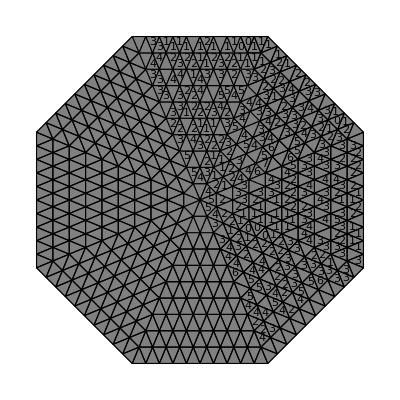

```mathematica
Graphics@RevealedDisplayBoard[board]
```

#### Setting the Game Up

```mathematica
play[]:=
Row[{DynamicModule[{board = boardSetUp[10,0.2]}, 
ClickPane[
	Dynamic[
	(*Display*)
		Graphics[RevealedDisplayBoard[board], ImageSize->Large]
		]
		(*Interaction*)
		

	,Column[Button["Randomize",board = boardSetUp[10,0.20]]]]]}
	(*Buttons and sliders*)
	]
```

```mathematica
processClick[board_,clicked_]:= Module[{},

]
```

```mathematica
play[]
```

```mathematica
Select[MassCentroids,EuclideanDistance[{1,1},#]&]
```

{}

### Other

```mathematica
ModelToView[board_]:= 

Module[
{graphics = {},x,y},
	For[x=1,x≤ 30,x++,
						AppendTo[graphics,{}];
						For[y = 1,y≤ 16,y++,
							If[board⟦x⟧⟦y⟧⟦1⟧=== Red,
							AppendTo[graphics,{Red,Circle[{y+0.5,x-0.5},0.5]}],
							AppendTo[graphics,{Blue,Circle[{y+0.5,x-0.5},0.5],Black,Text[board⟦x⟧⟦y⟧⟦1⟧,{y+0.5,x-0.5}]}]
							]
						
						]
					];
				Return[graphics];
					
					
					


				]
```

```mathematica
minesweeperBoard[]:= Module[
{minecount,row,section,x,y},
(*Mine, status, probability*)
(*Red are mines*)

For[x = 2,x ≤ 29,x++,
For[y = 2,y≤ 15,y++,
If[board⟦x⟧⟦y⟧⟦1⟧ == Blue,
	board⟦x⟧⟦y⟧⟦1⟧ = borderingMines[board,x,y];
	(*riskMap[x,y];*)
	]
	]
];
Return[Null];

]
```

```mathematica
borderingMines[x_,y_]:= Module[{count = 0,X,Y},
						For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								If[board⟦X⟧⟦Y⟧⟦1⟧ == Red,
								count++;
								]
							]
						];
						Return[count];
						]
```

```mathematica
riskMap[x_,y_]:= Module[{count,X,Y},
					count = borderingMines[x,y];
				For[X = x-1,X ≤ x+1,X++,
							For[Y = y-1,Y≤ y+ 1,Y++,
								
								board⟦X⟧⟦Y⟧⟦3⟧  += count/9;
								
							]
						];

]
```

```mathematica
click[x_,y_]:= Module[{},
				If[board⟦x⟧⟦y⟧⟦1⟧=== Red,

				Print["game over"],
				board⟦x⟧⟦y⟧⟦2⟧ = 1
				
					];
				


				]
```

```mathematica
minesweeperBoard[]
board
```

$Aborted[]